# Near Equilibria Static Analysis of a Helically Folded Tube - Code & Experimental Data

## Formatting

```mathematica
Format[xd] =Subscript[x, d] ;
Format[xdN] =Subscript[x̃, d];
Format[xdS] ="x_d^*";
Format[yd] =Subscript[y, d] ;
Format[ydN] =Subscript[ỹ, d];
Format[ydS] ="y_d^*";
Format[zd] =Subscript[z, d] ;
Format[zdN] =Subscript[z̃, d];
Format[zdS] ="z_d^*";
Format[rd] =Subscript[r, d] ;
Format[rdN] =Subscript[r̃, d];
Format[rdS] ="r_d^*";
Format[θd] =Subscript[θ, d];
Format[θ0]=Subscript[θ, 0];
Format[θr]=Subscript[θ, r];
Format[x0N]=Subscript[x̃, 0];
Format[xrN]=Subscript[x̃, r];
Format[y0N]=Subscript[ỹ, 0];
Format[yrN]=Subscript[ỹ, r];
Format[z0N]=Subscript[z̃, 0];
Format[zrN] =Subscript[z̃, r];
Format[r0N]=Subscript[r̃, 0];
Format[rrN]=Subscript[r̃, r];
Format[rN] =r̃;
Format[rS] =SuperStar[r];
Format[rneut]=Subscript[r, neut];
Format[rneutN] =Subscript[r̃, neut];
Format[rneutS] = Subscript[SuperStar[r], neut];
Format[nN] =ñ;
Format[nS] =SuperStar[n];
Format[ζN] =ζ̃;
Format[ζS] =SuperStar[ζ];
Format[zζN] =Subscript[z̃, ζ];
Format[ΔψN] ="Δψ̃";
Format[ΔψS] =SuperStar[Δψ];
Format[ΔζN] ="Δζ̃"; 
Format[ΔζS] =SuperStar[Δζ];
Format[Δθb] =Δθ^b ;
Format[ΔθbN] ="Δ(θ̃)^b"; 
Format[ΔθbS] =SuperStar[(Δθ^b )];
Format[βoN] =Subscript[β̃, o];
Format[βoS] ="β_o^*";
Format[αN] =α̃;
Format[αS] =SuperStar[α];
Format[uVec] =Overscript[u, "→"];
Format[uVecN] =Overscript[ũ, "→"];
Format[uN] =ũ;
Format[uS] =SuperStar[u];
Format[vN] =ṽ;
Format[vS] =SuperStar[v];
Format[wN] =w̃;
Format[wS] =SuperStar[w];
Format[εN] =ε̃;
Format[εS] =SuperStar[ε];
Format[ue]="u_e";
Format[ueN] =Subscript[ũ, e];
Format[ueS] ="u_e^*";
Format[Upe]=Subscript[U, pe];
Format[UpeN] =Subscript[Ũ, pe];
Format[UpeS] ="U_pe^*";
Format[Ue]="U_e";
Format[UeN] =Subscript[Ũ, e];
Format[UeS] ="U_e^*";
Format[WN] =W̃;
Format[WS] =SuperStar[W];
Format[pin] ="p_in";
Format[pinN] =Subscript[p̃, in];
Format[pinS] ="p_in^*";
Format[FN] =F̃;
Format[FS] =SuperStar[F];
Format[TN] =T̃;
Format[TS] =SuperStar[T];
Format[ϕS] =SuperStar[ϕ]; 
Format[ϕN]=ϕ̃;
Format[ζ0N] =Subscript[ζ̃, 0]; 
Format[xdN0] ="(x̃)_d^(0)";
Format[xdN1] ="(x̃)_d^(1)";
Format[xdN2] ="(x̃)_d^(2)";
Format[xdN3] ="(x̃)_d^(3)";
Format[ydN0] ="(ỹ)_d^(0)";
Format[ydN1] ="(ỹ)_d^(1)";
Format[ydN2] ="(ỹ)_d^(2)";
Format[ydN3] ="(ỹ)_d^(3)";
Format[zdN0] ="(z̃)_d^(0)";
Format[zdN1] ="(z̃)_d^(1)";
Format[zdN2] ="(z̃)_d^(2)";
Format[rdN1] = "(r̃)_d^(1)";
Format[rdN2] ="(r̃)_d^(2)";
Format[rdN3] = "(r̃)_d^(3)";
Format[θd1] = "θ_d^(1)";
Format[θd2] ="θ_d^(2)";
Format[θd3] ="θ_d^(3)";
Format[rN1] ="(r̃)^(1)";
Format[rN2] ="(r̃)^(2)";
Format[rN3] ="(r̃)^(3)";
Format[rneutN1] ="(r̃)_neut^(1)";
Format[rneutN2] ="(r̃)_neut^(2)";
Format[rneutN3] ="(r̃)_neut^(3)";
Format[RN1] ="(R̃)^(1)"; 
Format[RneutN1] ="(R̃)_neut^(1)";
Format[ΔθbN0] ="(Δ(θ̃)^(b))^(0)"; 
Format[ΔθbN1] ="(Δ(θ̃)^(b))^(1)";
Format[ζN0] ="(ζ̃)^(0)";
Format[ζN1] ="(ζ̃)^(1)";
Format[ζN2] ="(ζ̃)^(2)";
Format[ΔζN0] ="Δ(ζ̃)^(0)"; 
Format[ΔζN1] ="Δ(ζ̃)^(1)"; 
Format[ψE0]="ψ^(0)";
Format[ψE1]="ψ^(1)";
Format[ψE2]="ψ^(2)";
Format[ΔψN0]="Δ(ψ̃)^(0)";
Format[ΔψN1]="Δ(ψ̃)^(1)";
Format[αN0]="(α̃)^(0)";
Format[uVecN0] ="OverVector[ũ]^(0)";
Format[uVecN1] ="OverVector[ũ]^(1)";
Format[uVecN2] ="OverVector[ũ]^(2)";
Format[εcN0] ="(ε̃)_c^(0)";
Format[εN0] ="(ε̃)^(0)";
Format[ueN0] ="(ũ)_e^(0)";
Format[UeN0] ="(Ũ)_e^(0)";
Format[WN0] ="(W̃)^(0)";
Format[UpeN0] ="(Ũ)_pe^(0)";
Format[pinN0] ="((p̃)_in)^(0)";
Format[FN0] ="(F̃)^(0)";
Format[TN0] ="(T̃)^(0)";
Format[ϵr]=Subscript[ϵ, r];
Format[ϵn]=Subscript[ϵ, n];
Format[ϵh]=Subscript[ϵ, h];
Format[ϵΔψ]=Subscript[ϵ, Δψ];
Format[ϵϕ]=Subscript[ϵ, ϕ];
Format[xhat]=x̂;
Format[yhat]=ŷ;
Format[zhat]=ẑ;
Format[rhat]=r̂;
Format[θhat]=θ̂;
Format[chat]=ĉ;
Format[mhat]=m̂;
Format[χhat]=χ̂;
Format[nhat]=n̂;
Format[ri]=Subscript[r, i];
Format[ro]=Subscript[r, o];
Format[βo]=Subscript[β, o];
Format[Q1]=Subscript[Q, 1];
Format[Q2]=Subscript[Q, 2];
Format[Q3]=Subscript[Q, 3];
Format[BCVec] = Overscript[BC, "→"] ;
Format[BCx]=Subscript[BC, x];
Format[BCy]=Subscript[BC, y];
Format[BCz]=Subscript[BC, z];
Format[PVec]=Overscript[P, "→"] ;
Format[PcyVec]="TraditionalForm`";
Format[PVecN]=Overscript[P̃, "→"] ;
Format[PcyVecN]= "TraditionalForm`";
Format[P0VecN]="TraditionalForm`";
Format[Pcy0VecN]="TraditionalForm`";
Format[PrVecN]="TraditionalForm`";
Format[PcyrVecN]="TraditionalForm`";
Format[PcstrVec]=Subscript[Overscript[P, "→"], cstr] ;
Format[TneutVec]=Subscript[Overscript[T, "→"], neut] ;
Format[RneutVec]=Subscript[Overscript[R, "→"], neut] ;
Format[ToVec]=Subscript[Overscript[T, "→"], o] ;
Format[RoVec]=Subscript[Overscript[R, "→"], o] ;
Format[ψ0]=Subscript[ψ, 0];
Format[ε22] ="ε";
Format[ε22N]="(ε̃)_(2, 2)";
Format[εc] ="ε_c";
Format[εcN] ="(ε̃)_c";
Format[εcS] ="ε_c^*";
Format[ε11c]="ε_c_(1, 1)"; 
Format[ε12c]="ε_c_(1, 2)";
Format[ε13c]="ε_c_(1, 3)";
Format[ε22c]="ε_c_(2, 2)";
Format[ε23c]="ε_c_(2, 3)";
Format[ε33c]="ε_c_(3, 3)";
Format[My] =Subscript[M, y];
Format[ζ0] =Subscript[ζ, 0];
Format[D[a_[xd,yd,zd],xd]]=("∂"a)/("∂x_d");
Format[D[a_[xd,yd,zd],yd]]=("∂"a)/("∂y_d");
Format[D[a_[xd,yd,zd],zd]]=("∂"a)/("∂z_d");
Format[D[a_[rdN,θd,zdN],rdN]]=("∂"a)/("∂(r̃)_d");
Format[D[a_[rdN,θd,zdN],θd]]=("∂"a)/("∂θ_d");
Format[D[a_[rdN,θd,zdN],zdN]]=("∂"a)/("∂(z̃)_d");
Format[D[a_[rd,θd,zd],rd]]=("∂"a)/("∂r_d");
Format[D[a_[rd,θd,zd],θd]]=("∂"a)/("∂θ_d");
Format[D[a_[rd,θd,zd],zd]]=("∂"a)/("∂z_d");
Format[D[a_[RN1,θ,nN],RN1]]=("∂"a)/("∂(R̃)^(1)");
Format[D[a_[RN1,θ,nN],θ]]=("∂"a)/("∂θ");
Format[D[a_[RN1,θ,nN],nN]]=("∂"a)/("∂ñ");
Format[D[a_[ζ],ζ]]=("d"a)/("dζ");
Format[D[a_[Δθb],Δθb]]=("d"a)/("dΔθ^b");
Format[D[a_[ΔψN],ΔψN]]=("d"a)/("dΔψ̃");
Format[D[a_[ΔζN],ΔζN]]=("d"a)/("dΔζ̃");
Format[D[a_[ΔθbN],ΔθbN]]=("d"a)/("dΔ(θ̃)^b");
Format[Jrneut]="J_r_neut";
Format[JNrneut]="(J̃)_r_neut";
Format[JSrneut]="(J^*)_r_neut";
Format[JW]="J_W";
Format[JNW]="(J̃)_W";
Format[JSW]="(J^*)_W";
Format[JUe]="J_U_e";
Format[JNUe]="(J̃)_U_e";
Format[JSUe]="(J^*)_U_e";
Format[Δz0N]="Δ(z̃)_0";
Format[Δz0S]="Δz_0^*";
Format[Δz0]= Subscript[Δz, 0];
Format[ΔθN] ="Δθ̃";
Format[ΔθS] =SuperStar[Δθ];
Format[cθ0]=Subscript[c, Subscript[θ, 0]]; 
Format[cθ1]=Subscript[c, Subscript[θ, 1]];
Format[cθ2]=Subscript[c, Subscript[θ, 2]];
Format[cp]=Subscript[c, p];
Format[rd0p] ="r_d0^+";
Format[ΔθbDeg] ="Δθ^b(°)";
Format[βoDeg] =" β_o(°)";
Format[Δθζ0p]="Δθ(°)(ζ_0^+)";
Format[ΔθDeg]="Δθ(°)";
```

## Nomenclature

Conventions
HFT - An abbreviation for helically folded tube.
ã - A normalized geometric quantity is denoted with a tilde.
a^* - A characteristic quantity is denoted with a superscript asterisk.
a_r - The “r” subscript indicates that the quantity is in the reference configuration.
a_0 - The “0” subscript indicates that the quantity is in the initial configuration.
a_d - The “d” subscript indicates that the quantity is in the deformed configuration.
a^(n)- A coefficient of the ϵ^n term in series expansions.
da - A notation that represents a total differential.
a_(,b)=(∂ a)/(∂ b) - A notation that is used for partial derivatives.
(·)_(i,j) - The tensor component on the i'th plane and in the j’th direction.

Directions
x̂,ŷ,ẑ - Cartesian directions.
r̂,θ̂,ẑ - Cylindrical directions.
r̂,ĉ,m̂ - Helical directions.
χ̂,ĉ,n̂ - Deformed directions.

Coordinates
(x,y,z) - Cartesian coordinates.
(r,θ,z) - Cylindrical coordinates.
(r,c,m) - Helical coordinates.
(χ,c,n) - Deformed coordinates.
(r,θ,n) - Mid-plane reference coordinates.
(r_d,θ_d,z_d) - Standard cylindrical coordinates.

Small Parameters
ϵ - A small real parameter.
ϵ_r - The ratio between the width, r_o-r_i, and the characteristic radius of the helical folds, r_o.
ϵ_n - The ratio between the thickness, h, and the width, r_o-r_i.
ϵ_h - The normalization of the helical angle, β_o.
ϵ_Δψ - The normalization of the deformation angle relative to the initial configuration, Δψ.
ϵ_ϕ - The normalization of the deviation from the average axial translation, ϕ.

Parameters that Defines The Problem
β_o - Helical angle at r=r_o. 
ψ_0 - Initial deformation angle.
h - Helicoidal shell thickness.
r_i - Internal radius in the reference configuration.
r_o - Outer radius in the reference configuration.
M_y - Young’s modulus.

Rotation Matrices
β|_r - Helical angle.
ψ - Deformation angle with respect to the reference configuration.
Q_1 - Rotation matrix  from cylindrical to Cartesian coordinates.
Q_2 - Rotation matrix  from helical to cylindrical coordinates.
Q_3 - Rotation matrix  from deformed to helical coordinates.
Q - Rotation matrix from  deformed  to Cartesian coordinates.

Position Vectors
P^(->) = (x_d,y_d,z_d) - Cartesian position vector of an upper helicoidal shell in the deformed configuration.
(P^(->))_cy= (r_d,θ_d,z_d) - Cylindrical position vector of an upper helicoidal shell in the deformed configuration.
(P^(->))_cstr - Cartesian position vector of an upper helicoidal shell in the deformed configuration, which is constrained to be rotated around the mid-plane (n=0) at r=r_neut.
(T^(->))_o - The translation vector of the Cartesian coordinate system to the helical fiber at r=r_o and n=0.
(R^(->))_o - The vector (r_o-r,0,n) in the deformed coordinate system transferred back to the Cartesian system of coordinates.
BC^(->)=(BC_x,BC_y,BC_z) - Cartesian translation vector that is used to constrain the position vector.
(T^(->))_neut - The translation vector of the Cartesian coordinate system to the helical fiber at r=r_neut and n=0.
(R^(->))_neut - The vector (r_neut-r,0,n) in the deformed coordinate system transferred back to the Cartesian system of coordinates.

Linear and Rotational Displacements
(R̃)^(1)=(r̃)^(1)+ϵ_r(r̃)^(2)+ϵ_r^2(r̃)^(3) - An expression that is used in the asymptotic approximation of the normalized radius, r̃.
(R̃)_neut^(1) =(r̃)_neut^(1) +ϵ_r(r̃)_neut^(2)+ϵ_r^2(r̃)_neut^(3) - An expression that is used in the asymptotic approximation of the normalized neutral radius, (r̃)_neut.
α - Reference angle. 
Δψ - Deformation angle with respect to the initial configuration.
ζ - The average translation along the ẑ direction relative to the reference configuration at r=r_i and n=0.  
ϕ -  The deviation angle from the average translation (along the ẑ direction) at r=r_i and n=0. 
Δζ - The average translation along the ẑ direction relative to the initial  configuration at r=r_i and n=0. 
Δθ^b = (θ_0-θ_d)|_(r=r_i,n=0) - The change of the polar rotation angle between the initial and the deformed configurations at the mid-plane (n=0) radius r=r_i  defined for a specific branch.
u^(->) =P^(->)-(P^(->))_0 = (u,v,w) - Cartesian displacements.

Strains
ε_c  - The strain tensor in the Cartesian coordinate system. 
ε  - The strain tensor in the deformed coordinate system where the ĉ direction is defined at r=r_neut.

Neutral Radius
J_r_neut - A Jacobian determinant from (r_d,z_d) to ((r̃)^(1),ñ) that is used for the calculation of r_neut.
r_neut - Neutral radius.
S - The surface (r,n)∈[r_i,r_o]×[-h/2,h/2].
 
Potential Energy
J_U_e - A Jacobian determinant from (x_d,y_d,z_d) to ((r̃)^(1),θ,ñ) that is used for the calculation of U_e.
u_e - The strain energy density. 
U_e - The elastic energy. 
V_e - The volume of the upper helicoidal shell.
(z̃)_ζ - A normalized z_d coordinate, which is normalized as ζ.
J_W - A Jacobian determinant from (x_d,y_d,z_d) to (r̃,θ,(z̃)_ζ) that is used for the calculation of W.
W - The work done by the pressure within the helicoidal element. 
V_f - The fluid volume, which is occupied between the upper helicoidal shell, and the two surfaces (z-z_r)|_(r=r_i,n=0)=0 and (z-z_r)|_(r=r_i,n=0)=ζ.
U_pe - The potential energy. 

Forces and Moments
p - Pressure within the helicoidal element.
p_in - Inlet pressure.
F - Axial force along the z-axis.
T - Torque along the opposite direction to the z-axis.
M - Moment along the ŷ direction.

Experimental Verification
ζ_0^+ - The average translation, ζ, in the open stability state.
ζ_0^- - The average translation, ζ, in the closed stability state.
L_HFT - The length of the entire HFT.
Δθ_HFT - The rotation angle of the entire HFT.
ψ_0^+ - The deformation angle, ψ, in the open stability state.
r_d0^+ - The deformed outer radius at n=h/2 and in the open stability state.
Δz_0 - The pitch of a single element.
Δθ - The change of the polar rotation angle between the initial and the deformed configurations at the mid-plane (n=0) radius r=r_i, which which contains the full range of ζ.
c_θ_0 - A constant in the expression of Δθ.
c_θ_1 - Linear contribution constant, which is used in the expression of Δθ.
c_p - Linear contribution constant for the pressure.
NE - The number of elements of an HFT.
DL - The “dead” length of an HFT.
δ - A small segment near the stability point.

## 1. Problem Formulation

### 1. Definition

The potential energy is given by

```mathematica
UpeEq = Upe ==Ue-W;
Grid[{{UpeEq,","}}]
```

U_pe==U_e-W | ,

where U_e denotes the elastic energy and W is the work due to the pressure, p, within the helicoidal element.

### 2. Normalization

Let ϵ_r be the ratio between the width, r_o-r_i, and the characteristic radius of the helical folds, r_o, and let ϵ_n be the ratio between the thickness, h, and the width, r_o-r_i,

```mathematica
ϵrEq=ϵr== (ro-ri)/ro;
ϵnEq=ϵn== h/(ro-ri);
Grid[{{ϵrEq,",",ϵnEq,"."}}]
```

ϵ_r==(-r_i+r_o)/r_o | , | ϵ_n==h/(-r_i+r_o) | .

From geometrical considerations of the fabricated HFT, it is reasonable to assume that ϵ_n,ϵ_r=O(ϵ), where ϵ is a small dimensionless parameter.

```mathematica
varst={ϵr,ϵn};
```

In order to render the problem dimensionless and scale the values to order O(1) with respect to ϵ, the following transformations are applied: for the position vector in Cartesian and standard cylindrical coordinates, as well as the remaining coordinates,

```mathematica
xdNEq = xdN== xd/xdS; xdEq =xd== Solve[xdNEq,xd][[1]][[1]][[2]];
ydNEq = ydN== yd/ydS;ydEq =yd== Solve[ydNEq,yd][[1]][[1]][[2]];
zdNEq = zdN== zd/zdS; zdEq =zd== Solve[zdNEq,zd][[1]][[1]][[2]];
rdNEq = rdN== rd/rdS;  rdEq =rd== Solve[rdNEq,rd][[1]][[1]][[2]];
rNEq =rN== r/rS;   rEq =r== Solve[rNEq,r][[1]][[1]][[2]];
nNEq =nN== n/nS; nEq =n== Solve[nNEq,n][[1]][[1]][[2]];
zζNEq =zζN== zd/ζS;  zdζEq =zd== Solve[zζNEq,zd][[1]][[1]][[2]];
Grid[{{PVecN,"=","(",xdNEq[[1]],",",ydNEq[[1]],",",zdNEq[[1]],")","=","(",xdNEq[[2]],",",ydNEq[[2]],",",zdNEq[[2]],")",",",PcyVecN,"=","(",rdNEq[[1]],",",θd,",",zdNEq[[1]],")","=","(",rdNEq[[2]],",",θd,",",zdNEq[[2]],")",",",rNEq[[1]],"=",rNEq[[2]],",",nNEq[[1]],"=",nNEq[[2]],",",zζNEq[[1]],"=",zζNEq[[2]],","}}]
```

OverVector[P̃] | = | ( | (x̃)_d | , | (ỹ)_d | , | (z̃)_d | ) | = | ( | x_d/x_d^* | , | y_d/y_d^* | , | z_d/z_d^* | ) | , | TraditionalForm` | = | ( | (r̃)_d | , | θ_d | , | (z̃)_d | ) | = | ( | r_d/r_d^* | , | θ_d | , | z_d/z_d^* | ) | , | r̃ | = | r/r^* | , | ñ | = | n/n^* | , | (z̃)_ζ | = | z_d/ζ^* | ,

where (z̃)_ζ is a normalized quantity of z_d, with the same characteristic value as ζ̃, for the degrees of freedom and other geometric parameters,

```mathematica
ζNEq =ζN== ζ/ζS;  ζEq =ζ== Solve[ζNEq,ζ][[1]][[1]][[2]];
ϕNEq =ϕN== ϕ/ϕS;  ϕEq =ϕ== Solve[ϕNEq,ϕ][[1]][[1]][[2]];
ΔψNEq =ΔψN== (ψ-ψ0)/ΔψS; ψEq =ψ== Solve[ΔψNEq,ψ][[1]][[1]][[2]];
ΔζNEq =ΔζN== (ζ-ζ0)/ΔζS;  ζEq1 =ζ==( Solve[ΔζNEq,ζ][[1]][[1]][[2]]/.ζ0->ζEq[[2]]/.ζN->ζ0N);
ΔθbNEq =ΔθbN== Δθb/ΔθbS;   ΔθbEq =Δθb== Solve[ΔθbNEq,Δθb][[1]][[1]][[2]];
βoNEq =βoN== βo/βoS;  βoEq =βo== Solve[βoNEq,βo][[1]][[1]][[2]];
αNEq =αN== α/αS; αEq =α== Solve[αNEq,α][[1]][[1]][[2]];
Grid[{{ζNEq[[1]],"=",ζNEq[[2]],",",ϕNEq[[1]],"=",ϕNEq[[2]],",",ΔψNEq[[1]],"=",ΔψNEq[[2]],",",ΔζNEq[[1]],"=",ΔζNEq[[2]],",",ΔθbNEq[[1]],"=",ΔθbNEq[[2]],",",βoNEq[[1]],"=",βoNEq[[2]],",",αNEq[[1]],"=",αNEq[[2]],","}}]
```

ζ̃ | = | ζ/ζ^* | , | ϕ̃ | = | ϕ/ϕ^* | , | Δψ̃ | = | (ψ-ψ_0)/Δψ^* | , | Δζ̃ | = | (ζ-ζ_0)/Δζ^* | , | Δ(θ̃)^b | = | Δθ^b/((Δθ^b)^*) | , | (β̃)_o | = | β_o/β_o^* | , | α̃ | = | α/α^* | ,

for the displacement vector in Cartesian coordinates and the strain tensor in Cartesian and deformed coordinates, where r=r_neut is substituted into the rotation matrix,

```mathematica
uNEq =uN== u/uS; uEq =u== Solve[uNEq,u][[1]][[1]][[2]];
vNEq =vN== v/vS; vEq =v== Solve[vNEq,v][[1]][[1]][[2]];
wNEq =wN== w/wS; wEq =w== Solve[wNEq,w][[1]][[1]][[2]];
εcNEq =εcN== εc/εcS; εcEq=εc==Solve[εcNEq,εc][[1]][[1]][[2]];
εNEq =εN== ε/εS; εEq=ε==Solve[εNEq,ε][[1]][[1]][[2]];

Grid[{{uVecN ,"=","("uNEq[[1]],vNEq[[1]],wNEq[[1]],")",",","(",uNEq[[2]],vNEq[[2]],wNEq[[2]],")",",",εcNEq[[1]],"=",εcNEq[[2]],",",εNEq[[1]],"=",εNEq[[2]],","}}]
```

OverVector[ũ] | = | ( ũ | ṽ | w̃ | ) | , | ( | u/u^* | v/v^* | w/w^* | ) | , | (ε̃)_c | = | ε_c/ε_c^* | , | ε̃ | = | ε/ε^* | ,

for the energy and work,

```mathematica
ueNEq =ueN== ue/ueS; ueEq=ue==Solve[ueNEq,ue][[1]][[1]][[2]];
UeNEq =UeN== Ue/UeS; UeEq=Ue==Solve[UeNEq,Ue][[1]][[1]][[2]];
WNEq =WN== W/WS; WEq=W==Solve[WNEq,W][[1]][[1]][[2]];
UpeNEq =UpeN== Upe/UpeS; UpeEq1=Upe==Solve[UpeNEq,Upe][[1]][[1]][[2]];

Grid[{{ueNEq[[1]],"=",ueNEq[[2]],",",UeNEq[[1]],"=",UeNEq[[2]],",",WNEq[[1]],"=",WNEq[[2]],",",UpeNEq[[1]],"=",UpeNEq[[2]],","}}]
```

(ũ)_e | = | u_e/u_e^* | , | (Ũ)_e | = | U_e/U_e^* | , | W̃ | = | W/W^* | , | (Ũ)_pe | = | U_pe/U_pe^* | ,

and for the loads,

```mathematica
pinNEq =pinN== pin/pinS; pinEq=pin==Solve[pinNEq,pin][[1]][[1]][[2]];
FNEq =FN== F/FS;
TNEq =TN== T/TS;

Grid[{{pinNEq[[1]],"=",pinNEq[[2]],",",FNEq[[1]],"=",FNEq[[2]],",",TNEq[[1]],"=",TNEq[[2]],"."}}]
```

(p̃)_in | = | p_in/p_in^* | , | F̃ | = | F/F^* | , | T̃ | = | T/T^* | .

For consistency with the nomenclature of the small parameters, the following notations are used hereafter:

```mathematica
βoSEq =βoS== ϵh; ΔψSEq=  ΔψS==ϵΔψ; ϕSEq=  ϕS==ϵϕ;
Grid[{{βoSEq[[1]],"=",βoSEq[[2]],",",ΔψSEq[[1]],"=",ΔψSEq[[2]],",",ϕSEq[[1]],"=",ϕSEq[[2]],"."}}]
```

β_o^* | = | ϵ_h | , | Δψ^* | = | ϵ_Δψ | , | ϕ^* | = | ϵ_ϕ | .

The orders of magnitude of the characteristic quantities of the helical angle and the deformation angle relative to the initial configurations are defined by

```mathematica
varst=Join[varst,{ϵh}];  
varst2={ϵΔψ};
```

ϵ_h=O(ϵ) and ϵ_Δψ=O(ϵ).

From geometrical considerations, the normalization of the deviation from the average translation is derived, so that it does not affect both the leading-order term of the energy and the first-order approximation of the axial rotation, namely I define

```mathematica
varst3={ϵϕ};
```

ϵ_ϕ=O(ϵ^4).

The characteristic quantities r^* and n^* are obtained from the problem’s geometric limits, as

```mathematica
rSEq = rS==ro;
nSEq=nS==h;
Grid[{{rSEq[[1]],"=",rSEq[[2]],",",nSEq[[1]],"=",nSEq[[2]],"."}}]
```

r^* | = | r_o | , | n^* | = | h | .

By applying the rigid rotation assumption of the χn sections, both OverVector[P̃] and OverVector[P̃]_cy are found. Then, to obtain their characteristic values, I request that their dimensionless versions be of order O(1) with respect to ϵ, which yields that

```mathematica
xdSEq = xdS==ro;
ydSEq=ydS==ro;
zdSEq=zdS==ϵh ro ;
rdSEq=rdS==ro ;
Grid[{{xdSEq[[1]],"=",ydSEq[[1]],"=",rdSEq[[1]],"=",rdSEq[[2]],",",zdSEq[[1]],"=",zdSEq[[2]],"."}}]
```

x_d^* | = | y_d^* | = | r_d^* | = | r_o | , | z_d^* | = | r_o ϵ_h | .

Now, by using the tangential component of (P⃗)_cy, the characteristic value of Δθ^b=(θ_0-θ_d)|_(r=r_i,n=0) is found to be

```mathematica
ΔθbSEq=ΔθbS==ϵr ϵh ϵΔψ;
Grid[{{ΔθbSEq[[1]],"=",ΔθbSEq[[2]],"."}}]
```

(Δθ^b)^* | = | ϵ_h ϵ_r ϵ_Δψ | .

The characteristic quantities, ζ^*, Δζ^*, and α^* are derived according to geometrical considerations  and are given as follows:

```mathematica
ζSEq = ζS==ϵr ro ;
ΔζSEq=ΔζS==ϵr ϵΔψ ro ;
αSEq=αS==ϵh;
Grid[{{ζSEq[[1]],"=",ζSEq[[2]],",",ΔζSEq[[1]],"=",ΔζSEq[[2]],",",αSEq[[1]],"=",αSEq[[2]],"."}}]
```

ζ^* | = | r_o ϵ_r | , | Δζ^* | = | r_o ϵ_r ϵ_Δψ | , | α^* | = | ϵ_h | .

The Cartesian displacement vector is expressed via the difference between the deformed and the initial position vectors as u⃗=P⃗-(P⃗)_0=(u,v,w). Requesting that the leading-order terms of u⃗ be of order O(1) with respect to ϵ results in

```mathematica
uSEq = uS==ϵr ϵΔψ ro ;
vSEq = vS==ϵr ϵΔψ ro;
wSEq = wS==ϵr ϵΔψ ro ;
Grid[{{uSEq[[1]],"=",vSEq[[1]],"=",wSEq[[1]],"=",uSEq[[2]],"."}}]
```

u^* | = | v^* | = | w^* | = | r_o ϵ_r ϵ_Δψ | .

From the solution of the strain in the conical case (see Almen and Laszlo [1936] or Ilssar et al. [2022]), it is expected that the only non-negligible strain term is the helical strain term, ε_(2,2). Here, I used an adapted normalization, which is known according to the conical solution, namely

```mathematica
εSEq = εS== ϵr ϵΔψ;
Grid[{{εSEq[[1]],"=",εSEq[[2]],"."}}]
```

ε^* | = | ϵ_r ϵ_Δψ | .

Using the linearity assumption of the material for the uniaxial helical stress case leads to the following expression for the elastic energy density

```mathematica
ueEq1=ue==My/2 ε22^2;
Grid[{{ueEq1[[1]],"=",ueEq1[[2]],","}}]
```

u_e | = | (M_y ε^2)/2 | ,

where the suitable characteristic quantity is given by

```mathematica
ueSEq= ueS==ϵr^2 ϵΔψ^2 My ;
Grid[{{ueSEq[[1]],"=",ueSEq[[2]],"."}}]
```

u_e^* | = | M_y ϵ_r^2 ϵ_Δψ^2 | .

The elastic energy is calculated by integrating the elastic energy density over the volume of the upper helicoidal shell.
Incorporating the volume contribution of the upper helicoidal shell to the elastic energy density and assuming that the work and the potential energy are of the same order of magnitude as the elastic energy implies that

```mathematica
UeSEq= UeS==ueSEq[[2]]  ro^3 ϵr^2 ϵn;
WSEq= WS==UeSEq[[2]];
UpeSEq= UpeS==UeSEq[[2]];
Grid[{{UeSEq[[1]],"=",WSEq[[1]],"=",UpeSEq[[1]],"=",UeSEq[[2]],"."}}]
```

U_e^* | = | W^* | = | U_pe^* | = | M_y r_o^3 ϵ_n ϵ_r^4 ϵ_Δψ^2 | .

The fluid volume of the upper part of the element is constrained by the upper helicoidal shell and by the surfaces (z-z_r)|_(r=r_i,n=0)=0 and (z-z_r)|_(r=r_i,n=0)=ζ. Thus, to obtain the pressure’s characteristic value, I divide the characteristic value of the work by the characteristic value of the change from the initial to the deformed configuration of this volume, which leads to

```mathematica
pinSEq= pinS==UeSEq[[2]]/(ro^2 ΔζSEq[[2]]);
Grid[{{pinSEq[[1]],"=",pinSEq[[2]],"."}}]
```

p_in^* | = | M_y ϵ_n ϵ_r^3 ϵ_Δψ | .

Using the Euler-Lagrange equation with the degrees of freedom Δζ and Δθ^b for the force, F, and the torque, T, respectively, and normalizing it by using the characteristic values for U_pe, Δζ and Δθ^b, yields that

```mathematica
FSEq = FS==UeSEq[[2]]/ΔζSEq[[2]];
TSEq = TS==UeSEq[[2]]/ΔθbSEq[[2]];
Grid[{{FSEq[[1]],"=",FSEq[[2]],",",TSEq[[1]],"=",TSEq[[2]],"."}}]
```

F^* | = | M_y r_o^2 ϵ_n ϵ_r^3 ϵ_Δψ | , | T^* | = | (M_y r_o^3 ϵ_n ϵ_r^3 ϵ_Δψ)/ϵ_h | .

Now, after I have defined all of the small parameters, normalizations, and characteristic quantities, I shall present the asymptotic expansions that I use to obtain approximate solutions. The following asymptotic expansions are assumed:

for the position vector coordinates,

```mathematica
xdNExpansion = xdN==xdN0 +ϵ xdN1 +ϵ^2 xdN2 +ϵ^3 xdN3 +O[ϵ]^4;
ydNExpansion = ydN==ydN0 +ϵ ydN1 +ϵ^2 ydN2 +ϵ^3 ydN3 +O[ϵ]^4;
zdNExpansion = zdN==zdN0 +ϵ zdN1 +ϵ^2 zdN2 +O[ϵ]^3;
rdNExpansion = rdN==1+ϵ rdN1 +ϵ^2 rdN2 +ϵ^3 rdN3 +O[ϵ]^4;
θdExpansion = θd==θ+ϵ θd1 +ϵ^2 θd2 +ϵ^3 θd3 +O[ϵ]^4;
Grid[{{TableForm[{{xdNExpansion,","}}]},{TableForm[{{ydNExpansion,","}}]},{TableForm[{{zdNExpansion,","}}]},{TableForm[{{rdNExpansion,","}}]},{TableForm[{{θdExpansion,","}}]}},Alignment->Left]
```

(x̃)_d==(x̃)_d^(0)+(x̃)_d^(1) ϵ+(x̃)_d^(2) ϵ^2+(x̃)_d^(3) ϵ^3+O[ϵ]^4 | ,
(ỹ)_d==(ỹ)_d^(0)+(ỹ)_d^(1) ϵ+(ỹ)_d^(2) ϵ^2+(ỹ)_d^(3) ϵ^3+O[ϵ]^4 | ,
(z̃)_d==(z̃)_d^(0)+(z̃)_d^(1) ϵ+(z̃)_d^(2) ϵ^2+O[ϵ]^3 | ,
(r̃)_d==1+(r̃)_d^(1) ϵ+(r̃)_d^(2) ϵ^2+(r̃)_d^(3) ϵ^3+O[ϵ]^4 | ,
θ_d==θ+θ_d^(1) ϵ+θ_d^(2) ϵ^2+θ_d^(3) ϵ^3+O[ϵ]^4 | ,

for the degrees of freedom and other geometric parameters,

```mathematica
RN1Eq=RN1==rN1+ϵr rN2 +ϵr^2 rN3 ;
rN1Eq = rN1==Solve[RN1Eq[[1]]==RN1Eq[[2]],rN1][[1]][[1]][[2]];
rNExpansion = rN==1-ϵr rN1 -ϵr^2 rN2 -ϵr^3 rN3 +O[ϵ]^4;
rNExpansion1 =rNExpansion[[1]]== Simplify[rNExpansion[[2]]/.rN1->Solve[RN1Eq,rN1][[1]][[1]][[2]]];
ΔθbNExpansion = ΔθbN==ΔθbN0+ϵ ΔθbN1 +O[ϵ]^2;
ζNExpansion = ζN==ζN0+ϵ ζN1 +ϵ^2 ζN2+O[ϵ]^3; 
ΔζNExpansion = ΔζN==ΔζN0+ϵ ΔζN1+O[ϵ]^2;
ψExpansion = ψ==ψE0+ϵ ψE1 +ϵ^2 ψE2 +O[ϵ]^3;
ΔψNExpansion = ΔψN==ΔψN0+ϵ ΔψN1+O[ϵ]^2;
αNExpansion = αN==αN0+O[ϵ]^1;
Grid[{{TableForm[{{rNExpansion1,","}}]},{TableForm[{{RN1Eq,","}}]},{TableForm[{{ΔθbNExpansion,","}}]},{TableForm[{{ζNExpansion,","}}]},{TableForm[{{ΔζNExpansion,","}}]},{TableForm[{{ψExpansion,","}}]},{TableForm[{{ΔψNExpansion,","}}]},{TableForm[{{αNExpansion,","}}]}},Alignment->Left]
```

r̃==(1-(R̃)^(1) ϵ_r)+O[ϵ]^4 | ,
(R̃)^(1)==(r̃)^(1)+(r̃)^(2) ϵ_r+(r̃)^(3) ϵ_r^2 | ,
Δ(θ̃)^b==(Δ(θ̃)^(b))^(0)+(Δ(θ̃)^(b))^(1) ϵ+O[ϵ]^2 | ,
ζ̃==(ζ̃)^(0)+(ζ̃)^(1) ϵ+(ζ̃)^(2) ϵ^2+O[ϵ]^3 | ,
Δζ̃==Δ(ζ̃)^(0)+Δ(ζ̃)^(1) ϵ+O[ϵ]^2 | ,
ψ==ψ^(0)+ψ^(1) ϵ+ψ^(2) ϵ^2+O[ϵ]^3 | ,
Δψ̃==Δ(ψ̃)^(0)+Δ(ψ̃)^(1) ϵ+O[ϵ]^2 | ,
α̃==(α̃)^(0)+O[ϵ]^1 | ,

for the displacement vector in Cartesian coordinates and for the strain tensor in Cartesian and deformed coordinates, where r=r_neut is substituted into the rotation matrix,

```mathematica
uVecNExpansion = uVecN==uVecN0+ϵ uVecN1 +ϵ^2 uVecN2 +O[ϵ]^3;
εcNExpansion = εcN==εcN0+O[ϵ]^1;
εNExpansion = εN==εN0+O[ϵ]^1;
Grid[{{uVecNExpansion ,",",εcNExpansion,",",εNExpansion,","}}]
```

OverVector[ũ]==OverVector[ũ]^(0)+OverVector[ũ]^(1) ϵ+OverVector[ũ]^(2) ϵ^2+O[ϵ]^3 | , | (ε̃)_c==(ε̃)_c^(0)+O[ϵ]^1 | , | ε̃==(ε̃)^(0)+O[ϵ]^1 | ,

for the energy and work,

```mathematica
ueNExpansion = ueN==ueN0+O[ϵ]^1;
UeNExpansion = UeN==UeN0+O[ϵ]^1;
WNExpansion = WN==WN0+O[ϵ]^1;
UpeNExpansion = UpeN==UpeN0+O[ϵ]^1;
Grid[{{ueNExpansion,",",UeNExpansion,",",WNExpansion,",",UpeNExpansion,","}}]
```

(ũ)_e==(ũ)_e^(0)+O[ϵ]^1 | , | (Ũ)_e==(Ũ)_e^(0)+O[ϵ]^1 | , | W̃==(W̃)^(0)+O[ϵ]^1 | , | (Ũ)_pe==(Ũ)_pe^(0)+O[ϵ]^1 | ,

and for the loads,

```mathematica
pinNExpansion = pinN==pinN0+O[ϵ]^1;
FNExpansion = FN==FN0+O[ϵ]^1;
TNExpansion = TN==TN0+O[ϵ]^1;
Grid[{{pinNExpansion,",",FNExpansion,",",TNExpansion,"."}}]
```

(p̃)_in==((p̃)_in)^(0)+O[ϵ]^1 | , | F̃==(F̃)^(0)+O[ϵ]^1 | , | T̃==(T̃)^(0)+O[ϵ]^1 | .

## 2. Kinematic and Kinetic Relations

### Rotation Matrices

Let x̂,ŷ,ẑ and r̂,θ̂,ẑ be the unit vectors in the Cartesian and cylindrical coordinate systems (x,y,z) and (r,θ,z) , respectively, which are expressed by

```mathematica
xhatEq =xhat== {1, 0, 0};
yhatEq =yhat =={0, 1, 0};
zhatEq  = zhat== {0, 0, 1};
Grid[{{xhatEq[[1]],"=",MatrixForm[xhatEq[[2]]],",",yhatEq[[1]],"=",MatrixForm[yhatEq[[2]]],",",zhatEq[[1]],"=",MatrixForm[zhatEq[[2]]],","}}]
rhatEq=rhat == { Cos[θ],  Sin[θ], 0};
θhatEq =θhat ==  {- Sin[θ],  Cos[θ], 0};
Grid[{{rhatEq[[1]],"=",MatrixForm[rhatEq[[2]]],",",θhatEq[[1]],"=",MatrixForm[θhatEq[[2]]],",",zhatEq[[1]],"=",MatrixForm[zhatEq[[2]]],"."}}]
(*zhat is the same*)
```

x̂ | = | (1
0
0) | , | ŷ | = | (0
1
0) | , | ẑ | = | (0
0
1) | ,

r̂ | = | (Cos[θ]
Sin[θ]
0) | , | θ̂ | = | (-Sin[θ]
Cos[θ]
0) | , | ẑ | = | (0
0
1) | .

First, I express the helical unit vectors r̂,ĉ,m̂, which are defined by

```mathematica
(*rhat is the same*)chatEq=chat == θhat Cos["β|_r"]+zhat Sin["β|_r"];
mhatEq =mhat== -θhat Sin["β|_r"]+zhat Cos["β|_r"];
Grid[{{rhatEq[[1]],"=",MatrixForm[rhatEq[[2]]],",",chatEq[[1]],"=",MatrixForm[chatEq[[2]]],",",mhatEq[[1]],"=",MatrixForm[mhatEq[[2]]],","}}]
```

r̂ | = | (Cos[θ]
Sin[θ]
0) | , | ĉ | = | θ̂ Cos[β|_r]+ẑ Sin[β|_r] | , | m̂ | = | ẑ Cos[β|_r]-θ̂ Sin[β|_r] | ,

```mathematica
mhatEq=mhatEq /.{θhatEq[[1]]->θhatEq[[2]],zhatEq[[1]]->zhatEq[[2]]};
chatEq=chatEq /.{θhatEq[[1]]->θhatEq[[2]],zhatEq[[1]]->zhatEq[[2]]};
Grid[{{rhatEq[[1]],"=",MatrixForm[rhatEq[[2]]],",",chatEq[[1]],"=",MatrixForm[chatEq[[2]]],",",mhatEq[[1]],"=",MatrixForm[mhatEq[[2]]],","}}]
```

r̂ | = | (Cos[θ]
Sin[θ]
0) | , | ĉ | = | (-Cos[β|_r] Sin[θ]
Cos[β|_r] Cos[θ]
Sin[β|_r]) | , | m̂ | = | (Sin[β|_r] Sin[θ]
-Cos[θ] Sin[β|_r]
Cos[β|_r]) | ,

where β|_r denotes the helical angle between the positive directions of θ̂ and ĉ, and defined for any radius in the range r∈[r_i,r_o].

Next, I represent the χ̂,ĉ,n̂ unit vectors in Cartesian coordinates, which results in

```mathematica
χhatEq=χhat == -rhat Cos[ψ]+mhat Sin[ψ];
(*chat is the same*)
nhatEq=nhat == rhat Sin[ψ]+mhat Cos[ψ];
Grid[{{χhatEq[[1]],"=",MatrixForm[χhatEq[[2]]],",",chatEq[[1]],"=",MatrixForm[chatEq[[2]]],",",nhatEq[[1]],"=",MatrixForm[nhatEq[[2]]],","}}]
```

χ̂ | = | -r̂ Cos[ψ]+m̂ Sin[ψ] | , | ĉ | = | (-Cos[β|_r] Sin[θ]
Cos[β|_r] Cos[θ]
Sin[β|_r]) | , | n̂ | = | m̂ Cos[ψ]+r̂ Sin[ψ] | ,

```mathematica
χhatEq=χhatEq /.{rhatEq[[1]]->rhatEq[[2]],mhatEq[[1]]->mhatEq[[2]]};
nhatEq=nhatEq /.{rhatEq[[1]]->rhatEq[[2]],mhatEq[[1]]->mhatEq[[2]]};
Grid[{{χhatEq[[1]],"=",MatrixForm[χhatEq[[2]]],",",chatEq[[1]],"=",MatrixForm[chatEq[[2]]],",",nhatEq[[1]],"=",MatrixForm[nhatEq[[2]]],"."}}]
```

χ̂ | = | (-Cos[θ] Cos[ψ]+Sin[β|_r] Sin[θ] Sin[ψ]
-Cos[ψ] Sin[θ]-Cos[θ] Sin[β|_r] Sin[ψ]
Cos[β|_r] Sin[ψ]) | , | ĉ | = | (-Cos[β|_r] Sin[θ]
Cos[β|_r] Cos[θ]
Sin[β|_r]) | , | n̂ | = | (Cos[ψ] Sin[β|_r] Sin[θ]+Cos[θ] Sin[ψ]
-Cos[θ] Cos[ψ] Sin[β|_r]+Sin[θ] Sin[ψ]
Cos[β|_r] Cos[ψ]) | .

In order to find the helical angle, β|_r, I utilize the definition of the helicoidal geometry of the problem. Accordingly, for a given θ, the distance between the upper helicoidal shell in the reference configuration and the xy-plane is independent of the radial position. Hence, the infinitesimal change in the z-axis can be expressed as

```mathematica
dzroEq="dz|_(r = SubscriptBox[r, o])"== ro Tan[βo]dθ;
dzrEq ="dz|_r"== r Tan["β|_r"] dθ;
Grid[{{dzroEq[[1]],"=",dzroEq[[2]],",",dzrEq[[1]],"=",dzrEq[[2]],"."}}]
```

dz|_(r = SubscriptBox[r, o]) | = | dθ r_o Tan[β_o] | , | dz|_r | = | dθ r Tan[β|_r] | .

Equating them leads to

```mathematica
βrEq="β|_r"==Solve[dzroEq[[2]]==dzrEq[[2]]/."β|_r"->solVar,
solVar][[1]][[1]][[2]]/.C[1]->0;
Grid[{{βrEq[[1]],"=",βrEq[[2]],"."}}]
```

β|_r | = | ArcTan[(r_o Tan[β_o])/r] | .

After I represented all the unit vectors in Cartesian coordinates, the transformations between them can be derived.
Thus, I let Q_1 be the rotation matrix from the cylindrical coordinate system, (r,θ,z),  to the Cartesian coordinate system, (x,y,z). Moreover, I denote Q_2 as the rotation matrix from the helical coordinate system,(r,c,m), to the cylindrical coordinate system, (r,θ,z). Further, I indicate Q_3 as the rotation matrix from the deformed coordinate system, (χ,c,n), to the helical coordinate system, (r,c,m). It is easy to verify that

```mathematica
Q1Eq=Q1 == {{xhat.rhat, xhat.θhat, xhat.zhat}, {yhat.rhat, yhat.θhat, yhat.zhat}, {zhat.rhat, zhat.θhat, zhat.zhat}}/.{xhatEq[[1]]->xhatEq[[2]],yhatEq[[1]]->yhatEq[[2]],zhatEq[[1]]->zhatEq[[2]]}/.{rhatEq[[1]]->rhatEq[[2]],θhatEq[[1]]->θhatEq[[2]]};
Q2Eq = Q2 == Simplify[{{rhat.rhat, rhat.chat, rhat.mhat}, {θhat.rhat, θhat.chat, θhat.mhat}, {zhat.rhat, zhat.chat, zhat.mhat}}/.{rhatEq[[1]]->rhatEq[[2]],θhatEq[[1]]->θhatEq[[2]],zhatEq[[1]]->zhatEq[[2]]}/.{chatEq[[1]]->chatEq[[2]],mhatEq[[1]]->mhatEq[[2]]}];
Q3Eq = Q3 == Simplify[{{rhat.χhat, rhat.chat, rhat.nhat}, {chat.χhat, chat.chat, chat.nhat}, {mhat.χhat, mhat.chat, mhat.nhat}}/.{rhatEq[[1]]->rhatEq[[2]],chatEq[[1]]->chatEq[[2]],mhatEq[[1]]->mhatEq[[2]]}/.{χhatEq[[1]]->χhatEq[[2]],nhatEq[[1]]->nhatEq[[2]]}];
Grid[{{Q1Eq[[1]],"=",MatrixForm[Q1Eq[[2]]],",",Q2Eq[[1]],"=",MatrixForm[Q2Eq[[2]]],Q3Eq[[1]],"=",MatrixForm[Q3Eq[[2]]],"."}}]
```

Q_1 | = | (Cos[θ] | -Sin[θ] | 0
Sin[θ] | Cos[θ] | 0
0 | 0 | 1) | , | Q_2 | = | (1 | 0 | 0
0 | Cos[β|_r] | -Sin[β|_r]
0 | Sin[β|_r] | Cos[β|_r]) | Q_3 | = | (-Cos[ψ] | 0 | Sin[ψ]
0 | 1 | 0
Sin[ψ] | 0 | Cos[ψ]) | .

Concatenating the rotation matrices, Q_1, Q_2, and Q_3, leads to the rotation matrix, Q, from the deformed coordinate system, (χ,c,n), to the Cartesian coordinate system, namely

```mathematica
QEq= Q == Q1Eq[[2]].Q2Eq[[2]].Q3Eq[[2]];
Grid[{{QEq[[1]],"=",Q1·Q2·Q3,"=",MatrixForm[QEq[[2]]],"."}}]
```

Q | = | Q_1·Q_2·Q_3 | = | (-Cos[θ] Cos[ψ]+Sin[β|_r] Sin[θ] Sin[ψ] | -Cos[β|_r] Sin[θ] | Cos[ψ] Sin[β|_r] Sin[θ]+Cos[θ] Sin[ψ]
-Cos[ψ] Sin[θ]-Cos[θ] Sin[β|_r] Sin[ψ] | Cos[β|_r] Cos[θ] | -Cos[θ] Cos[ψ] Sin[β|_r]+Sin[θ] Sin[ψ]
Cos[β|_r] Sin[ψ] | Sin[β|_r] | Cos[β|_r] Cos[ψ]) | .

Lastly, I define the standard cylindrical coordinate system, (r_d,θ_d,z_d), which is expressed as a function of the deformed Cartesian coordinates, (x_d,y_d,z_d), as

```mathematica
rdTransEq=rd==(xd^2+yd^2)^(1/2);
θdTransEq=θd==ArcTan[xd,yd];
Grid[{{rdTransEq,",",θdTransEq,"."}}]
```

r_d==√(x_d^2+y_d^2) | , | θ_d==ArcTan[x_d,y_d] | .

### Position Vector

I begin the HFT solution with an ansatz for the position vector P⃗ of a material point of an upper helicoidal shell in a Cartesian coordinate system, which is expressed as

```mathematica
PVecEq=PVec == ToVec+RoVec+BCVec;
Grid[{{PVecEq[[1]],"=",PVecEq[[2]],","}}]
```

P⃗ | = | OverVector[BC]+(R⃗)_o+(T⃗)_o | ,

where (T⃗)_o is the translation vector of the Cartesian coordinate system to the helical fiber at r=r_o and n=0 (expressed in the Cartesian coordinate system), (R⃗)_o is the vector (r_o-r,0,n) in the deformed coordinate system, (χ,c,n), which is then transferred back to the Cartesian coordinate system, and OverVector[BC] is the translation vector (expressed in the Cartesian coordinate system) that is added in order to satisfy the constraints on the position vector.

On the other hand, the position vector (P⃗)_cstr in the Cartesian coordinate system, which is constrained to be rotated around the mid-plane (n=0) at r=r_neut, can be expressed as

```mathematica
PcstrVecEq=PcstrVec == TneutVec+RneutVec;
Grid[{{PcstrVecEq[[1]],"=",PcstrVecEq[[2]],","}}]
```

(P⃗)_cstr | = | (R⃗)_neut+(T⃗)_neut | ,

where (T⃗)_neut is the translation vector of the Cartesian coordinate system to the helical fiber at r=r_neut and n=0 (expressed in the Cartesian coordinate system) and (R⃗)_neut is the vector (r_neut-r,0,n) in the deformed coordinate system, (χ,c,n), which is then transferred back to the Cartesian coordinate system.

Expressing both vectors explicitly in the Cartesian coordinate system yields that

```mathematica
ToVecEq = ToVec ==Q1.{ro,0,h/2+θ ro Tan[βo] };
RoVecEq = RoVec =="Q |_(r = SubscriptBox[r, o])".{ro-r,0,n};
BCVecEq = BCVec == {BCx,BCy,BCz};
Grid[{{PVecEq[[1]],"=",MatrixForm[{xd,yd,zd}],"=",ToVecEq[[2]][[1]]MatrixForm[ToVecEq[[2]][[2]]],"+",RoVecEq[[2]][[1]]MatrixForm[RoVecEq[[2]][[2]]],"+"MatrixForm[BCVecEq[[2]]]}}]
```

P⃗ | = | (x_d
y_d
z_d) | = | Q_1 (r_o
0
h/2+r_o θ Tan[β_o]) | + | Q |_(r = SubscriptBox[r, o]) (-r+r_o
0
n) | + (BC_x
BC_y
BC_z)

and

```mathematica
TneutVecEq = TneutVec == Q1.{rneut,0,h/2+θ rneut Tan["β|_rneut"] };
RneutVecEq = RneutVec =="Q |_(r = SubscriptBox[r, neut])".{rneut-r,0,n};
Grid[{{PcstrVecEq[[1]],"=",TneutVecEq[[2]][[1]]MatrixForm[TneutVecEq[[2]][[2]]],"+",RneutVecEq[[2]][[1]]MatrixForm[RneutVecEq[[2]][[2]]],","}}]
```

(P⃗)_cstr | = | Q_1 (r_neut
0
h/2+r_neut θ Tan[β|_rneut]) | + | Q |_(r = SubscriptBox[r, neut]) (-r+r_neut
0
n) | ,

where (x_d, y_d,z_d) are the Cartesian coordinates in the deformed configuration.

Substituting the transformations Q_1 and Q, as well as the helical angles at r=r_o and r=r_neut in P⃗ and (P⃗)_cstr result in

```mathematica
PVecEq2 =  Collect[Simplify[PVecEq/.{RoVecEq[[1]]->RoVecEq[[2]],ToVecEq[[1]]->ToVecEq[[2]]}/.{"Q |_(r = SubscriptBox[r, o])"->(QEq[[2]]/."β|_r"->βo),Q1->Q1Eq[[2]],BCVecEq[[1]]->BCVecEq[[2]]}],{-Cos[θ],Cos[θ],Sin[θ],Cos[βo],Sin[βo]}];
Grid[{{PVecEq2[[1]],"=",MatrixForm[{xd,yd,zd}],"=",MatrixForm[PVecEq2[[2]]]}}]
```

P⃗ | = | (x_d
y_d
z_d) | = | (BC_x+Cos[θ] (r_o+(r-r_o) Cos[ψ]+n Sin[ψ])+Sin[β_o] Sin[θ] (n Cos[ψ]+(-r+r_o) Sin[ψ])
BC_y+Sin[θ] (r_o+(r-r_o) Cos[ψ]+n Sin[ψ])-Cos[θ] Sin[β_o] (n Cos[ψ]+(-r+r_o) Sin[ψ])
BC_z+h/2+Cos[β_o] (n Cos[ψ]+(-r+r_o) Sin[ψ])+r_o θ Tan[β_o])

and

```mathematica
PcstrVecEq2 =Simplify[PcstrVecEq/.{RneutVecEq[[1]]->RneutVecEq[[2]],TneutVecEq[[1]]->TneutVecEq[[2]]}/.{"Q |_(r = SubscriptBox[r, neut])"->(QEq[[2]]/."β|_r"->(βrEq[[2]]/.r->rneut)),"β|_rneut"->(βrEq[[2]]/.r->rneut),Q1->Q1Eq[[2]]}]/.rneut^2/(rneut^2+ro^2 Tan[βo]^2)+(ro^2 Tan[βo]^2)/(rneut^2+ro^2 Tan[βo]^2)->1/.rneut^2+ro^2 Tan[βo]^2->rneut^2(1+(ro^2 Tan[βo]^2)/rneut^2);
Grid[{{PcstrVecEq2[[1]],"=",MatrixForm[PcstrVecEq2[[2]]],"."}}]
```

(P⃗)_cstr | = | (Cos[θ] (r_neut+(r-r_neut) Cos[ψ]+n Sin[ψ])+(r_o Sin[θ] (n Cos[ψ]+(-r+r_neut) Sin[ψ]) Tan[β_o])/(r_neut √(1+(r_o^2 Tan[β_o]^2)/r_neut^2))
Sin[θ] (r_neut+(r-r_neut) Cos[ψ]+n Sin[ψ])-(r_o Cos[θ] (n Cos[ψ]+(-r+r_neut) Sin[ψ]) Tan[β_o])/(r_neut √(1+(r_o^2 Tan[β_o]^2)/r_neut^2))
h/2+r_o θ Tan[β_o]+(n Cos[ψ])/(√(1+(r_o^2 Tan[β_o]^2)/r_neut^2))+((-r+r_neut) Sin[ψ])/(√(1+(r_o^2 Tan[β_o]^2)/r_neut^2))) | .

In order to find P⃗, I assume ideal boundary conditions, according to which the θ̂ and ẑ terms of OverVector[BC] vanish. However, to maintain the constraint in ther̂ direction, P⃗ and (P⃗)_cstr are equal in this direction, which yields that

```mathematica
PVecEq3=PVec==Simplify[Q1.Join[{Simplify[(Transpose[Q1].PcstrVecEq2[[2]]/.Q1->Q1Eq[[2]])][[1]]},Simplify[(Transpose[Q1].PVecEq2[[2]])/.BCx->0/.BCy->0/.BCz->0/.Q1->Q1Eq[[2]]][[2;;3]]]/.Q1->Q1Eq[[2]]];
Grid[{{PVecEq3[[1]]==MatrixForm[PVecEq3[[2]]],"."}}]
```

P⃗==(Cos[θ] (r_neut+(r-r_neut) Cos[ψ]+n Sin[ψ])+Sin[β_o] Sin[θ] (n Cos[ψ]+(-r+r_o) Sin[ψ])
Sin[θ] (r_neut+(r-r_neut) Cos[ψ]+n Sin[ψ])-Cos[θ] Sin[β_o] (n Cos[ψ]+(-r+r_o) Sin[ψ])
h/2+Cos[β_o] (n Cos[ψ]+(-r+r_o) Sin[ψ])+r_o θ Tan[β_o]) | .

To render the position vector, P⃗, dimensionless, I substitute P⃗=(x_d,y_d,z_d) into OverVector[P̃], normalize r,r_neut,n,β_o, use their characteristic values, and substitute h=ϵ_r ϵ_n r_o. Then, I expand the expressions for (x̃)_d, (ỹ)_d , (z̃)_d, r̃, (r̃)_neut, and request that OverVector[P̃] be of order O(1). This leads to

```mathematica
xdNEq1=xdN==Collect[Simplify[Normal[Series[Normal[Series[(PVecEq3[[2]][[1]])/xdS/.xdSEq[[1]]->xdSEq[[2]]/.rEq[[1]]->rEq[[2]]/.((rEq[[1]]->rEq[[2]])/.r->rneut/.rSEq[[1]]->rSEq[[2]]/.rN->rneutN)/.rSEq[[1]]->rSEq[[2]]/.nEq[[1]]->nEq[[2]]/.βoEq[[1]]->βoEq[[2]]/.nSEq[[1]]->nSEq[[2]]/.βoSEq[[1]]->βoSEq[[2]]/.rNExpansion[[1]]->rNExpansion[[2]]/.(rneutN->rNExpansion[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3)/.h->ro ϵr ϵn /.Thread[varst-> t*varst] ,{t,0,3}]]/.t->1/.rN1Eq[[1]]->rN1Eq[[2]]/.rneutN1->(rN1Eq[[2]]/.RN1->RneutN1/.rN2->rneutN2/.rN3->rneutN3)/.Thread[varst->t*varst],{t,0,3}]]/.t->1],{ϵn,ϵr,ϵh,ϵh ϵr,ϵn ϵr,ϵn ϵh,ϵn ϵr ϵh ,Cos[θ],Sin[θ]}];
ydNEq1=ydN==Collect[Simplify[Normal[Series[Normal[Series[(PVecEq3[[2]][[2]])/ydS/.ydSEq[[1]]->ydSEq[[2]]/.rEq[[1]]->rEq[[2]]/.((rEq[[1]]->rEq[[2]])/.r->rneut/.rSEq[[1]]->rSEq[[2]]/.rN->rneutN)/.rSEq[[1]]->rSEq[[2]]/.nEq[[1]]->nEq[[2]]/.βoEq[[1]]->βoEq[[2]]/.nSEq[[1]]->nSEq[[2]]/.βoSEq[[1]]->βoSEq[[2]]/.rNExpansion[[1]]->rNExpansion[[2]]/.(rneutN->rNExpansion[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3)/.h->ro ϵr ϵn /.Thread[varst->t*varst] ,{t,0,3}]]/.t->1/.rN1Eq[[1]]->rN1Eq[[2]]/.rneutN1->(rN1Eq[[2]]/.RN1->RneutN1/.rN2->rneutN2/.rN3->rneutN3)/.Thread[varst-> t*varst],{t,0,3}]]/.t->1],{ϵn,ϵr,ϵh,ϵh ϵr,ϵn ϵr,ϵn ϵh,ϵn ϵr ϵh ,Cos[θ],Sin[θ]}];
zdNEq1=zdN==Collect[Simplify[Normal[Series[Normal[Series[(PVecEq3[[2]][[3]])/zdS/.zdSEq[[1]]->zdSEq[[2]]/.rEq[[1]]->rEq[[2]]/.((rEq[[1]]->rEq[[2]])/.r->rneut/.rSEq[[1]]->rSEq[[2]]/.rN->rneutN)/.rSEq[[1]]->rSEq[[2]]/.nEq[[1]]->nEq[[2]]/.βoEq[[1]]->βoEq[[2]]/.nSEq[[1]]->nSEq[[2]]/.βoSEq[[1]]->βoSEq[[2]]/.rNExpansion[[1]]->rNExpansion[[2]]/.RN1Eq[[1]]->RN1Eq[[2]]/.rNExpansion[[1]]->rNExpansion[[2]]/.(rneutN->rNExpansion[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3)/.h->ro ϵr ϵn /.Thread[varst-> t*varst] ,{t,0,2}]]/.t->1/.rN1Eq[[1]]->rN1Eq[[2]]/.rneutN1->(rN1Eq[[2]]/.RN1->RneutN1/.rN2->rneutN2/.rN3->rneutN3)/.Thread[varst-> t*varst],{t,0,2}]]/.t->1],{ϵn,ϵr,ϵh,ϵh ϵr,ϵn ϵr,ϵn ϵh,ϵn ϵr ϵh ,Cos[θ],Sin[θ]}];
PVecNEq =PVecN== {xdNEq1[[2]],ydNEq1[[2]],zdNEq1[[2]]};
Grid[{{PVecNEq[[1]],"=",MatrixForm[{xdN,ydN,zdN}],"=",MatrixForm[PVecNEq[[2]]],"."}}]
```

OverVector[P̃] | = | ((x̃)_d
(ỹ)_d
(z̃)_d) | = | (Cos[θ]+ϵ_r Cos[θ] (-(R̃)_neut^(1)+(-(R̃)^(1)+(R̃)_neut^(1)) Cos[ψ])+ñ (β̃)_o ϵ_h ϵ_n ϵ_r Cos[ψ] Sin[θ]+ñ ϵ_n ϵ_r Cos[θ] Sin[ψ]+(R̃)^(1) (β̃)_o ϵ_h ϵ_r Sin[θ] Sin[ψ]
-ñ (β̃)_o ϵ_h ϵ_n ϵ_r Cos[θ] Cos[ψ]+Sin[θ]+ϵ_r (-(R̃)_neut^(1)+(-(R̃)^(1)+(R̃)_neut^(1)) Cos[ψ]) Sin[θ]-(R̃)^(1) (β̃)_o ϵ_h ϵ_r Cos[θ] Sin[ψ]+ñ ϵ_n ϵ_r Sin[θ] Sin[ψ]
(β̃)_o θ+1/3 (β̃)_o^3 ϵ_h^2 θ+(ϵ_n ϵ_r (3+6 ñ Cos[ψ]))/(6 ϵ_h)+ϵ_r (((R̃)^(1) Sin[ψ])/ϵ_h-1/2 (R̃)^(1) (β̃)_o^2 ϵ_h Sin[ψ])) | .

On the other hand, I transform P⃗ to standard cylindrical coordinates(r_d,θ_d,z_d), normalize it, substitute (x̃)_d, (ỹ)_d, normalize r, r_neut, n, β_o, use their characteristic values, and substitute h=ϵ_r ϵ_n r_o. Then, I expand the expressions for (r̃)_d, θ_d, (z̃)_d, r̃, r_neut, and request that OverVector[P̃]_cy be of order O(1). This results in

```mathematica
rdNEq1=rdN==Simplify[Normal[Series[Normal[Series[rdTransEq[[2]]/rdS/.xd->PVecEq3[[2]][[1]]/.yd->PVecEq3[[2]][[2]]/.rdSEq[[1]]->rdSEq[[2]]/.rEq[[1]]->rEq[[2]]/.((rEq[[1]]->rEq[[2]])/.r->rneut/.rSEq[[1]]->rSEq[[2]]/.rN->rneutN)/.rSEq[[1]]->rSEq[[2]]/.nEq[[1]]->nEq[[2]]/.βoEq[[1]]->βoEq[[2]]/.nSEq[[1]]->nSEq[[2]]/.βoSEq[[1]]->βoSEq[[2]]/.rNExpansion[[1]]->rNExpansion[[2]]/.RN1Eq[[1]]->RN1Eq[[2]]/.rNExpansion[[1]]->rNExpansion[[2]]/.(rneutN->rNExpansion[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3)/.h->ro ϵr ϵn /.Thread[varst-> t*varst] ,{t,0,3}]]/.t->1/.a_ Cos[θ]^2+a_ Sin[θ]^2->a/.Cos[θ]^2+Sin[θ]^2->1/.rN1Eq[[1]]->rN1Eq[[2]]/.rneutN1->(rN1Eq[[2]]/.RN1->RneutN1/.rN2->rneutN2/.rN3->rneutN3)/.Thread[varst-> t*varst],{t,0,3}]]/.t->1,Assumptions->{ro>0}];
θdEq=θd==Simplify[Normal[Series[Normal[Series[θdTransEq[[2]]/.xd->PVecEq3[[2]][[1]]/.yd->PVecEq3[[2]][[2]]/.rEq[[1]]->rEq[[2]]/.((rEq[[1]]->rEq[[2]])/.r->rneut/.rSEq[[1]]->rSEq[[2]]/.rN->rneutN)/.rSEq[[1]]->rSEq[[2]]/.nEq[[1]]->nEq[[2]]/.βoEq[[1]]->βoEq[[2]]/.nSEq[[1]]->nSEq[[2]]/.βoSEq[[1]]->βoSEq[[2]]/.rNExpansion[[1]]->rNExpansion[[2]]/.RN1Eq[[1]]->RN1Eq[[2]]/.rNExpansion[[1]]->rNExpansion[[2]]/.(rneutN->rNExpansion[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3)/.h->ro ϵr ϵn /.Thread[varst-> t*varst] ,{t,0,3}]]/.t->1/.a_ Cos[θ]^2+a_ Sin[θ]^2->a/.Cos[θ]^2+Sin[θ]^2->1/.ArcTan[Tan[θ]]->θ/.rN1Eq[[1]]->rN1Eq[[2]]/.rneutN1->(rN1Eq[[2]]/.RN1->RneutN1/.rN2->rneutN2/.rN3->rneutN3)/.Thread[varst-> t*varst],{t,0,3}]]/.t->1];
PcyVecNEq=PcyVecN=={rdNEq1[[2]],θdEq[[2]],zdNEq1[[2]]};
Grid[{{PcyVecNEq[[1]],"=",MatrixForm[{rdN,θd,zdN}],"=",MatrixForm[PcyVecNEq[[2]]],"."}}/.RN1^n_->("((R̃)^(1))")^n/.RneutN1^n_->("((R̃)_neut^(1))")^n]
```

TraditionalForm` | = | ((r̃)_d
θ_d
(z̃)_d) | = | (1-(R̃)_neut^(1) ϵ_r-((R̃)^(1)-(R̃)_neut^(1)) ϵ_r Cos[ψ]+ñ ϵ_n ϵ_r Sin[ψ]
θ-(R̃)^(1) (β̃)_o ϵ_h ϵ_r (1+(R̃)_neut^(1) ϵ_r) Sin[ψ]-(β̃)_o ϵ_h ϵ_r Cos[ψ] (ñ ϵ_n+(R̃)^(1) ((R̃)^(1)-(R̃)_neut^(1)) ϵ_r Sin[ψ])
(β̃)_o θ+1/3 (β̃)_o^3 ϵ_h^2 θ+(ϵ_n ϵ_r (3+6 ñ Cos[ψ]))/(6 ϵ_h)+ϵ_r (((R̃)^(1) Sin[ψ])/ϵ_h-1/2 (R̃)^(1) (β̃)_o^2 ϵ_h Sin[ψ])) | .

### Linear and Rotational Displacements

In order to proceed with the solution in the current subsection, I will use the position vector representations in the Cartesian and standard cylindrical coordinate systems, OverVector[P̃] and OverVector[P̃]_cy. First, the normalized Cartesian displacements, OverVector[ũ]=(ũ,ṽ,w̃), are approximated up to order O(ϵ^3) as follows:

```mathematica
uNEq1=uN==Collect[Simplify[Normal[Series[Normal[Series[1/uS((xdS xdNEq1[[2]]/.ψEq[[1]]->ψEq[[2]])-(xdS xdNEq1[[2]]/.ψ->ψ0))/.xdSEq[[1]]->xdSEq[[2]]/.uSEq[[1]]->uSEq[[2]]/.RN1Eq[[1]]->RN1Eq[[2]]/. RneutN1->(RN1Eq[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3)/.ΔψSEq[[1]]->ΔψSEq[[2]]/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2] ,{t,0,2}]]/.t->1/.rN1Eq[[1]]->rN1Eq[[2]]/.rneutN1->(rN1Eq[[2]]/.RN1->RneutN1/.rN2->rneutN2/.rN3->rneutN3)/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2],{t,0,2}]]/.t->1],{ ϵn,ϵr,ϵh,ϵh ϵr,ϵn ϵr,ϵn ϵh,ϵΔψ}];
vNEq1=vN==Collect[Simplify[Normal[Series[Normal[Series[1/vS((ydS ydNEq1[[2]]/.ψEq[[1]]->ψEq[[2]])-(ydS ydNEq1[[2]]/.ψ->ψ0))/.ydSEq[[1]]->ydSEq[[2]]/.vSEq[[1]]->vSEq[[2]]/.RN1Eq[[1]]->RN1Eq[[2]]/. RneutN1->(RN1Eq[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3)/.ΔψSEq[[1]]->ΔψSEq[[2]]/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2] ,{t,0,2}]]/.t->1/.rN1Eq[[1]]->rN1Eq[[2]]/.rneutN1->(rN1Eq[[2]]/.RN1->RneutN1/.rN2->rneutN2/.rN3->rneutN3)/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2],{t,0,2}]]/.t->1],{ ϵn,ϵr,ϵh,ϵh ϵr,ϵn ϵr,ϵn ϵh,ϵΔψ}];
wNEq1=wN==Collect[Simplify[Normal[Series[Normal[Series[1/wS((zdS zdNEq1[[2]]/.ψEq[[1]]->ψEq[[2]])-(zdS zdNEq1[[2]]/.ψ->ψ0))/.zdSEq[[1]]->zdSEq[[2]]/.wSEq[[1]]->wSEq[[2]]/.RN1Eq[[1]]->RN1Eq[[2]]/. RneutN1->(RN1Eq[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3)/.ΔψSEq[[1]]->ΔψSEq[[2]]/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2] ,{t,0,2}]]/.t->1/.rN1Eq[[1]]->rN1Eq[[2]]/.rneutN1->(rN1Eq[[2]]/.RN1->RneutN1/.rN2->rneutN2/.rN3->rneutN3)/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2],{t,0,2}]]/.t->1],{ ϵn,ϵr,ϵh,ϵh ϵr,ϵn ϵr,ϵn ϵh,ϵΔψ}];
uVecNEq =uVecN== {uNEq1[[2]],vNEq1[[2]],wNEq1[[2]]};
Grid[{{uVecNEq[[1]],"=",MatrixForm[uVecNEq[[2]]],"."}}]
```

OverVector[ũ] | = | (1/2 ((R̃)^(1)-(R̃)_neut^(1)) (Δψ̃)^2 ϵ_Δψ Cos[θ] Cos[ψ_0]+1/6 Δψ̃ (6 (R̃)^(1) Cos[θ] Sin[ψ_0]-6 (R̃)_neut^(1) Cos[θ] Sin[ψ_0])+1/6 Δψ̃ ϵ_Δψ^2 (-(R̃)^(1) (Δψ̃)^2 Cos[θ] Sin[ψ_0]+(R̃)_neut^(1) (Δψ̃)^2 Cos[θ] Sin[ψ_0])+ϵ_n (ñ Δψ̃ Cos[θ] Cos[ψ_0]-1/2 ñ (Δψ̃)^2 ϵ_Δψ Cos[θ] Sin[ψ_0]-ñ (β̃)_o Δψ̃ ϵ_h Sin[θ] Sin[ψ_0])+ϵ_h ((R̃)^(1) (β̃)_o Δψ̃ Cos[ψ_0] Sin[θ]-1/2 (R̃)^(1) (β̃)_o (Δψ̃)^2 ϵ_Δψ Sin[θ] Sin[ψ_0])
1/2 ((R̃)^(1)-(R̃)_neut^(1)) (Δψ̃)^2 ϵ_Δψ Cos[ψ_0] Sin[θ]+ϵ_h (-(R̃)^(1) (β̃)_o Δψ̃ Cos[θ] Cos[ψ_0]+1/2 (R̃)^(1) (β̃)_o (Δψ̃)^2 ϵ_Δψ Cos[θ] Sin[ψ_0])+1/6 Δψ̃ (6 (R̃)^(1) Sin[θ] Sin[ψ_0]-6 (R̃)_neut^(1) Sin[θ] Sin[ψ_0])+1/6 Δψ̃ ϵ_Δψ^2 (-(R̃)^(1) (Δψ̃)^2 Sin[θ] Sin[ψ_0]+(R̃)_neut^(1) (Δψ̃)^2 Sin[θ] Sin[ψ_0])+ϵ_n (ñ Δψ̃ Cos[ψ_0] Sin[θ]+ñ (β̃)_o Δψ̃ ϵ_h Cos[θ] Sin[ψ_0]-1/2 ñ (Δψ̃)^2 ϵ_Δψ Sin[θ] Sin[ψ_0])
(R̃)^(1) Δψ̃ Cos[ψ_0]-1/2 (R̃)^(1) (β̃)_o^2 Δψ̃ ϵ_h^2 Cos[ψ_0]-1/6 (R̃)^(1) (Δψ̃)^3 ϵ_Δψ^2 Cos[ψ_0]-1/2 (R̃)^(1) (Δψ̃)^2 ϵ_Δψ Sin[ψ_0]+ϵ_n (-1/2 ñ (Δψ̃)^2 ϵ_Δψ Cos[ψ_0]-ñ Δψ̃ Sin[ψ_0])) | .

Now, the normalized change of the polar rotation angle between the deformed and the initial configurations at r=r_i and n=0, denoted by """Δ(θ̃)^b", is approximated up to order O(ϵ^2) as follows:

```mathematica
θ0Eq=θ0==PcyVecNEq[[2]][[2]]/.ψ->ψ0;
ΔθbNEq1=ΔθbN==Collect[Simplify[Normal[Series[(θ0Eq[[2]]-θdEq[[2]]/.ψEq[[1]]->ψEq[[2]])/ΔθbS/.ΔθbS->ΔθbSEq[[2]]/.RN1->1/.RneutN1->(RN1Eq[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3)/.nN->0/.ΔψSEq[[1]]->ΔψSEq[[2]]/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2] ,{t,0,1}]]/.t->1],{ ϵn,ϵr,ϵh,ϵh ϵr,ϵn ϵr,ϵn ϵh,ϵΔψ}];
Grid[{{ΔθbNEq1[[1]],"=","((SubscriptBox[θ, 0] - SubscriptBox[θ, d])SubscriptBox[|, r = SubscriptBox[r, i], n = 0])/(SuperscriptBox[Δθ, b])^*","=",ΔθbNEq1[[2]],"."}}]
```

Δ(θ̃)^b | = | ((SubscriptBox[θ, 0] - SubscriptBox[θ, d])SubscriptBox[|, r = SubscriptBox[r, i], n = 0])/(SuperscriptBox[Δθ, b])^* | = | (β̃)_o Δψ̃ Cos[ψ_0]-1/2 (β̃)_o Δψ̃ ϵ_r (-2 (r̃)_neut^(1) Cos[ψ_0]+2 (-1+(r̃)_neut^(1)) Cos[2 ψ_0])-1/2 (β̃)_o (Δψ̃)^2 ϵ_Δψ Sin[ψ_0] | .

To find the expressions for the normalized average translations ζ̃, (ζ̃)_0, and """Δ(ζ̃)^b", I express the reference angle, α, using geometric considerations at r=r_i and n=0, in the (r,θ,n) coordinates. Then, I choose such a normalization for α, so that it is of order O(1), namely

```mathematica
UpperPart=(Simplify[(zdEq[[2]]/.zdSEq[[1]]->zdSEq[[2]]/.zdNEq1[[1]]->(zdNEq1[[2]]/.ψ->0)/.RN1->1/.θ->π/.nN->0)-(zdEq[[2]]/.zdSEq[[1]]->zdSEq[[2]]/.zdNEq1[[1]]->(zdNEq1[[2]]/.ψ->0)/.RN1->1/.θ->0/.nN->0)]);
LowerPart=(Simplify[(rdEq[[2]]/.rdSEq[[1]]->rdSEq[[2]]/.rdNEq1[[1]]->rdNEq1[[2]]/.RN1->1/.θ->π/.nN->0)+(rdEq[[2]]/.rdSEq[[1]]->rdSEq[[2]]/.rdNEq1[[1]]->rdNEq1[[2]]/.RN1->1/.θ->0/.nN->0)]);
αNEq1=αN==1/αSEq[[2]] Normal[Series[ArcTan[UpperPart/LowerPart]/.Thread[varst-> t*varst],{t,0,1}]]/.t->1;
Grid[{{α,"=",ArcTan[("z_r(r_i,π,0)-z_r(r_i,0,0)")/("r_d(r_i,π,0)+r_d(r_i,0,0)")],",",αNEq1[[1]],"=",αNEq[[2]],"=",αNEq1[[2]],"."}}]
```

α | = | ArcTan[(z_r(r_i,π,0)-z_r(r_i,0,0))/(r_d(r_i,π,0)+r_d(r_i,0,0))] | , | α̃ | = | α/α^* | = | (π (β̃)_o)/2 | .

Furthermore, similar to the conical frustum derivation (see Ilssar et al. [2022]), in the equation, which follows, I represent the normalized axial translation at r=r_i and n=0, and for some θ, relative to the reference configuration. Note that on the left-hand side of the equation appears the definition of the axial translation divided by r_o, whereas, on the right-hand side, I express it by using the normalized degrees of freedom, denoted by ζ̃ and ϕ̃. Moreover, on the right-hand side, I use the characteristic values ϕ^* and α^*. This yields that

```mathematica
ζNEq1=(1/rdSEq[[2]] zdSEq[[2]](zdN-zrN))[RN1==1,nN==0]==(1/rdSEq[[2]] ζEq[[2]] - rdN Cos[θd](Tan[αSEq[[2]] αN+ϕSEq[[2]] ϕN]-Tan[αSEq[[2]] αN]))[RN1==1,nN==0];
Grid[{{ζNEq1[[1]],"=",ζNEq1[[2]],"."}}]
```

(((z̃)_d-(z̃)_r) ϵ_h)[(R̃)^(1)==1,ñ==0] | = | ((ζ̃ ζ^*)/r_o-(r̃)_d Cos[θ_d] (-Tan[α̃ ϵ_h]+Tan[α̃ ϵ_h+ϵ_ϕ ϕ̃]))[(R̃)^(1)==1,ñ==0] | .

After that, I substitute (r̃)_d, (θ̃)_d, (z̃)_d, (z̃)_r=(z̃)_d(ψ=0), α̃=(π(β̃)_o)/2+O(ϵ), and ψ=ψ_0+ϵ_Δψ Δ ψ̃ in the equation. Then, I request that the leading-order term of ζ̃ be of order O(1) with respect to ϵ and that the order of magnitude of ϕ be sufficiently small, so that it does not affect the deformation angle, ψ, and thus the energy and polar rotation angle.
It follows that

```mathematica
FirstTerm=ζNEq1[[1]]/.zdN->zdNEq1[[2]]/.(zrN->zdNEq1[[2]]/.ψ->0)/.a1_[a2_,a3_]->a1/.RN1->1/.nN->0/.ψ->ψEq[[2]]/.ΔψS->ΔψSEq[[2]];
SecondTerm=ζNEq1[[2]]/.ζS->ζSEq[[2]]/.ϕS->ϕSEq[[2]]/.rdN->rdNEq1[[2]]/.θd->θdEq[[2]]/.a1_[a2_,a3_]->a1/.RN1->1 /.nN->0/.ψ->ψEq[[2]]/.ΔψS->ΔψSEq[[2]];
ζNEq2=ζN==Expand[Simplify[Solve[Normal[Series[(FirstTerm==SecondTerm)/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2]/.Thread[varst3-> t^4*varst3],{t,0,3}]]/.t->1,ζN][[1]][[1]][[2]]]];

Grid[{{ζNEq2[[1]],"=",ζNEq2[[2]],",",ζSEq[[1]],"=",ζSEq[[2]],",",ϕS,"=",ϕSEq[[2]],"=",O[ϵ]^4,"."}}]
```

ζ̃ | = | Δψ̃ ϵ_Δψ Cos[ψ_0]+Sin[ψ_0]-1/2 (β̃)_o^2 ϵ_h^2 Sin[ψ_0]-1/2 (Δψ̃)^2 ϵ_Δψ^2 Sin[ψ_0] | , | ζ^* | = | r_o ϵ_r | , | ϕ^* | = | ϵ_ϕ | = | O[ϵ]^4 | .

Evaluating the equation at ψ=ψ_0, yields that

```mathematica
ζ0NEq=ζ0N==ζNEq2[[2]]/.ΔψN->0;
Grid[{{ζ0NEq[[1]],"=",ζ0NEq[[2]],","}}]
```

(ζ̃)_0 | = | Sin[ψ_0]-1/2 (β̃)_o^2 ϵ_h^2 Sin[ψ_0] | ,

which leads to

```mathematica
ΔζNEq1=ΔζN==Simplify[ΔζNEq[[2]]/.ζ->ζEq[[2]]/.(ζ0->ζEq[[2]]/.ζN->ζ0N)/.ζS->ζSEq[[2]]/.ΔζSEq[[1]]->ΔζSEq[[2]]];
ΔζNEq2=ΔζN==Simplify[ΔζNEq[[2]]/.ζ->ζEq[[2]]/.ζ0->(ζEq[[2]]/.ζN->ζ0N)/.ζS->ζSEq[[2]]/.ζN->ζNEq2[[2]]/.ζ0N->ζ0NEq[[2]]/.ΔζSEq[[1]]->ΔζSEq[[2]]];
ΔζNEq3=Normal[Series[ΔζNEq2/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2],{t,0,0}]]/.t->1;
Grid[{{ΔζNEq1[[1]],"=",ΔζNEq[[2]],"=",ΔζNEq1[[2]],"=",ΔζNEq2[[2]],",",ΔζSEq[[1]],"=",ΔζSEq[[2]],"."}}]
```

Δζ̃ | = | (ζ-ζ_0)/Δζ^* | = | (-(ζ̃)_0+ζ̃)/ϵ_Δψ | = | Δψ̃ Cos[ψ_0]-1/2 (Δψ̃)^2 ϵ_Δψ Sin[ψ_0] | , | Δζ^* | = | r_o ϵ_r ϵ_Δψ | .

To obtain the leading-order relation between "Δζ̃" and "Δ(θ̃)^b", I substitute "Δψ̃"cos(ψ_0)="Δζ̃+O(ϵ)" into the relation found for "Δ(θ̃)^b" and rearrange terms. This yields that

```mathematica
ΔζNEq4=ΔζN==Solve[Simplify[Normal[Series[ΔθbNEq1/.(Solve[ΔζNEq2/.ΔψN Cos[ψ0]->C1,C1]/.C1->ΔψN Cos[ψ0])[[1]][[1]]/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2],{t,0,0}]]/.t->1],ΔζN][[1]][[1]][[2]];
Grid[{{ΔζNEq4[[1]],"=",ΔζNEq4[[2]],"."}}]
```

Δζ̃ | = | (Δ(θ̃)^b)/((β̃)_o) | .

To get ψ_0, I Invert the relation found for (ζ̃)_0 and then approximate it up to order O(ϵ^3), which results in

```mathematica
ψ0Eq1=ψ0==Normal[Series[Solve[ζ0NEq,ψ0][[1]][[1]][[2]]/.C[1]->0/.Thread[varst-> t*varst],{t,0,1}]]/.t->1;
ψ0Eq2=ψ0==Normal[Series[Solve[ζ0NEq,ψ0][[1]][[1]][[2]]/.C[1]->0/.Thread[varst-> t*varst],{t,0,2}]]/.t->1;
Grid[{{ψ0Eq2[[1]],"=",ψ0Eq2[[2]],"."}}]
```

ψ_0 | = | ((β̃)_o^2 ϵ_h^2 (ζ̃)_0)/(2 √(1-(ζ̃)_0^2))+ArcSin[(ζ̃)_0] | .

Moreover, to get "Δψ̃", I Invert the relation found for "Δζ̃" and then approximate it up to order O(ϵ^2), which leads to

```mathematica
ΔψNEq1=ΔψN==Normal[Series[Solve[ΔζNEq2,ΔψN][[1]][[1]][[2]]/.Thread[varst2-> t*varst2],{t,0,1}]]/.t->1/.√(Cos[ψ0]^2)->Cos[ψ0]/.1/(√(Cos[ψ0]^2))->1/Cos[ψ0];
ΔψNEq2=Normal[Series[ΔψNEq1/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2],{t,0,0}]]/.t->1;

Grid[{{ΔψNEq1[[1]],"=",ΔψNEq1[[2]],"."}}]
```

Δψ̃ | = | Δζ̃ Sec[ψ_0]+1/2 (Δζ̃)^2 ϵ_Δψ Sec[ψ_0]^2 Tan[ψ_0] | .

### Strain

Let ε_c denote the linear strain tensor in the Cartesian coordinate system. Note that the nonlinear terms are of a higher order relative to the linear terms with respect to ϵ, and therefore, I neglect them, so that it can be expressed as

```mathematica
ε11cEq=ε11c==D[u[xd,yd,zd],xd];
ε12cEq=ε12c==1/2(D[u[xd,yd,zd],yd]+D[v[xd,yd,zd],xd]);
ε13cEq=ε13c==1/2(D[u[xd,yd,zd],zd]+D[w[xd,yd,zd],xd]);
ε22cEq=ε22c==D[v[xd,yd,zd],yd];
ε23cEq=ε23c==1/2(D[v[xd,yd,zd],zd]+D[w[xd,yd,zd],yd]);
ε33cEq=ε33c==D[w[xd,yd,zd],zd];
εcEq=εc=={{ε11cEq[[2]],ε12cEq[[2]],ε13cEq[[2]]},{ε12cEq[[2]],ε22cEq[[2]],ε23cEq[[2]]},{ε13cEq[[2]],ε23cEq[[2]],ε33cEq[[2]]}};
Grid[{{εcEq[[1]],"=",MatrixForm[εcEq[[2]]],","}}]
```

ε_c | = | ((∂ u)/(∂x_d) | 1/2 ((∂ u)/(∂y_d)+(∂ v)/(∂x_d)) | 1/2 ((∂ u)/(∂z_d)+(∂ w)/(∂x_d))
1/2 ((∂ u)/(∂y_d)+(∂ v)/(∂x_d)) | (∂ v)/(∂y_d) | 1/2 ((∂ v)/(∂z_d)+(∂ w)/(∂y_d))
1/2 ((∂ u)/(∂z_d)+(∂ w)/(∂x_d)) | 1/2 ((∂ v)/(∂z_d)+(∂ w)/(∂y_d)) | (∂ w)/(∂z_d)) | ,

where the convention is that (·)_(i,j) denotes a tensor on the i’th plane in the j’th direction. In addition, the notation that is used for partial derivatives is u_(,x_d)=(∂ u)/(∂ x_d), etc.

To simplify the strain tensor expression, I normalize the Cartesian displacements, which leads to

```mathematica
εcEq1=εc==(Simplify[εcEq[[2]]/.Derivative[a1_,a2_,a3_][u][xd,yd,zd]->uS Derivative[a1,a2,a3][uN][xd,yd,zd]/.uS->uSEq[[2]]/.Derivative[a1_,a2_,a3_][v][xd,yd,zd]->vS Derivative[a1,a2,a3][vN][xd,yd,zd]/.vS->vSEq[[2]]/.Derivative[a1_,a2_,a3_][w][xd,yd,zd]->wS Derivative[a1,a2,a3][wN][xd,yd,zd]/.wS->wSEq[[2]]]);
Grid[{{εcEq1[[1]],"=",MatrixForm[εcEq1[[2]]],"."}}]
```

ε_c | = | (r_o ϵ_r ϵ_Δψ (∂ ũ)/(∂x_d) | 1/2 r_o ϵ_r ϵ_Δψ ((∂ ũ)/(∂y_d)+(∂ ṽ)/(∂x_d)) | 1/2 r_o ϵ_r ϵ_Δψ ((∂ ũ)/(∂z_d)+(∂ w̃)/(∂x_d))
1/2 r_o ϵ_r ϵ_Δψ ((∂ ũ)/(∂y_d)+(∂ ṽ)/(∂x_d)) | r_o ϵ_r ϵ_Δψ (∂ ṽ)/(∂y_d) | 1/2 r_o ϵ_r ϵ_Δψ ((∂ ṽ)/(∂z_d)+(∂ w̃)/(∂y_d))
1/2 r_o ϵ_r ϵ_Δψ ((∂ ũ)/(∂z_d)+(∂ w̃)/(∂x_d)) | 1/2 r_o ϵ_r ϵ_Δψ ((∂ ṽ)/(∂z_d)+(∂ w̃)/(∂y_d)) | r_o ϵ_r ϵ_Δψ (∂ w̃)/(∂z_d)) | .

Then, I use the chain rule to change the variables that differentiate the Cartesian displacements from the deformed Cartesian coordinates to the standard cylindrical coordinates, (r_d,θ_d,z_d), which yields that

```mathematica
rdp=rd[xd,yd,zd]==rdTransEq[[2]];
θdp=θd[xd,yd,zd]==θdTransEq[[2]];
zdp=zd[xd,yd,zd]==zd;
εcEq2=εc==(Simplify[εcEq1[[2]]/.D[a1_[xd,yd,zd],xd]->D[a1[rd[xd,yd,zd],θd[xd,yd,zd],zd[xd,yd,zd]],xd]/.D[a1_[xd,yd,zd],yd]->D[a1[rd[xd,yd,zd],θd[xd,yd,zd],zd[xd,yd,zd]],yd]/.D[a1_[xd,yd,zd],zd]->D[a1[rd[xd,yd,zd],θd[xd,yd,zd],zd[xd,yd,zd]],zd]/.a1_[rd[xd,yd,zd],θd[xd,yd,zd],zd[xd,yd,zd]]->a1[rd,θd,zd]/.D[rd[xd,yd,zd],xd]->D[rdp[[2]],xd]/.D[θd[xd,yd,zd],xd]->D[θdp[[2]],xd]/.D[zd[xd,yd,zd],xd]->D[zdp[[2]],xd]/.D[rd[xd,yd,zd],yd]->D[rdp[[2]],yd]/.D[θd[xd,yd,zd],yd]->D[θdp[[2]],yd]/.D[zd[xd,yd,zd],yd]->D[zdp[[2]],yd]/.D[rd[xd,yd,zd],zd]->D[rdp[[2]],zd]/.D[θd[xd,yd,zd],zd]->D[θdp[[2]],zd]/.D[zd[xd,yd,zd],zd]->D[zdp[[2]],zd]/.xd->rd Cos[θ]/.yd->rd Sin[θ],Assumptions->{rd>0}]);
Grid[{{εcEq2[[1]],"=",MatrixForm[εcEq2[[2]]],"."}}]
```

ε_c | = | ((r_o ϵ_r ϵ_Δψ (-Sin[θ] (∂ ũ)/(∂θ_d)+r_d Cos[θ] (∂ ũ)/(∂r_d)))/r_d | (r_o ϵ_r ϵ_Δψ (Cos[θ] (∂ ũ)/(∂θ_d)-Sin[θ] (∂ ṽ)/(∂θ_d)+r_d Sin[θ] (∂ ũ)/(∂r_d)+r_d Cos[θ] (∂ ṽ)/(∂r_d)))/(2 r_d) | (r_o ϵ_r ϵ_Δψ (r_d (∂ ũ)/(∂z_d)-Sin[θ] (∂ w̃)/(∂θ_d)+r_d Cos[θ] (∂ w̃)/(∂r_d)))/(2 r_d)
(r_o ϵ_r ϵ_Δψ (Cos[θ] (∂ ũ)/(∂θ_d)-Sin[θ] (∂ ṽ)/(∂θ_d)+r_d Sin[θ] (∂ ũ)/(∂r_d)+r_d Cos[θ] (∂ ṽ)/(∂r_d)))/(2 r_d) | (r_o ϵ_r ϵ_Δψ (Cos[θ] (∂ ṽ)/(∂θ_d)+r_d Sin[θ] (∂ ṽ)/(∂r_d)))/r_d | (r_o ϵ_r ϵ_Δψ (r_d (∂ ṽ)/(∂z_d)+Cos[θ] (∂ w̃)/(∂θ_d)+r_d Sin[θ] (∂ w̃)/(∂r_d)))/(2 r_d)
(r_o ϵ_r ϵ_Δψ (r_d (∂ ũ)/(∂z_d)-Sin[θ] (∂ w̃)/(∂θ_d)+r_d Cos[θ] (∂ w̃)/(∂r_d)))/(2 r_d) | (r_o ϵ_r ϵ_Δψ (r_d (∂ ṽ)/(∂z_d)+Cos[θ] (∂ w̃)/(∂θ_d)+r_d Sin[θ] (∂ w̃)/(∂r_d)))/(2 r_d) | r_o ϵ_r ϵ_Δψ (∂ w̃)/(∂z_d)) | .

Afterwards, I normalize the standard cylindrical coordinates, (r_d,θ_d,z_d), which gives

```mathematica
rdpN=rdN[rd,θd,zd]==rdNEq[[2]]/.rdS->rdSEq[[2]];
θdp1=θd[rd,θd,zd]==θd;
zdpN=zdN[rd,θd,zd]==zdNEq[[2]]/.zdS->zdSEq[[2]];
εcEq3=εc==Simplify[εcEq2[[2]]/.D[a1_[rd,θd,zd],rd]->D[a1[rdN[rd,θd,zd],θd[rd,θd,zd],zdN[rd,θd,zd]],rd]/.D[a1_[rd,θd,zd],θd]->D[a1[rdN[rd,θd,zd],θd[rd,θd,zd],zdN[rd,θd,zd]],θd]/.D[a1_[rd,θd,zd],zd]->D[a1[rdN[rd,θd,zd],θd[rd,θd,zd],zdN[rd,θd,zd]],zd]/.a1_[rdN[rd,θd,zd],θd[rd,θd,zd],zdN[rd,θd,zd]]->a1[rdN,θd,zdN]/.D[rdN[rd,θd,zd],rd]->D[rdpN[[2]],rd]/.D[θd[rd,θd,zd],rd]->D[θdp1[[2]],rd]/.D[zdN[rd,θd,zd],rd]->D[zdpN[[2]],rd]/.D[rdN[rd,θd,zd],θd]->D[rdpN[[2]],θd]/.D[θd[rd,θd,zd],θd]->D[θdp1[[2]],θd]/.D[zdN[rd,θd,zd],θd]->D[zdpN[[2]],θd]/.D[rdN[rd,θd,zd],zd]->D[rdpN[[2]],zd]/.D[θd[rd,θd,zd],zd]->D[θdp1[[2]],zd]/.D[zdN[rd,θd,zd],zd]->D[zdpN[[2]],zd]/.rd->rdEq[[2]]/.rdS->rdSEq[[2]]/.zd->zdEq[[2]]/.zdS->zdSEq[[2]]];
Grid[{{εcEq3[[1]],"=",MatrixForm[εcEq3[[2]]],"."}}]
```

ε_c | = | ((ϵ_r ϵ_Δψ (-Sin[θ] (∂ ũ)/(∂θ_d)+(r̃)_d Cos[θ] (∂ ũ)/(∂(r̃)_d)))/((r̃)_d) | (ϵ_r ϵ_Δψ (Cos[θ] (∂ ũ)/(∂θ_d)-Sin[θ] (∂ ṽ)/(∂θ_d)+(r̃)_d Sin[θ] (∂ ũ)/(∂(r̃)_d)+(r̃)_d Cos[θ] (∂ ṽ)/(∂(r̃)_d)))/(2 (r̃)_d) | (ϵ_r ϵ_Δψ (((r̃)_d (∂ ũ)/(∂(z̃)_d))/ϵ_h-Sin[θ] (∂ w̃)/(∂θ_d)+(r̃)_d Cos[θ] (∂ w̃)/(∂(r̃)_d)))/(2 (r̃)_d)
(ϵ_r ϵ_Δψ (Cos[θ] (∂ ũ)/(∂θ_d)-Sin[θ] (∂ ṽ)/(∂θ_d)+(r̃)_d Sin[θ] (∂ ũ)/(∂(r̃)_d)+(r̃)_d Cos[θ] (∂ ṽ)/(∂(r̃)_d)))/(2 (r̃)_d) | (ϵ_r ϵ_Δψ (Cos[θ] (∂ ṽ)/(∂θ_d)+(r̃)_d Sin[θ] (∂ ṽ)/(∂(r̃)_d)))/((r̃)_d) | (ϵ_r ϵ_Δψ (((r̃)_d (∂ ṽ)/(∂(z̃)_d))/ϵ_h+Cos[θ] (∂ w̃)/(∂θ_d)+(r̃)_d Sin[θ] (∂ w̃)/(∂(r̃)_d)))/(2 (r̃)_d)
(ϵ_r ϵ_Δψ (((r̃)_d (∂ ũ)/(∂(z̃)_d))/ϵ_h-Sin[θ] (∂ w̃)/(∂θ_d)+(r̃)_d Cos[θ] (∂ w̃)/(∂(r̃)_d)))/(2 (r̃)_d) | (ϵ_r ϵ_Δψ (((r̃)_d (∂ ṽ)/(∂(z̃)_d))/ϵ_h+Cos[θ] (∂ w̃)/(∂θ_d)+(r̃)_d Sin[θ] (∂ w̃)/(∂(r̃)_d)))/(2 (r̃)_d) | (ϵ_r ϵ_Δψ (∂ w̃)/(∂(z̃)_d))/ϵ_h) | .

After that, I utilize the chain rule to change the variables that differentiate the displacements from the standard cylindrical coordinates, ((r̃)_d,θ_d,(z̃)_d) to the normalized mid-plane reference coordinates, ((R̃)^(1),θ,ñ), which results in

```mathematica
εcEq4=εc==Simplify[εcEq3[[2]]/.D[a1_[rdN,θd,zdN],rdN]->D[a1[RN1[rdN,θd,zdN],θ[rdN,θd,zdN],nN[rdN,θd,zdN]],rdN]/.D[a1_[rdN,θd,zdN],θd]->D[a1[RN1[rdN,θd,zdN],θ[rdN,θd,zdN],nN[rdN,θd,zdN]],θd]/.D[a1_[rdN,θd,zdN],zdN]->D[a1[RN1[rdN,θd,zdN],θ[rdN,θd,zdN],nN[rdN,θd,zdN]],zdN]/.a1_[RN1[rdN,θd,zdN],θ[rdN,θd,zdN],nN[rdN,θd,zdN]]->a1[RN1,θ,nN]];
Grid[{{εcEq4[[1]],"=",MatrixForm[εcEq4[[2]]],"."}}]
```

ε_c | = | ((ϵ_r ϵ_Δψ ((∂ ũ)/(∂ñ) (-Sin[θ] (∂ ñ)/(∂θ_d)+(r̃)_d Cos[θ] (∂ ñ)/(∂(r̃)_d))+(-Sin[θ] (∂ (R̃)^(1))/(∂θ_d)+(r̃)_d Cos[θ] (∂ (R̃)^(1))/(∂(r̃)_d)) (∂ ũ)/(∂(R̃)^(1))+(∂ ũ)/(∂θ) (-Sin[θ] (∂ θ)/(∂θ_d)+(r̃)_d Cos[θ] (∂ θ)/(∂(r̃)_d))))/((r̃)_d) | (ϵ_r ϵ_Δψ (Cos[θ] ((∂ ũ)/(∂ñ) (∂ ñ)/(∂θ_d)+(∂ ũ)/(∂θ) (∂ θ)/(∂θ_d)+(∂ (R̃)^(1))/(∂θ_d) (∂ ũ)/(∂(R̃)^(1)))-Sin[θ] ((∂ ṽ)/(∂ñ) (∂ ñ)/(∂θ_d)+(∂ ṽ)/(∂θ) (∂ θ)/(∂θ_d)+(∂ (R̃)^(1))/(∂θ_d) (∂ ṽ)/(∂(R̃)^(1)))+(r̃)_d Sin[θ] ((∂ ũ)/(∂ñ) (∂ ñ)/(∂(r̃)_d)+(∂ (R̃)^(1))/(∂(r̃)_d) (∂ ũ)/(∂(R̃)^(1))+(∂ ũ)/(∂θ) (∂ θ)/(∂(r̃)_d))+(r̃)_d Cos[θ] ((∂ ṽ)/(∂ñ) (∂ ñ)/(∂(r̃)_d)+(∂ (R̃)^(1))/(∂(r̃)_d) (∂ ṽ)/(∂(R̃)^(1))+(∂ ṽ)/(∂θ) (∂ θ)/(∂(r̃)_d))))/(2 (r̃)_d) | (ϵ_r ϵ_Δψ (((r̃)_d ((∂ ñ)/(∂(z̃)_d) (∂ ũ)/(∂ñ)+(∂ θ)/(∂(z̃)_d) (∂ ũ)/(∂θ)+(∂ (R̃)^(1))/(∂(z̃)_d) (∂ ũ)/(∂(R̃)^(1))))/ϵ_h-Sin[θ] ((∂ w̃)/(∂ñ) (∂ ñ)/(∂θ_d)+(∂ w̃)/(∂θ) (∂ θ)/(∂θ_d)+(∂ (R̃)^(1))/(∂θ_d) (∂ w̃)/(∂(R̃)^(1)))+(r̃)_d Cos[θ] ((∂ w̃)/(∂ñ) (∂ ñ)/(∂(r̃)_d)+(∂ (R̃)^(1))/(∂(r̃)_d) (∂ w̃)/(∂(R̃)^(1))+(∂ w̃)/(∂θ) (∂ θ)/(∂(r̃)_d))))/(2 (r̃)_d)
(ϵ_r ϵ_Δψ (Cos[θ] ((∂ ũ)/(∂ñ) (∂ ñ)/(∂θ_d)+(∂ ũ)/(∂θ) (∂ θ)/(∂θ_d)+(∂ (R̃)^(1))/(∂θ_d) (∂ ũ)/(∂(R̃)^(1)))-Sin[θ] ((∂ ṽ)/(∂ñ) (∂ ñ)/(∂θ_d)+(∂ ṽ)/(∂θ) (∂ θ)/(∂θ_d)+(∂ (R̃)^(1))/(∂θ_d) (∂ ṽ)/(∂(R̃)^(1)))+(r̃)_d Sin[θ] ((∂ ũ)/(∂ñ) (∂ ñ)/(∂(r̃)_d)+(∂ (R̃)^(1))/(∂(r̃)_d) (∂ ũ)/(∂(R̃)^(1))+(∂ ũ)/(∂θ) (∂ θ)/(∂(r̃)_d))+(r̃)_d Cos[θ] ((∂ ṽ)/(∂ñ) (∂ ñ)/(∂(r̃)_d)+(∂ (R̃)^(1))/(∂(r̃)_d) (∂ ṽ)/(∂(R̃)^(1))+(∂ ṽ)/(∂θ) (∂ θ)/(∂(r̃)_d))))/(2 (r̃)_d) | (ϵ_r ϵ_Δψ ((∂ ṽ)/(∂ñ) (Cos[θ] (∂ ñ)/(∂θ_d)+(r̃)_d Sin[θ] (∂ ñ)/(∂(r̃)_d))+(Cos[θ] (∂ (R̃)^(1))/(∂θ_d)+(r̃)_d Sin[θ] (∂ (R̃)^(1))/(∂(r̃)_d)) (∂ ṽ)/(∂(R̃)^(1))+(∂ ṽ)/(∂θ) (Cos[θ] (∂ θ)/(∂θ_d)+(r̃)_d Sin[θ] (∂ θ)/(∂(r̃)_d))))/((r̃)_d) | (ϵ_r ϵ_Δψ (((r̃)_d ((∂ ñ)/(∂(z̃)_d) (∂ ṽ)/(∂ñ)+(∂ θ)/(∂(z̃)_d) (∂ ṽ)/(∂θ)+(∂ (R̃)^(1))/(∂(z̃)_d) (∂ ṽ)/(∂(R̃)^(1))))/ϵ_h+Cos[θ] ((∂ w̃)/(∂ñ) (∂ ñ)/(∂θ_d)+(∂ w̃)/(∂θ) (∂ θ)/(∂θ_d)+(∂ (R̃)^(1))/(∂θ_d) (∂ w̃)/(∂(R̃)^(1)))+(r̃)_d Sin[θ] ((∂ w̃)/(∂ñ) (∂ ñ)/(∂(r̃)_d)+(∂ (R̃)^(1))/(∂(r̃)_d) (∂ w̃)/(∂(R̃)^(1))+(∂ w̃)/(∂θ) (∂ θ)/(∂(r̃)_d))))/(2 (r̃)_d)
(ϵ_r ϵ_Δψ (((r̃)_d ((∂ ñ)/(∂(z̃)_d) (∂ ũ)/(∂ñ)+(∂ θ)/(∂(z̃)_d) (∂ ũ)/(∂θ)+(∂ (R̃)^(1))/(∂(z̃)_d) (∂ ũ)/(∂(R̃)^(1))))/ϵ_h-Sin[θ] ((∂ w̃)/(∂ñ) (∂ ñ)/(∂θ_d)+(∂ w̃)/(∂θ) (∂ θ)/(∂θ_d)+(∂ (R̃)^(1))/(∂θ_d) (∂ w̃)/(∂(R̃)^(1)))+(r̃)_d Cos[θ] ((∂ w̃)/(∂ñ) (∂ ñ)/(∂(r̃)_d)+(∂ (R̃)^(1))/(∂(r̃)_d) (∂ w̃)/(∂(R̃)^(1))+(∂ w̃)/(∂θ) (∂ θ)/(∂(r̃)_d))))/(2 (r̃)_d) | (ϵ_r ϵ_Δψ (((r̃)_d ((∂ ñ)/(∂(z̃)_d) (∂ ṽ)/(∂ñ)+(∂ θ)/(∂(z̃)_d) (∂ ṽ)/(∂θ)+(∂ (R̃)^(1))/(∂(z̃)_d) (∂ ṽ)/(∂(R̃)^(1))))/ϵ_h+Cos[θ] ((∂ w̃)/(∂ñ) (∂ ñ)/(∂θ_d)+(∂ w̃)/(∂θ) (∂ θ)/(∂θ_d)+(∂ (R̃)^(1))/(∂θ_d) (∂ w̃)/(∂(R̃)^(1)))+(r̃)_d Sin[θ] ((∂ w̃)/(∂ñ) (∂ ñ)/(∂(r̃)_d)+(∂ (R̃)^(1))/(∂(r̃)_d) (∂ w̃)/(∂(R̃)^(1))+(∂ w̃)/(∂θ) (∂ θ)/(∂(r̃)_d))))/(2 (r̃)_d) | (ϵ_r ϵ_Δψ ((∂ ñ)/(∂(z̃)_d) (∂ w̃)/(∂ñ)+(∂ θ)/(∂(z̃)_d) (∂ w̃)/(∂θ)+(∂ (R̃)^(1))/(∂(z̃)_d) (∂ w̃)/(∂(R̃)^(1))))/ϵ_h) | .

In the derivation of the strain tensor, it is necessary to calculate the derivatives of ((R̃)^(1),θ,ñ) with respect to 
((r̃)_d,θ_d,(z̃)_d). Inverting the relations of ((r̃)_d,θ_d,(z̃)_d) as functions of ((R̃)^(1),θ,ñ), expanding them up to order O(ϵ^2), and then taking derivatives with respect to ((r̃)_d,θ_d,(z̃)_d) results in

```mathematica
Eq1=Normal[Series[rdNEq1/.Thread[varst-> t*varst],{t,0,2}]]/.t->1;
Eq2=Normal[Series[θdEq/.Thread[varst-> t*varst],{t,0,2}]]/.t->1;
Eq3=Normal[Series[zdNEq1/.Thread[varst-> t*varst],{t,0,2}]]/.t->1;
Sol=Solve[{Eq1,Eq2,Eq3},{RN1,θ,nN}];
SolRN1=Sol[[1]][[1]][[2]];
Solθ=Sol[[1]][[2]][[2]];
SolnN=Sol[[1]][[3]][[2]];
DRN1DrdNEq=D[RN1[rdN,θd,zdN],rdN]==Normal[Series[D[SolRN1,rdN]/.Thread[varst-> t*varst],{t,0,1}]]/.t->1/.Cos[ψ]^2+Sin[ψ]^2->1/.Sin[ψ]^2->(1-Cos[2ψ])/2;
DθDrdNEq=D[θ[rdN,θd,zdN],rdN]==Normal[Series[D[Solθ,rdN]/.Thread[varst-> t*varst],{t,0,1}]]/.t->1/.Cos[ψ]^2+Sin[ψ]^2->1;
DnNDrdNEq=D[nN[rdN,θd,zdN],rdN]==Normal[Series[D[SolnN,rdN]/.Thread[varst-> t*varst],{t,0,1}]]/.t->1/. 1+Cot[ψ]^2->(Csc[ψ])^2/.Cos[ψ]^2->(1+Cos[2ψ])/2;
DRN1DθdEq=D[RN1[rdN,θd,zdN],θd]==Normal[Series[D[SolRN1,θd]/.Thread[varst-> t*varst],{t,0,1}]]/.t->1/.Cos[ψ]^2+Sin[ψ]^2->1;
DθDθdEq=D[θ[rdN,θd,zdN],θd]==Normal[Series[D[Solθ,θd]/.Thread[varst-> t*varst],{t,0,1}]]/.t->1/.Cos[ψ]^2+Sin[ψ]^2->1;
DnNDθdEq=D[nN[rdN,θd,zdN],θd]==Collect[Expand[Normal[Series[D[SolnN,θd]/.Thread[varst-> t*varst],{t,0,1}]]/.t->1/. 1+Cot[ψ]^2->(Csc[ψ])^2/.(-1+2 Cot[ψ]^2) (Sin[ψ])^2-> - 1+3 Cos[ψ]^2/.Cos[ψ]^2->(1+Cos[2ψ])/2],{1/(Subscript[ϵ, n] Subscript[ϵ, r])}];
DRN1DzdNEq=D[RN1[rdN,θd,zdN],zdN]==Normal[Series[D[SolRN1,zdN]/.Thread[varst-> t*varst],{t,0,1}]]/.t->1/.Cos[ψ]^2+Sin[ψ]^2->1;
DθDzdNEq=D[θ[rdN,θd,zdN],zdN]==Normal[Series[D[Solθ,zdN]/.Thread[varst-> t*varst],{t,0,1}]]/.t->1/.Cos[ψ]^2+Sin[ψ]^2->1;
DnNDzdNEq=D[nN[rdN,θd,zdN],zdN]==Normal[Series[D[SolnN,zdN]/.Thread[varst-> t*varst],{t,0,1}]]/.t->1/. 1+ Cot[ψ]^2->(Csc[ψ])^2/. a_+ a_ Cot[ψ]^2->a(Csc[ψ])^2/.Sin[ψ]^2->(1-Cos[2ψ])/2;
Grid[{{TableForm[{{DRN1DrdNEq,","}}]},{TableForm[{{DθDrdNEq,","}}]},{TableForm[{{DnNDrdNEq,","}}]},{TableForm[{{DRN1DθdEq,","}}]},{TableForm[{{DθDθdEq,","}}]},{TableForm[{{DnNDθdEq,","}}]},{TableForm[{{DRN1DzdNEq,","}}]},{TableForm[{{DθDzdNEq,","}}]},{TableForm[{{DnNDzdNEq,"."}}]}},Alignment->Left]
```

(∂ (R̃)^(1))/(∂(r̃)_d)==-Cos[ψ]/ϵ_r+((β̃)_o^2 ϵ_h^2 Cos[ψ] (1-Cos[2 ψ]))/(4 ϵ_r) | ,
(∂ θ)/(∂(r̃)_d)==-(β̃)_o ϵ_h Cos[ψ] Sin[ψ] | ,
(∂ ñ)/(∂(r̃)_d)==Sin[ψ]/(ϵ_n ϵ_r)+((β̃)_o^2 ϵ_h^2 (1+Cos[2 ψ]) Sin[ψ])/(4 ϵ_n ϵ_r) | ,
(∂ (R̃)^(1))/(∂θ_d)==-((β̃)_o ϵ_h Sin[ψ])/ϵ_r | ,
(∂ θ)/(∂θ_d)==1 | ,
(∂ ñ)/(∂θ_d)==-((β̃)_o ϵ_h Cos[ψ])/(ϵ_n ϵ_r)-((β̃)_o^3 ϵ_h^3 Cos[ψ])/(12 ϵ_n ϵ_r)-((β̃)_o^3 ϵ_h^3 Cos[ψ] Cos[2 ψ])/(4 ϵ_n ϵ_r) | ,
(∂ (R̃)^(1))/(∂(z̃)_d)==(ϵ_h Sin[ψ])/ϵ_r | ,
(∂ θ)/(∂(z̃)_d)==0 | ,
(∂ ñ)/(∂(z̃)_d)==(ϵ_h Cos[ψ])/(ϵ_n ϵ_r)-((β̃)_o^2 ϵ_h^3 Cos[ψ] (1-Cos[2 ψ]))/(4 ϵ_n ϵ_r) | .

Substituting these derivatives yields that

```mathematica
εcEq5=εc==Simplify[εcEq4[[2]]/.D[RN1[rdN,θd,zdN],rdN]->DRN1DrdNEq[[2]]/.D[RN1[rdN,θd,zdN],θd]->DRN1DθdEq[[2]]/.D[RN1[rdN,θd,zdN],zdN]->DRN1DzdNEq[[2]]/.D[θ[rdN,θd,zdN],rdN]->DθDrdNEq[[2]]/.D[θ[rdN,θd,zdN],θd]->DθDθdEq[[2]]/.D[θ[rdN,θd,zdN],zdN]->DθDzdNEq[[2]]/.D[nN[rdN,θd,zdN],rdN]->DnNDrdNEq[[2]]/.D[nN[rdN,θd,zdN],θd]->DnNDθdEq[[2]]/.D[nN[rdN,θd,zdN],zdN]->DnNDzdNEq[[2]]];
Grid[{{εcEq5[[1]],"=",MatrixForm[εcEq5[[2]]],","}}]
```

ε_c | = | ((ϵ_Δψ (((β̃)_o ϵ_h Cos[ψ] (12+(β̃)_o^2 ϵ_h^2+3 (β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ]+3 (r̃)_d Cos[θ] (4+(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[ψ]) (∂ ũ)/(∂ñ)-3 ϵ_n (4 ϵ_r (Sin[θ]+(r̃)_d (β̃)_o ϵ_h Cos[θ] Cos[ψ] Sin[ψ]) (∂ ũ)/(∂θ)+((r̃)_d Cos[θ] Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ])-4 (β̃)_o ϵ_h Sin[θ] Sin[ψ]) (∂ ũ)/(∂(R̃)^(1)))))/(12 (r̃)_d ϵ_n) | (ϵ_Δψ (-(((β̃)_o ϵ_h Cos[θ] Cos[ψ] (12+(β̃)_o^2 ϵ_h^2+3 (β̃)_o^2 ϵ_h^2 Cos[2 ψ])-3 (r̃)_d (4+(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ] Sin[ψ]) (∂ ũ)/(∂ñ))+((β̃)_o ϵ_h Cos[ψ] (12+(β̃)_o^2 ϵ_h^2+3 (β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ]+3 (r̃)_d Cos[θ] (4+(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[ψ]) (∂ ṽ)/(∂ñ)+3 ϵ_n (4 ϵ_r (Cos[θ]-(r̃)_d (β̃)_o ϵ_h Cos[ψ] Sin[θ] Sin[ψ]) (∂ ũ)/(∂θ)-4 ϵ_r (Sin[θ]+(r̃)_d (β̃)_o ϵ_h Cos[θ] Cos[ψ] Sin[ψ]) (∂ ṽ)/(∂θ)-4 (r̃)_d Cos[ψ] Sin[θ] (∂ ũ)/(∂(R̃)^(1))+(r̃)_d (β̃)_o^2 ϵ_h^2 Cos[ψ] Sin[θ] (∂ ũ)/(∂(R̃)^(1))-(r̃)_d (β̃)_o^2 ϵ_h^2 Cos[ψ] Cos[2 ψ] Sin[θ] (∂ ũ)/(∂(R̃)^(1))-4 (β̃)_o ϵ_h Cos[θ] Sin[ψ] (∂ ũ)/(∂(R̃)^(1))-4 (r̃)_d Cos[θ] Cos[ψ] (∂ ṽ)/(∂(R̃)^(1))+(r̃)_d (β̃)_o^2 ϵ_h^2 Cos[θ] Cos[ψ] (∂ ṽ)/(∂(R̃)^(1))-(r̃)_d (β̃)_o^2 ϵ_h^2 Cos[θ] Cos[ψ] Cos[2 ψ] (∂ ṽ)/(∂(R̃)^(1))+4 (β̃)_o ϵ_h Sin[θ] Sin[ψ] (∂ ṽ)/(∂(R̃)^(1)))))/(24 (r̃)_d ϵ_n) | (ϵ_Δψ (3 (r̃)_d Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) (∂ ũ)/(∂ñ)+((β̃)_o ϵ_h Cos[ψ] (12+(β̃)_o^2 ϵ_h^2+3 (β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ]+3 (r̃)_d Cos[θ] (4+(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[ψ]) (∂ w̃)/(∂ñ)-3 ϵ_n (4 ϵ_r (Sin[θ]+(r̃)_d (β̃)_o ϵ_h Cos[θ] Cos[ψ] Sin[ψ]) (∂ w̃)/(∂θ)-4 (r̃)_d Sin[ψ] (∂ ũ)/(∂(R̃)^(1))+((r̃)_d Cos[θ] Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ])-4 (β̃)_o ϵ_h Sin[θ] Sin[ψ]) (∂ w̃)/(∂(R̃)^(1)))))/(24 (r̃)_d ϵ_n)
(ϵ_Δψ (-(((β̃)_o ϵ_h Cos[θ] Cos[ψ] (12+(β̃)_o^2 ϵ_h^2+3 (β̃)_o^2 ϵ_h^2 Cos[2 ψ])-3 (r̃)_d (4+(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ] Sin[ψ]) (∂ ũ)/(∂ñ))+((β̃)_o ϵ_h Cos[ψ] (12+(β̃)_o^2 ϵ_h^2+3 (β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ]+3 (r̃)_d Cos[θ] (4+(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[ψ]) (∂ ṽ)/(∂ñ)+3 ϵ_n (4 ϵ_r (Cos[θ]-(r̃)_d (β̃)_o ϵ_h Cos[ψ] Sin[θ] Sin[ψ]) (∂ ũ)/(∂θ)-4 ϵ_r (Sin[θ]+(r̃)_d (β̃)_o ϵ_h Cos[θ] Cos[ψ] Sin[ψ]) (∂ ṽ)/(∂θ)-4 (r̃)_d Cos[ψ] Sin[θ] (∂ ũ)/(∂(R̃)^(1))+(r̃)_d (β̃)_o^2 ϵ_h^2 Cos[ψ] Sin[θ] (∂ ũ)/(∂(R̃)^(1))-(r̃)_d (β̃)_o^2 ϵ_h^2 Cos[ψ] Cos[2 ψ] Sin[θ] (∂ ũ)/(∂(R̃)^(1))-4 (β̃)_o ϵ_h Cos[θ] Sin[ψ] (∂ ũ)/(∂(R̃)^(1))-4 (r̃)_d Cos[θ] Cos[ψ] (∂ ṽ)/(∂(R̃)^(1))+(r̃)_d (β̃)_o^2 ϵ_h^2 Cos[θ] Cos[ψ] (∂ ṽ)/(∂(R̃)^(1))-(r̃)_d (β̃)_o^2 ϵ_h^2 Cos[θ] Cos[ψ] Cos[2 ψ] (∂ ṽ)/(∂(R̃)^(1))+4 (β̃)_o ϵ_h Sin[θ] Sin[ψ] (∂ ṽ)/(∂(R̃)^(1)))))/(24 (r̃)_d ϵ_n) | -(ϵ_Δψ (((β̃)_o ϵ_h Cos[θ] Cos[ψ] (12+(β̃)_o^2 ϵ_h^2+3 (β̃)_o^2 ϵ_h^2 Cos[2 ψ])-3 (r̃)_d (4+(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ] Sin[ψ]) (∂ ṽ)/(∂ñ)+3 ϵ_n (-4 ϵ_r (Cos[θ]-(r̃)_d (β̃)_o ϵ_h Cos[ψ] Sin[θ] Sin[ψ]) (∂ ṽ)/(∂θ)+((r̃)_d Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ]+4 (β̃)_o ϵ_h Cos[θ] Sin[ψ]) (∂ ṽ)/(∂(R̃)^(1)))))/(12 (r̃)_d ϵ_n) | (ϵ_Δψ (3 (r̃)_d Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) (∂ ṽ)/(∂ñ)+(-(β̃)_o ϵ_h Cos[θ] Cos[ψ] (12+(β̃)_o^2 ϵ_h^2+3 (β̃)_o^2 ϵ_h^2 Cos[2 ψ])+3 (r̃)_d (4+(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ] Sin[ψ]) (∂ w̃)/(∂ñ)+3 ϵ_n (4 ϵ_r (Cos[θ]-(r̃)_d (β̃)_o ϵ_h Cos[ψ] Sin[θ] Sin[ψ]) (∂ w̃)/(∂θ)+4 (r̃)_d Sin[ψ] (∂ ṽ)/(∂(R̃)^(1))-((r̃)_d Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ]+4 (β̃)_o ϵ_h Cos[θ] Sin[ψ]) (∂ w̃)/(∂(R̃)^(1)))))/(24 (r̃)_d ϵ_n)
(ϵ_Δψ (3 (r̃)_d Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) (∂ ũ)/(∂ñ)+((β̃)_o ϵ_h Cos[ψ] (12+(β̃)_o^2 ϵ_h^2+3 (β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ]+3 (r̃)_d Cos[θ] (4+(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[ψ]) (∂ w̃)/(∂ñ)-3 ϵ_n (4 ϵ_r (Sin[θ]+(r̃)_d (β̃)_o ϵ_h Cos[θ] Cos[ψ] Sin[ψ]) (∂ w̃)/(∂θ)-4 (r̃)_d Sin[ψ] (∂ ũ)/(∂(R̃)^(1))+((r̃)_d Cos[θ] Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ])-4 (β̃)_o ϵ_h Sin[θ] Sin[ψ]) (∂ w̃)/(∂(R̃)^(1)))))/(24 (r̃)_d ϵ_n) | (ϵ_Δψ (3 (r̃)_d Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) (∂ ṽ)/(∂ñ)+(-(β̃)_o ϵ_h Cos[θ] Cos[ψ] (12+(β̃)_o^2 ϵ_h^2+3 (β̃)_o^2 ϵ_h^2 Cos[2 ψ])+3 (r̃)_d (4+(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ] Sin[ψ]) (∂ w̃)/(∂ñ)+3 ϵ_n (4 ϵ_r (Cos[θ]-(r̃)_d (β̃)_o ϵ_h Cos[ψ] Sin[θ] Sin[ψ]) (∂ w̃)/(∂θ)+4 (r̃)_d Sin[ψ] (∂ ṽ)/(∂(R̃)^(1))-((r̃)_d Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) Sin[θ]+4 (β̃)_o ϵ_h Cos[θ] Sin[ψ]) (∂ w̃)/(∂(R̃)^(1)))))/(24 (r̃)_d ϵ_n) | (ϵ_Δψ Cos[ψ] (4-(β̃)_o^2 ϵ_h^2+(β̃)_o^2 ϵ_h^2 Cos[2 ψ]) (∂ w̃)/(∂ñ))/(4 ϵ_n)+ϵ_Δψ Sin[ψ] (∂ w̃)/(∂(R̃)^(1))) | ,

Moreover, I substitute the derivatives of OverVector[ũ]=(ũ,ṽ,w̃) with respect to ((R̃)^(1),θ,ñ), which gives

```mathematica
εcEq6=εc==Simplify[Normal[Series[εcEq5[[2]]/.D[uN[RN1,θ,nN],RN1]->D[uNEq1[[2]],RN1]/.D[vN[RN1,θ,nN],RN1]->D[vNEq1[[2]],RN1]/.D[wN[RN1,θ,nN],RN1]->D[wNEq1[[2]],RN1]/.D[uN[RN1,θ,nN],θ]->D[uNEq1[[2]],θ]/.D[vN[RN1,θ,nN],θ]->D[vNEq1[[2]],θ]/.D[wN[RN1,θ,nN],θ]->D[wNEq1[[2]],θ]/.D[uN[RN1,θ,nN],nN]->D[uNEq1[[2]],nN]/.D[vN[RN1,θ,nN],nN]->D[vNEq1[[2]],nN]/.D[wN[RN1,θ,nN],nN]->D[wNEq1[[2]],nN]/.rN->rNExpansion[[2]]/.rdN->rdNEq1[[2]]/.θd->θdEq[[2]]/.zdN->zdNEq1[[2]]/.RN1->RN1Eq[[2]]/.(RneutN1->RN1Eq[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3)/.ψ->ψEq[[2]]/.ΔψS->ΔψSEq[[2]]/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2],{t,0,2}]]/.t->1];
Grid[{{εcEq6[[1]],"=",MatrixForm[εcEq6[[2]]],"."}}]
```

ε_c | = | (1/2 Δψ̃ ϵ_Δψ (Δψ̃ ϵ_Δψ Cos[θ]^2+2 ((r̃)^(1)-(r̃)_neut^(1)) ϵ_r Sin[θ]^2 Sin[ψ_0]) | 1/4 Δψ̃ ϵ_Δψ Sin[2 θ] (Δψ̃ ϵ_Δψ-2 ((r̃)^(1)-(r̃)_neut^(1)) ϵ_r Sin[ψ_0]) | 0
1/4 Δψ̃ ϵ_Δψ Sin[2 θ] (Δψ̃ ϵ_Δψ-2 ((r̃)^(1)-(r̃)_neut^(1)) ϵ_r Sin[ψ_0]) | 1/2 Δψ̃ ϵ_Δψ (Δψ̃ ϵ_Δψ Cos[ψ_0]^2 Sin[θ]^2+Sin[ψ_0] (2 ((r̃)^(1)-(r̃)_neut^(1)) ϵ_r Cos[θ]^2+Δψ̃ ϵ_Δψ Sin[θ]^2 Sin[ψ_0])) | 0
0 | 0 | 1/2 (Δψ̃)^2 ϵ_Δψ^2) | .

Finally, to get ε, I transform ε_c to the deformed coordinate system, (χ,c,n), where I substitute r=r_neut into the rotation matrices. It is easy to verify that

```mathematica
εEq1 =ε== Transpose[Q[r==rneut]].εc.Q[r==rneut];
Grid[{{εEq1[[1]],"=",εEq1[[2]]/.Transpose[Q[r==rneut]]->Q[r==rneut]^T,"."}}]
```

ε | = | Q[r==r_neut]^T.ε_c.Q[r==r_neut] | .

Evaluating the last expression and normalizing its components by ε^*=ϵ_r ϵ_Δψ leads to

```mathematica
εEq2=ε==Simplify[Normal[Series[(εEq1[[2]]/.(Q[r==rneut]->QEq[[2]]/."β|_r"->"β|_r_neut")/.εc->εcEq6[[2]])/."β|_r_neut"->(βrEq[[2]]/.r->rneut/.((rEq[[1]]->rEq[[2]])/.r->rneut/.rSEq[[1]]->rSEq[[2]]/.rN->rneutN)/.(rneutN->rNExpansion[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3))/.βo->βoEq[[2]]/.βoS->βoSEq[[2]]/.r->rEq[[2]]/.rS->rSEq[[2]]/.rN->rNExpansion[[2]]/.ψ->ψEq[[2]]/.ΔψS->ΔψSEq[[2]]/.Thread[varst-> t*varst]/.Thread[varst2-> t*varst2],{t,0,2}]]/.t->1];
εNEq1=εNEq/.ε->εEq2[[2]]/.εS->εSEq[[2]];
Grid[{{εNEq1[[1]],"=",MatrixForm[εNEq1[[2]]],"."}}]
```

ε̃ | = | (((Δψ̃)^2 ϵ_Δψ)/(2 ϵ_r) | 0 | 0
0 | ((r̃)^(1)-(r̃)_neut^(1)) Δψ̃ Sin[ψ_0] | 0
0 | 0 | ((Δψ̃)^2 ϵ_Δψ)/(2 ϵ_r)) | .

Applying the uniaxial stress and rigid sections assumptions results in a single helical strain component, namely

```mathematica
ε22Eq=ε22==εEq2[[2]][[2]][[2]];
ε22NEq=ε22N==εNEq1[[2]][[2]][[2]];
Grid[{{ε22NEq[[1]],"=",ε22NEq[[2]],"."}}]
```

(ε̃)_(2, 2) | = | ((r̃)^(1)-(r̃)_neut^(1)) Δψ̃ Sin[ψ_0] | .

### Neutral Radius

In this subsection, I explain my derivation of the normalized neutral radius, (r̃)_neut.
An equilibrium equation for forces in the χn section is considered (in the deformed configuration), in which the χ̂, ĉ, and n̂ directions are defined at r=r_neut and n=0. On the left-hand side of the following equation, I express the resultant force acting on the χn section. This force is generated by integrating the stresses, M_yε_(2,2), over the χn section, where M_y is Young’s modulus of the linear elastic material. On the right-hand side of this equation, I express the influence of the external force, F, which I project on the ĉ direction, where r=r_neut, from the ẑ direction. Note that the characteristic values of the helical angle, β_o^*, and the axial force, F^* result in the external force affecting only the error term in this equation. This implies that

∫_S  M_y"ε"dS = O(ϵ^6 M_y r_o^2),

where dS = dr_d dz_d is the surface area differential element in the χn-plane expressed using the cylindrical coordinates r_d and z_d in the deformed configuration, and S is the surface (r,n)∈[r_i,r_o]×[-h/2,h/2] .

I calculate the Jacobian determinant, J_r_neut, which corresponds to the transformation of the coordinates (r_d,z_d) to the coordinates ((r̃)^(1),ñ), which yields that

```mathematica
JNrneutEq = JNrneut== Jrneut/JSrneut;
JSrneutEq =JSrneut== h (ro-ri)/.h->ro  ϵr ϵn/.(ro-ri)->ro  ϵr;
rdEq1 =rd==(rdS rdNEq1[[2]])/.rdS->rdSEq[[2]]/.RN1->RN1Eq[[2]]/.(RneutN1->RN1Eq[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3);
zdEq1 =zd==(zdS zdNEq1[[2]])/.zdS->zdSEq[[2]]/.RN1->RN1Eq[[2]]/.(RneutN1->RN1Eq[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3);
JrneutEq=Jrneut==Normal[Series[Simplify[Det[D[{rdEq1[[2]],zdEq1[[2]]},{{rN1,nN}}]]]/.ψ->ψEq[[2]]/.ΔψS->ΔψSEq[[2]]/.Thread[varst->t*varst]/.Thread[varst2->t*varst2],{t,0,3}]]/.t->1;
JNrneutEq1=JNrneut==JNrneutEq[[2]]/.Jrneut->JrneutEq[[2]]/.JSrneut->JSrneutEq[[2]];
Grid[{{JNrneutEq1[[1]],"=",JNrneutEq[[2]],"=",JNrneutEq1[[2]],",",Jrneut,"=",TableForm[D[{rd[rN1,nN],zd[rN1,nN]},{{rN1,nN}}]],",",JSrneutEq[[1]],"=",JSrneutEq[[2]],"."}},Dividers->{{9->Black,10->Black}}]
```

(J̃)_r_neut | = | J_r_neut/((J^*)_r_neut) | = | -1 | , | J_r_neut | = | r_d^(1,0)[(r̃)^(1),ñ] | r_d^(0,1)[(r̃)^(1),ñ]
z_d^(1,0)[(r̃)^(1),ñ] | z_d^(0,1)[(r̃)^(1),ñ] | , | (J^*)_r_neut | = | r_o^2 ϵ_n ϵ_r^2 | .

Thus, after normalization, it follows that
 ∫_(-1/2)^(1/2) ∫_1^0 (ε̃)_(2,2)(J̃)_r_neut d(r̃)^(1)d ñ=O(ϵ).

In order to calculate the normalized neutral radius,(r̃)_neut, I substitute the normalized helical strain, (ε̃)_(2,2), and the normalized Jacobian determinant, (J̃)_r_neut, respectively, into the integral. Then, I solve the integral to get that

```mathematica
rneutN1Eq=rneutN1==Solve[Integrate[Integrate[ε22NEq[[2]] JNrneutEq1[[2]],{rN1,1,0}],{nN,-1/2,1/2}]==0,rneutN1][[1]][[1]][[2]];
Grid[{{rneutN1Eq[[1]],"=",rneutN1Eq[[2]],"."}}]
```

(r̃)_neut^(1) | = | 1/2 | .

After that, I use the series expansion forr̃, in the specific case in which r̃=(r̃)_neut is substituted, which leads to

```mathematica
rneutNEq=rneutN==Normal[Series[rNExpansion[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3/.rneutN1->rneutN1Eq[[2]]/.Thread[varst->t*varst]/.Thread[varst2->t^2*varst2],{t,0,1}]]/.t->1;
Grid[{{rneutNEq[[1]],"=",rneutNEq[[2]],"."}}]
```

(r̃)_neut | = | 1-ϵ_r/2 | .

### Potential Energy

In order to obtain the potential energy, U_pe, both the elastic energy, U_e, and the work, W, are required. 
First, to obtain the elastic energy, U_e, I integrate the elastic energy density, u_e, over the volume, V_e, of the upper helicoidal shell. This may be expressed as

```mathematica
Grid[{{ueEq1[[1]],"=",ueEq1[[2]],",",Ue,"=","∫_V_e  u_edV_e",","}}]
```

u_e | = | (M_y ε^2)/2 | , | U_e | = | ∫_V_e  u_edV_e | ,

where dV_e=dx_d dy_d dz_d is a volume differential element of the upper helicoidal shell in the deformed configuration.
In practice, the above integral is calculated in the ((r̃)^(1),θ,ñ) coordinates using the Jacobian determinant, J_U_e, which corresponds to the transformation of the coordinates (x_d,y_d,z_d) to the coordinates ((r̃)^(1),θ,ñ). Hence, the dimensionless Jacobian is given by

```mathematica
xdEq1 =xd==(xdS xdNEq1[[2]])/.xdS->xdSEq[[2]]/.RN1->RN1Eq[[2]]/.(RneutN1->RN1Eq[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3);
ydEq1 =yd==(ydS ydNEq1[[2]])/.ydS->ydSEq[[2]]/.RN1->RN1Eq[[2]]/.(RneutN1->RN1Eq[[2]]/.rN1->rneutN1/.rN2->rneutN2/.rN3->rneutN3);
JNUeEq = JNUe== JUe/JSUe;
JSUeEq =JSUe==ro (ro-ri) h/.h->ro  ϵr ϵn/.(ro-ri)->ro  ϵr;
JUeEq=JUe==Normal[Series[Simplify[Det[D[{xdEq1[[2]],ydEq1[[2]],zdEq1[[2]]},{{rN1,θ,nN}}]]]/.Thread[varst->t*varst]/.Thread[varst2->t*varst2],{t,0,3}]]/.t->1;
JNUeEq1=JNUe==Normal[Series[JNUeEq[[2]]/.JUe->JUeEq[[2]]/.JSUe->JSUeEq[[2]]/.Thread[varst->t*varst]/.Thread[varst2->t*varst2],{t,0,0}]]/.t->1;
Grid[{{JNUeEq1[[1]],"=",JNUeEq[[2]],"=",JNUeEq1[[2]],",",JUe,"=",TableForm[D[{xd[rN1,θ,nN],yd[rN1,θ,nN],zd[rN1,θ,nN]},{{rN1,θ,nN}}]],",",JSUeEq[[1]],"=",JSUeEq[[2]],"."}},Dividers->{{9->Black,10->Black}}]
```

(J̃)_U_e | = | J_U_e/((J^*)_U_e) | = | -1 | , | J_U_e | = | x_d^(1,0,0)[(r̃)^(1),θ,ñ] | x_d^(0,1,0)[(r̃)^(1),θ,ñ] | x_d^(0,0,1)[(r̃)^(1),θ,ñ]
y_d^(1,0,0)[(r̃)^(1),θ,ñ] | y_d^(0,1,0)[(r̃)^(1),θ,ñ] | y_d^(0,0,1)[(r̃)^(1),θ,ñ]
z_d^(1,0,0)[(r̃)^(1),θ,ñ] | z_d^(0,1,0)[(r̃)^(1),θ,ñ] | z_d^(0,0,1)[(r̃)^(1),θ,ñ] | , | (J^*)_U_e | = | r_o^3 ϵ_n ϵ_r^2 | .

Thus, it is easy to verify that

```mathematica
UeNEq1=UeN==Integrate[Integrate[Integrate[(ueNEq[[2]]/.ue->ueEq1[[2]]/.ueS->ueSEq[[2]]/.ε22->ε22Eq[[2]])JNUeEq1[[2]],{rN1,1,0}],{θ,0,2π}],{nN,-1/2,1/2}]/.rneutN1->rneutN1Eq[[2]];
Grid[{{UeNEq1[[1]],"=","∫_(-FractionBox[1, 2])^(1/2) ∫_0^(2  π) ∫_1^0 (ũ)_e(J̃)_U_e d(r̃)^(1)dθdñ","=",UeNEq1[[2]],"."}}]
```

(Ũ)_e | = | ∫_(-FractionBox[1, 2])^(1/2) ∫_0^(2  π) ∫_1^0 (ũ)_e(J̃)_U_e d(r̃)^(1)dθdñ | = | 1/12 π (Δψ̃)^2 Sin[ψ_0]^2 | .

In order to obtain the work, W, I integrate the pressure over the fluid volume, V_f, which is occupied between the upper helicoidal shell, and the two surfaces (z -z_r)|_(r=r_i,n=0)=0 and (z -z_r)|_(r=r_i,n=0)=ζ, from the initial to the deformed state.
This may be expressed as

```mathematica
Grid[{{"W","=","∫_V_f  p_indV_f",","}}]
```

W | = | ∫_V_f  p_indV_f | ,

where dV_f=dx_d dy_d dz_d is a volume differential element of the fluid.
Note that the leading order term of [(z -z_r)-(z_0 -z_r)]|_(r=r_i) does not depend on n, so that it is justified to neglect the n term contribution in the definition of V_f. The integral with respect to r may be split into the subtraction of two integrals over the intervals: 0<r<r_o and r_i<r<r_o, where the second integral after normalization, is of a higher order and can thus be neglected. For the same reason, the work contribution of the lower helicoidal shell is neglected.

I determine the Jacobian determinant, J_W, that corresponds to the transformation of the coordinates (x_d,y_d,z_d)  to the coordinates (r̃,θ,(z̃)_ζ), which yields that

```mathematica
JNWEq = JNW== JW/JSW;
JSWEq =JSW==ro^2 (ro-ri) /.(ro-ri)->ro  ϵr;
xdEq2=xd== r Cos[θ]/.r->rEq[[2]]/.rS->rSEq[[2]];
ydEq2=yd==  r Sin[θ]/.r->rEq[[2]]/.rS->rSEq[[2]];
zdEq2=zd==zdζEq[[2]]/.ζS->ζSEq[[2]];
JWEq=JW==Normal[Series[Simplify[Det[D[{xdEq2[[2]],ydEq2[[2]],zdEq2[[2]]},{{rN,θ,zζN}}]]]/.Thread[varst->t*varst]/.Thread[varst2->t*varst2],{t,0,1}]]/.t->1;
JNWEq1=JNW==Normal[Series[JNWEq[[2]]/.JW->JWEq[[2]]/.JSW->JSWEq[[2]]/.Thread[varst->t*varst]/.Thread[varst2->t*varst2],{t,0,0}]]/.t->1;
Grid[{{JNWEq1[[1]],"=",JNWEq[[2]],"=",JNWEq1[[2]],",",JW,"=",TableForm[D[{xd[rN,θ,zζN],yd[rN,θ,zζN],zd[rN,θ,zζN]},{{rN,θ,zζN}}]],",",JSWEq[[1]],"=",JSWEq[[2]],","}},Dividers->{{9->Black,10->Black}}]
```

(J̃)_W | = | J_W/((J^*)_W) | = | r̃ | , | J_W | = | x_d^(1,0,0)[r̃,θ,(z̃)_ζ] | x_d^(0,1,0)[r̃,θ,(z̃)_ζ] | x_d^(0,0,1)[r̃,θ,(z̃)_ζ]
y_d^(1,0,0)[r̃,θ,(z̃)_ζ] | y_d^(0,1,0)[r̃,θ,(z̃)_ζ] | y_d^(0,0,1)[r̃,θ,(z̃)_ζ]
z_d^(1,0,0)[r̃,θ,(z̃)_ζ] | z_d^(0,1,0)[r̃,θ,(z̃)_ζ] | z_d^(0,0,1)[r̃,θ,(z̃)_ζ] | , | (J^*)_W | = | r_o^3 ϵ_r | ,

where x_d =r_o r̃ cos(θ), y_d =r_o r̃ sin(θ), and z_d=ϵ_r r_o (z̃)_ζ.

Now, I assume that the work is of the same order of magnitude as the elastic energy. Thus, after normalization of the work, and by using the expression for "Δζ̃" to express the result as a function of "Δψ̃", it follows that

```mathematica
WNEq1=WN==Solve[(WEq[[2]]/.WS->WSEq[[2]])/((rSEq[[2]])^2 pinSEq[[2]] ζSEq[[2]])==Integrate[Integrate[Integrate[pinN JNWEq1[[2]],{rN,0,1}],{θ,0,2π}],{zζN,ζ0N,ζN}]/.Solve[ΔζNEq1[[2]]==ΔζN,ζN][[1]][[1]]/.ΔζN->ΔζNEq3[[2]],WN][[1]][[1]][[2]];
Grid[{{WNEq1[[1]],"=","1/ϵ_Δψ∫_((ζ̃)_0)^(ζ̃) ∫_0^(2  π) ∫_0^1 (p̃)_in(J̃)_W dr̃dθd(z̃)_ζ","=",WNEq1[[2]],"."}}]
```

W̃ | = | 1/ϵ_Δψ∫_((ζ̃)_0)^(ζ̃) ∫_0^(2  π) ∫_0^1 (p̃)_in(J̃)_W dr̃dθd(z̃)_ζ | = | π (p̃)_in Δψ̃ Cos[ψ_0] | .

Finally, the normalized total potential energy, (Ũ)_pe, can be expressed as

```mathematica
UpeNEq1=UpeN==Expand[Solve[UpeEq/.Upe->UpeEq1[[2]]/.UpeS->UpeSEq[[2]]/.Ue->UeEq[[2]]/.UeS->UeSEq[[2]]/.W->WEq[[2]]/.WS->WSEq[[2]]/.WN->WNEq1[[2]]/.UeN->UeNEq1[[2]],UpeN][[1]][[1]][[2]]];
Grid[{{UpeNEq1[[1]],"=",UpeNEq1[[2]],"."}}]
```

(Ũ)_pe | = | -π (p̃)_in Δψ̃ Cos[ψ_0]+1/12 π (Δψ̃)^2 Sin[ψ_0]^2 | .

### Forces and Moments

In order to find the normalized axial force, F, and normalized torque, T, respectively, I define their equilibrium equations along the z-axis and the opposite direction of the z-axis, respectively. This may be expressed as

```mathematica
FEq=F-D[Upe[ζ],ζ]==0;
TEq=T-D[Upe[Δθb],Δθb]==0;
Grid[{{FEq[[1]],"=",FEq[[2]],",",TEq[[1]],"=",TEq[[2]],"."}}]
```

F-(d U_pe)/dζ | = | 0 | , | T-(d U_pe)/dΔθ^b | = | 0 | .

I normalize and apply the chain rule to the last equation, which results in

```mathematica
FNEq1=FN-D[UpeN[ΔψN],ΔψN]D[ΔψN[ΔζN],ΔζN]==0;
TNEq1=TN-(D[UpeN[ΔψN],ΔψN]D[ΔψN[ΔζN],ΔζN])D[ΔζN[ΔθbN],ΔθbN]==0;
Grid[{{FNEq1[[1]],"=",FNEq1[[2]],",",TNEq1[[1]],"=",TNEq1[[2]],"."}}]
```

F̃-(d (Ũ)_pe)/(dΔψ̃) (d Δψ̃)/(dΔζ̃) | = | 0 | , | T̃-(d (Ũ)_pe)/(dΔψ̃) (d Δζ̃)/(dΔ(θ̃)^b) (d Δψ̃)/(dΔζ̃) | = | 0 | .

Now, I find the normalized force, F̃, and normalized torque, T̃, which yields that

```mathematica
FNEq2=FN==Expand[Solve[FNEq1/.D[UpeN[ΔψN],ΔψN]->D[UpeNEq1[[2]],ΔψN]/.D[ΔψN[ΔζN],ΔζN]->D[ΔψNEq2[[2]],ΔζN],FN][[1]][[1]][[2]]];
TNEq2=TN==Collect[Expand[Solve[TNEq1/.D[UpeN[ΔψN],ΔψN]->D[UpeNEq1[[2]],ΔψN]/.D[ΔψN[ΔζN],ΔζN]->D[ΔψNEq2[[2]],ΔζN]/.D[ΔζN[ΔθbN],ΔθbN]->D[ΔζNEq4[[2]],ΔθbN],TN][[1]][[1]][[2]]],1/βoN]/.FNEq2[[2]]->FN;
Grid[{{FNEq2[[1]],"=",FNEq2[[2]],",",TNEq2[[1]],"=",TNEq2[[2]],"."}}]
```

F̃ | = | -π (p̃)_in+1/6 π Δψ̃ Sin[ψ_0] Tan[ψ_0] | , | T̃ | = | (F̃)/((β̃)_o) | .

## 3. Experimental Verification

The helical angle, β_o, is calculated using

```mathematica
Δz0Eq=Δz0==Times[Simplify[Divide[Normal[Series[Expand[(PVecEq3[[2]][[3]]/.r->ro/.θ->(θ+2π)/.n->0)-(PVecEq3[[2]][[3]]/.r->ro/.θ->θ/.n->0)]/.βo->βoEq[[2]]/.βoS->βoSEq[[2]]/.Thread[varst->t*varst],{t,0,3}]]/.t->1/.βoN->βoNEq[[2]]/.βoS->βoSEq[[2]],2 π ro]],2 π ro];
Δz0SEq=Δz0S==zdS/.zdS->zdSEq[[2]];
Δz0NEq=Δz0N==Expand[(Δz0Eq[[2]]/.βo->βoEq[[2]]/.βoS->βoSEq[[2]])/Δz0SEq[[2]]];
Grid[{{Δz0Eq[[1]],"=",Δz0Eq[[2]],","}}]
```

Δz_0 | = | 2 π r_o (β_o+β_o^3/3) | ,

where the pitch is defined as Δz_0=z_0|_(0,θ+2 π,0)-z_0|_(0,θ,0) and is evaluated in the mid-plane reference coordinates, (r,θ,n). 
Its characteristic quantity is the equal to that for z_d, which is

```mathematica
Grid[{{Δz0SEq[[1]],"=",Δz0SEq[[2]],"."}}]
```

Δz_0^* | = | r_o ϵ_h | .

Transforming Δθ^b back to dimensional form as a function of ζ and ζ_0, and expressing the result in degrees, yields that

```mathematica
ΔθbEqDeg= ΔθbDeg==cθ1 βoDeg(ζ-ζ0);
Grid[{{ΔθbEqDeg[[1]],"=",ΔθbEqDeg[[2]],","}}]
```

Δθ^b(°) | = | c_θ_1  β_o(°) (ζ-ζ_0) | ,

where the constant c_θ_1 depends on the HFT’s geometry and is given by

```mathematica
cθ1Eq=cθ1==FullSimplify[Collect[FullSimplify[1/(βoDeg(ζ-ζ0))Collect[Simplify[180/π ΔθbEq[[2]]/.ΔθbS->ΔθbSEq[[2]]/.ΔθbN->ΔθbNEq1[[2]]/.rneutN1->rneutN1Eq[[2]]/.ΔψN^2 ϵΔψ->(ΔψNEq2[[2]])^2 ϵΔψ/. ΔψN ϵr->ΔψNEq2[[2]] ϵr/. ΔψN ->ΔψNEq1[[2]] /.ψ0->ψ0Eq1[[2]]/.βoN->βoNEq[[2]]/.βoS->βoSEq[[2]]/.ϵr->ϵrEq[[2]]/.βo->π βoDeg/180],{ΔζN,ΔζN^2}]/.ΔζN->ΔζNEq[[2]]/.ΔζS->ΔζSEq[[2]]/.(ζ0N->ζNEq[[2]]/.ζ->ζ0/.ζS->ζSEq[[2]])/.ϵr->ϵrEq[[2]]/.Cos[2 ArcSin[x_]]->1-2 x^2/.ri^2-4 ri ro+3 ro^2->FullSimplify[ri^2-4 ri ro+3 ro^2]/.√(1-ζ0^2/(-ri+ro)^2)->C1/.(-1+ζ0^2/(-ri+ro)^2)->-C1^2],{C1}]/.C1->√(1-ζ0^2/(-ri+ro)^2)/.ri^2-2 ri ro+ro^2->(ri-ro)^2/.ri^2-4 ri ro+3 ro^2->FullSimplify[ri^2-4 ri ro+3 ro^2]];
Grid[{{cθ1Eq[[1]],"=",cθ1Eq[[2]],"."}}]
```

c_θ_1 | = | (-r_i+3 r_o+(-r_i+r_o+(2 ζ_0^2)/(r_i-r_o))/(√(1-ζ_0^2/(r_i-r_o)^2)))/(2 r_o^2) | .

Let Δθ be the change of the polar rotation angle that contains both branches with their stability points, ζ_0^- and ζ_0^+. In addition, δ represents a small segment near the stability point, normalized by a characteristic value of Δζ^*=ϵ_r ϵ_Δψ r_o, where the derivation is valid. Specifically, since the convention is that Δθ(ζ_0^-)=0 at the left stability point, the experimentally measured rotation angle at the right stability point implies that the right branch of Δθ is to be modified by adding a constant, namely,

```mathematica
ΔθEqDeg=ΔθDeg==Piecewise[{{ΔθbEqDeg[[2]]/.ζ0->-Abs[ζ0]/.cθ2->-cθ2,-δ-Abs[ζ0]<=ζ<=δ-Abs[ζ0]},{cθ0 βoDeg+ΔθbEqDeg[[2]]/.ζ0->Abs[ζ0]/.cθ2->cθ2,-δ+Abs[ζ0]<=ζ<=δ+Abs[ζ0]}}];
Grid[{{ΔθEqDeg[[1]],"=",ΔθEqDeg[[2]],","}}]
```

Δθ(°) | = | Piecewise[{{c_θ_1  β_o(°) (ζ+Abs[ζ_0]), -δ-Abs[ζ_0]≤ζ≤δ-Abs[ζ_0]}, {c_θ_0  β_o(°)+c_θ_1  β_o(°) (ζ-Abs[ζ_0]), -δ+Abs[ζ_0]≤ζ≤δ+Abs[ζ_0]}, {0, True}}] | ,

where the constant c_θ_0 is given by

```mathematica
cθ0Eq=cθ0== Δθζ0p/βoDeg;
Grid[{{cθ0Eq[[1]],"=",cθ0Eq[[2]],"."}}]
```

c_θ_0 | = | (Δθ(°)(ζ_0^+))/(β_o(°)) | .

Assuming no external loads apart from the applied pressure, Isolating p_in and transforming it back into dimensional form as a function of ζ and ζ_0 yields that

```mathematica
pinEq1=pin==cp h My (ζ-ζ0);
Grid[{{pinEq1[[1]],"=",pinEq1[[2]],","}}]
```

p_in | = | c_p h M_y (ζ-ζ_0) | ,

where the constant c_p depends on the geometry of the HFT and is given by

```mathematica
cpEq=cp==FullSimplify[1/(h My (ζ-ζ0))pinEq[[2]]/.pinS->pinSEq[[2]]/.Solve[FNEq2/.FN->0,pinN][[1]]/.ΔψN->ΔψNEq2[[2]]/.ψ0->ψ0Eq1[[2]]/.βoN->βoNEq[[2]]/.βoS->βoSEq[[2]]/.ΔζN->ΔζNEq[[2]]/.ΔζS->ΔζSEq[[2]]/.(ζ0N->ζNEq[[2]]/.ζ->ζ0/.ζS->ζSEq[[2]])/.ϵn->h/(ro-ri)/.ϵr->ϵrEq[[2]]];
Grid[{{cpEq[[1]],"=",cpEq[[2]],"."}}]
```

c_p | = | ((-r_i+r_o) ζ_0^2)/(6 r_o^3 ((r_i-r_o)^2-ζ_0^2)) | .

### Experimental Measurements

In the following, the convention is that an array with [number] represents the pitch dimension in millimeters, such as [8] for an 8 mm pitch. Another letter in the array denotes the process of opening or closing, for example, [O][8] or [C][8] for the opening or closing process of an HFT with an 8 mm pitch. Additionally, an experiment number is indicated using another number in an array, such as [O][8][1], which denotes the opening process of an HFT with an 8 mm pitch and experiment number 1.

### p values

```mathematica
(*p values for a HFT with 8 mm pitch in [atm] units*)
p[O][8]=0.001*{-400,-350,-300,-250,-200,-150,-100,-50,0,50,100,150,200,250,300,350,400,450,500,550,600,650,700,750,800,850}; 
p[C][8]=0.001*{400,350,300,250,200,150,100,50,0,-50,-100,-150,-200,-250,-300,-350,-400,-450,-500,-550,-600,-650,-700};
(*p values for a HFT with 7 mm pitch in [atm] units*)
p[O][7]=0.001*{-400,-350,-300,-250,-200,-150,-100,-50,0,50,100,150,200,250,300,350,400,450,500,550,600,650,700,750,800};
p[C][7]=0.001*{400,350,300,250,200,150,100,50,0,-50,-100,-150,-200,-250,-300,-350,-400,-450,-500,-550,-600,-650};
(*p values for a HFT with 6 mm pitch in [atm] units*)
p[O][6]=0.001*{-400,-350,-300,-250,-200,-150,-100,-50,0,50,100,150,200,250,300,350,400,450,500};
p[C][6]=0.001*{400,350,300,250,200,150,100,50,0,-50,-100,-150,-200,-250,-300,-350,-400,-450,-500,-550,-600};
(*p values for a HFT with 5 mm pitch in [atm] units*)
p[O][5]=0.001*{-400,-350,-300,-250,-200,-150,-100,-50,0,50,100,150,200,250,300,350,400,450,500,550,600,650,700,750,800,850,900,950};
p[C][5]=0.001*{400,350,300,250,200,150,100,50,0,-50,-100,-150,-200,-250,-300,-350,-400,-450,-500,-550,-600,-650,-700};
```

### ζ values

The average translation values of a single element along the z-axis, ζ, are calculated from the HFT length, L_HFT, the HFT “dead” length, DL, and the number of elements in the HFT, NE.

#### 8 mm pitch

```mathematica
NE[8] = 6; (*Number of elements in the HFT with 8 mm pitch*)
```

```mathematica
(*First Exp*)
lHFT[O][8][1]={74.5,74.6,74.6,74.7,74.8,74.9,75,75.1,75.25,75.3,75.35,75.35,75.4,75.4,75.5,75.55,75.55,75.6,75.6,75.7,75.8,75.8,75.9,76,76.1,77.2};
lHFT[C][8][1]={82.25,82.25,82.2,82.2,82.15,82.1,82.1,82,82,81.8,81.7,81.65,81.6,81.5,81.5,81.45,81.4,81.3,81.3,81.25,81.2,81.1,80.2};
(*Second Exp*)
lHFT[O][8][2]={74.55,74.6,74.65,74.7,74.85,75,75.1,75.2,75.2,75.25,75.3,75.3,75.4,75.45,75.5,75.5,75.6,75.65,75.65,75.7,75.7,75.8,75.9,76,76.15,77.1};
lHFT[C][8][2]={82.3,82.3,82.2,82.2,82.1,82.1,82,82,81.9,81.8,81.8,81.7,81.65,81.6,81.55,81.5,81.4,81.4,81.3,81.2,81.2,81.1,80.25};
(*Third Exp*)
lHFT[O][8][3]={74.5,74.6,74.7,74.8,74.9,75,75.1,75.1,75.2,75.2,75.3,75.35,75.35,75.4,75.45,75.5,75.55,75.6,75.6,75.65,75.75,75.8,75.85,75.95,76.05,77.2};
lHFT[C][8][3]={82.3,82.25,82.25,82.2,82.1,82,82,81.9,81.9,81.9,81.8,81.75,81.65,81.55,81.5,81.5,81.4,81.3,81.3,81.25,81.2,81.05,80.15};
```

```mathematica
DL[8]=Mean[{35.25,35.25,35.2,35.25, 35.2,35.25}];(*The "dead" length of the 8 mm pitch HFT*)
```

```mathematica
(*First Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][8][1]=(lHFT[O][8][1]-DL[8])/NE[8];
lF[C][8][1]=(lHFT[C][8][1]-DL[8])/NE[8];
(*Second Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][8][2]=(lHFT[O][8][2]-DL[8])/NE[8];
lF[C][8][2]=(lHFT[C][8][2]-DL[8])/NE[8];
(*Third Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][8][3]=(lHFT[O][8][3]-DL[8])/NE[8];
lF[C][8][3]=(lHFT[C][8][3]-DL[8])/NE[8];
```

```mathematica
(*First Exp - transform the origin to ζ=0*)
ζTHFT[8][1]=1/2(lF[O][8][1][[9]]+lF[C][8][1][[9]]);  
ζ[O][8][1]=lF[O][8][1]-ζTHFT[8][1];
ζ[C][8][1]=lF[C][8][1]-ζTHFT[8][1];
(*Second Exp - transform the origin to ζ=0*)
ζTHFT[8][2]=1/2(lF[O][8][2][[9]]+lF[C][8][2][[9]]);
ζ[O][8][2]=lF[O][8][2]-ζTHFT[8][2];
ζ[C][8][2]=lF[C][8][2]-ζTHFT[8][2];
(*Third Exp - transform the origin to ζ=0*)
ζTHFT[8][3]=1/2(lF[O][8][3][[9]]+lF[C][8][3][[9]]);
ζ[O][8][3]=lF[O][8][3]-ζTHFT[8][3];
ζ[C][8][3]=lF[C][8][3]-ζTHFT[8][3];
```

```mathematica
(*Calculation of the average Subscript[ζ, 0] value*)
ζ0[8]=1/6(-ζ[O][8][1][[9]]-ζ[O][8][2][[9]]-ζ[O][8][3][[9]]+ζ[C][8][1][[9]]+ζ[C][8][2][[9]]+ζ[C][8][3][[9]])
```

0.559722

#### 7 mm pitch

```mathematica
NE[7] = 7; (*Number of elements in the HFT with 7 mm pitch*)
```

```mathematica
(*First Exp*)
lHFT[O][7][1]={64,64.05,64.05,64.05,64.1,64.1,64.1,64.15,64.2,64.3,64.4,64.5,64.6,64.7,64.7,64.7,64.7,64.8,64.8,64.8,64.9,64.95,64.95,65,65.8};
lHFT[C][7][1]={71.7,71.7,71.6,71.5,71.45,71.4,71.4,71.3,71.3,71.1,71,71,71,70.9,70.9,70.8,70.7,70.7,70.65,70.6,70.5,69.3};
(*Second Exp*)
lHFT[O][7][2]={64,64,64,64.05,64.05,64.1,64.15,64.2,64.2,64.3,64.3,64.4,64.45,64.5,64.5,64.6,64.6,64.7,64.75,64.8,64.8,64.9,65,65,65.9};
lHFT[C][7][2]={71.65,71.6,71.6,71.5,71.5,71.45,71.4,71.35,71.3,71.2,71.2,71.1,71.1,71,71,70.9,70.8,70.7,70.6,70.6,70.6,69.4};
(*Third Exp*)
lHFT[O][7][3]={64,64,64.05,64.05,64.1,64.1,64.1,64.2,64.2,64.3,64.4,64.4,64.6,64.6,64.6,64.7,64.7,64.7,64.7,64.8,64.8,64.9,64.9,65,65.9};
lHFT[C][7][3]={71.7,71.6,71.6,71.55,71.5,71.5,71.5,71.4,71.4,71.3,71.3,71.25,71.1,71.1,71,70.8,70.8,70.75,70.7,70.7,70.6,69.3};
```

```mathematica
DL[7]=Mean[{ 22.2, 22.2, 22.2, 22.2, 22.2, 22.2}];(*The "dead" length of the 7 mm pitch HFT*)
```

```mathematica
(*First Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][7][1]=(lHFT[O][7][1]-DL[7])/NE[7];
lF[C][7][1]=(lHFT[C][7][1]-DL[7])/NE[7];
(*Second Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][7][2]=(lHFT[O][7][2]-DL[7])/NE[7];
lF[C][7][2]=(lHFT[C][7][2]-DL[7])/NE[7];
(*Third Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][7][3]=(lHFT[O][7][3]-DL[7])/NE[7];
lF[C][7][3]=(lHFT[C][7][3]-DL[7])/NE[7];
```

```mathematica
(*First Exp - transform the origin to ζ=0*)
ζTHFT[7][1]=1/2(lF[O][7][1][[9]]+lF[C][7][1][[9]]);  
ζ[O][7][1]=lF[O][7][1]-ζTHFT[7][1];
ζ[C][7][1]=lF[C][7][1]-ζTHFT[7][1];
(*Second Exp - transform the origin to ζ=0*)
ζTHFT[7][2]=1/2(lF[O][7][2][[9]]+lF[C][7][2][[9]]);
ζ[O][7][2]=lF[O][7][2]-ζTHFT[7][2];
ζ[C][7][2]=lF[C][7][2]-ζTHFT[7][2];
(*Third Exp - transform the origin to ζ=0*)
ζTHFT[7][3]=1/2(lF[O][7][3][[9]]+lF[C][7][3][[9]]);
ζ[O][7][3]=lF[O][7][3]-ζTHFT[7][3];
ζ[C][7][3]=lF[C][7][3]-ζTHFT[7][3];
```

```mathematica
(*Calculation of the average Subscript[ζ, 0] value*)
ζ0[7]=1/6(-ζ[O][7][1][[9]]-ζ[O][7][2][[9]]-ζ[O][7][3][[9]]+ζ[C][7][1][[9]]+ζ[C][7][2][[9]]+ζ[C][7][3][[9]])
```

0.509524

#### 6 mm pitch

```mathematica
NE[6] =5 ; (*Number of elements in the HFT with 6 mm pitch*)
```

```mathematica
(*First Exp*)
lHFT[O][6][1]={62.95,62.95,63,63,63.1,63.15,63.15,63.2,63.3,63.3,63.4,63.5,63.5,63.6,63.65,63.7,63.8,63.8,64.4};
lHFT[C][6][1]={67,66.95,66.9,66.8,66.75,66.7,66.7,66.6,66.6,66.6,66.5,66.5,66.4,66.4,66.3,66.2,66.1,66,66,65.8,65};
(*Second Exp*)
lHFT[O][6][2]={63,63,63,63.1,63.15,63.15,63.2,63.2,63.35,63.35,63.4,63.5,63.5,63.6,63.6,63.7,63.7,63.8,64.35};
lHFT[C][6][2]={66.95,66.9,66.9,66.9,66.8,66.7,66.6,66.6,66.6,66.5,66.5,66.4,66.4,66.3,66.3,66.2,66.1,66.1,66,65.9,65.1};
(*Third Exp*)
lHFT[O][6][3]={62.9,63,63,63,63.1,63.15,63.2,63.2,63.3,63.3,63.4,63.5,63.6,63.6,63.7,63.7,63.8,63.8,64.4};
lHFT[C][6][3]={67,66.9,66.9,66.8,66.8,66.7,66.6,66.5,66.5,66.5,66.5,66.4,66.4,66.3,66.3,66.2,66.2,66.1,66,66,65};
```

```mathematica
DL[6]=Mean[{38.3, 38.3,38.35,38.3,38.3, 38.3}];(*The "dead" length of the 6 mm pitch HFT*)
```

```mathematica
(*First Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][6][1]=(lHFT[O][6][1]-DL[6])/NE[6];
lF[C][6][1]=(lHFT[C][6][1]-DL[6])/NE[6];
(*Second Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][6][2]=(lHFT[O][6][2]-DL[6])/NE[6];
lF[C][6][2]=(lHFT[C][6][2]-DL[6])/NE[6];
(*Third Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][6][3]=(lHFT[O][6][3]-DL[6])/NE[6];
lF[C][6][3]=(lHFT[C][6][3]-DL[6])/NE[6];
```

```mathematica
(*First Exp - transform the origin to ζ=0*)
ζTHFT[6][1]=1/2(lF[O][6][1][[9]]+lF[C][6][1][[9]]);  
ζ[O][6][1]=lF[O][6][1]-ζTHFT[6][1];
ζ[C][6][1]=lF[C][6][1]-ζTHFT[6][1];
(*Second Exp - transform the origin to ζ=0*)
ζTHFT[6][2]=1/2(lF[O][6][2][[9]]+lF[C][6][2][[9]]);
ζ[O][6][2]=lF[O][6][2]-ζTHFT[6][2];
ζ[C][6][2]=lF[C][6][2]-ζTHFT[6][2];
(*Third Exp - transform the origin to ζ=0*)
ζTHFT[6][3]=1/2(lF[O][6][3][[9]]+lF[C][6][3][[9]]);
ζ[O][6][3]=lF[O][6][3]-ζTHFT[6][3];
ζ[C][6][3]=lF[C][6][3]-ζTHFT[6][3];
```

```mathematica
(*Calculation of average Subscript[ζ, 0] value*)
ζ0[6]=1/6(-ζ[O][6][1][[9]]-ζ[O][6][2][[9]]-ζ[O][6][3][[9]]+ζ[C][6][1][[9]]+ζ[C][6][2][[9]]+ζ[C][6][3][[9]])
```

0.325

#### 5 mm pitch

```mathematica
NE[5] = 4; (*Number of elements in the HFT with 5 mm pitch*)
```

```mathematica
(*First Exp*)
lHFT[O][5][1]={59.4,59.4,59.45,59.45,59.45,59.5,59.5,59.5,59.5,59.6,59.7,59.8,59.9,59.9,60,60.05,60.1,60.1,60.1,60.2,60.2,60.2,60.2,60.3,60.3,60.4,60.5,61.2};
lHFT[C][5][1]={63.2,63.2,63.15,63.1,63.1,63.1,63,63,63,63,63,63,62.9,62.9,62.9,62.85,62.8,62.8,62.7,62.7,62.6,62.5,61.4};
(*Second Exp*)
lHFT[O][5][2]={59.45,59.45,59.45,59.45,59.5,59.5,59.5,59.6,59.6,59.7,59.8,59.8,59.9,60,60,60.1,60.1,60.1,60.15,60.2,60.2,60.25,60.3,60.3,60.35,60.45,60.55,61.25};
lHFT[C][5][2]={63.2,63.2,63.1,63.1,63.1,63,63,63,63,63,63,62.9,62.9,62.9,62.8,62.8,62.8,62.7,62.7,62.6,62.6,62.5,61.5};
(*Third Exp*)
lHFT[O][5][3]={59.5,59.5,59.55,59.55,59.55,59.6,59.6,59.6,59.6,59.65,59.75,59.85,59.9,60,60,60,60.1,60.15,60.2,60.25,60.25,60.25,60.3,60.3,60.35,60.45,60.5,61.2};
lHFT[C][5][3]={63.2,63.1,63.1,63.1,63.1,63,63,63,63,63,63,63,62.9,62.9,62.85,62.85,62.85,62.75,62.7,62.7,62.7,62.6,61.5};
```

```mathematica
DL[5]=Mean[{43.5,43.5, 43.6,43.5,43.6 , 43.5 }];(*The "dead" length of the 5 mm pitch HFT*)
```

```mathematica
(*First Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][5][1]=(lHFT[O][5][1]-DL[5])/NE[5];
lF[C][5][1]=(lHFT[C][5][1]-DL[5])/NE[5];
(*Second Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][5][2]=(lHFT[O][5][2]-DL[5])/NE[5];
lF[C][5][2]=(lHFT[C][5][2]-DL[5])/NE[5];
(*Third Exp - subtract the "dead" length and divide by the number of elements to get the length of a single element*)
lF[O][5][3]=(lHFT[O][5][3]-DL[5])/NE[5];
lF[C][5][3]=(lHFT[C][5][3]-DL[5])/NE[5];
```

```mathematica
(*First Exp - transform the origin to ζ=0*)
ζTHFT[5][1]=1/2(lF[O][5][1][[9]]+lF[C][5][1][[9]]);  
ζ[O][5][1]=lF[O][5][1]-ζTHFT[5][1];
ζ[C][5][1]=lF[C][5][1]-ζTHFT[5][1];
(*Second Exp - transform the origin to ζ=0*)
ζTHFT[5][2]=1/2(lF[O][5][2][[9]]+lF[C][5][2][[9]]);
ζ[O][5][2]=lF[O][5][2]-ζTHFT[5][2];
ζ[C][5][2]=lF[C][5][2]-ζTHFT[5][2];
(*Third Exp - transform the origin to ζ=0*)
ζTHFT[5][3]=1/2(lF[O][5][3][[9]]+lF[C][5][3][[9]]);
ζ[O][5][3]=lF[O][5][3]-ζTHFT[5][3];
ζ[C][5][3]=lF[C][5][3]-ζTHFT[5][3];
```

```mathematica
(*Calculation of average Subscript[ζ, 0] value*)
ζ0[5]=1/6(-ζ[O][5][1][[9]]-ζ[O][5][2][[9]]-ζ[O][5][3][[9]]+ζ[C][5][1][[9]]+ζ[C][5][2][[9]]+ζ[C][5][3][[9]])
```

0.429167

### Δθ values

The rotation angle values of a single element, Δθ, are calculated from the total rotation angle of the HFT,Δθ_HFT, and the number of elements in the HFT, NE.

#### 8 mm pitch

```mathematica
ΔθHFTDeg[O][8][1]={18,17.5,17,16.5,16,15.5,15,14.5,14,14,13.5,13,13,12.5,12,11,10,9,9,8.5,8,8,7,6,4.5,-5};
ΔθHFTDeg[C][8][1]={-94,-93.5,-93,-92.5,-92,-91.5,-91,-90,-90,-90,-89.5,-89,-88.5,-88,-87.5,-87,-86.5,-86,-85.5,-85,-84.5,-84,-74};
ΔθHFTDeg[O][8][2]={18,17.5,17,16.5,15.5,15,15,14.5,14,13.5,13.5,13,12.5,12,12,11,10.5,9.5,9,9,8.5,8,7,6,5,-4.5};
ΔθHFTDeg[C][8][2]={-94,-93.5,-93,-92.5,-92,-91.5,-91,-90,-90,-90,-89.5,-89,-88.5,-88,-87.5,-87,-86.5,-86,-85.5,-85,-84.5,-84,-74.5};
ΔθHFTDeg[O][8][3]={18,17.5,17,16.5,16,15.5,15,14.5,14,14,13.5,13.5,13,13,12,11.5,10.5,9,9,8,8,7.5,7,6,4.5,-5};
ΔθHFTDeg[C][8][3]={-94,-93.5,-93,-92.5,-92,-91.5,-91,-90.5,-90,-90,-89.5,-89,-88.5,-88,-87.5,-87,-86.5,-86,-85.5,-85,-84.5,-84,-74.5};
```

```mathematica
ΔθDeg[O][8][1]=-(ΔθHFTDeg[O][8][1]-ΔθHFTDeg[O][8][1][[9]])/NE[8];
ΔθDeg[C][8][1]=-(ΔθHFTDeg[C][8][1]-ΔθHFTDeg[O][8][1][[9]])/NE[8];
ΔθDeg[O][8][2]=-(ΔθHFTDeg[O][8][2]-ΔθHFTDeg[O][8][2][[9]])/NE[8];
ΔθDeg[C][8][2]=-(ΔθHFTDeg[C][8][2]-ΔθHFTDeg[O][8][2][[9]])/NE[8];
ΔθDeg[O][8][3]=-(ΔθHFTDeg[O][8][3]-ΔθHFTDeg[O][8][3][[9]])/NE[8];
ΔθDeg[C][8][3]=-(ΔθHFTDeg[C][8][3]-ΔθHFTDeg[O][8][3][[9]])/NE[8];
```

```mathematica
Δθζ0p[8]=1/3(ΔθDeg[C][8][1][[9]]+ΔθDeg[C][8][2][[9]]+ΔθDeg[C][8][3][[9]]) (*Calculation of Δθ(Subscript[ζ, 0]^+)(°)*)
```

52/3

#### 7 mm pitch

```mathematica
ΔθHFTDeg[O][7][1]={1,1,1,1,0.5,0.5,0.5,0,0,0,-0.5,-0.5,-0.5,-1,-1,-1.5,-1.5,-2,-2,-3,-3.5,-4,-5,-6,-17};
ΔθHFTDeg[C][7][1]={-100,-99,-99,-98.5,-98,-97,-97,-96.5,-96,-96,-95.5,-95.5,-95.5,-95,-95,-94.5,-94,-93.5,-93,-92.5,-92,-68};
ΔθHFTDeg[O][7][2]={1,1,1,0.5,0.5,0.5,0,0,0,-0.5,-0.5,-0.5,-1,-1,-1.5,-1.5,-1.5,-2,-2.5,-3,-3,-4,-5.5,-6,-16.5};
ΔθHFTDeg[C][7][2]={-100,-99.5,-99.5,-99,-98.5,-98,-97,-96,-96,-96,-96,-95.5,-95,-95,-95,-94,-94,-94,-93,-93,-92.5,-70};
ΔθHFTDeg[O][7][3]={1,1,1,1,0.5,0.5,0.5,0.5,0,0,0,-0.5,-0.5,-1,-1,-1,-1.5,-1.5,-1.5,-2.5,-3,-4,-5,-6.5,-17.5};
ΔθHFTDeg[C][7][3]={-99.5,-99.5,-99,-99,-98,-98,-97,-97,-96.5,-96.5,-96,-96,-95.5,-95.5,-95,-94.5,-94.5,-94,-93.5,-93,-92.5,-69};
```

```mathematica
ΔθDeg[O][7][1]=-(ΔθHFTDeg[O][7][1]-ΔθHFTDeg[O][7][1][[9]])/NE[7];
ΔθDeg[C][7][1]=-(ΔθHFTDeg[C][7][1]-ΔθHFTDeg[O][7][1][[9]])/NE[7];
ΔθDeg[O][7][2]=-(ΔθHFTDeg[O][7][2]-ΔθHFTDeg[O][7][2][[9]])/NE[7];
ΔθDeg[C][7][2]=-(ΔθHFTDeg[C][7][2]-ΔθHFTDeg[O][7][2][[9]])/NE[7];
ΔθDeg[O][7][3]=-(ΔθHFTDeg[O][7][3]-ΔθHFTDeg[O][7][3][[9]])/NE[7];
ΔθDeg[C][7][3]=-(ΔθHFTDeg[C][7][3]-ΔθHFTDeg[O][7][3][[9]])/NE[7];
```

```mathematica
Δθζ0p[7]=1/3(ΔθDeg[C][7][1][[9]]+ΔθDeg[C][7][2][[9]]+ΔθDeg[C][7][3][[9]])(*Calculation of Δθ(Subscript[ζ, 0]^+)(°)*)
```

13.7381

#### 6 mm pitch

```mathematica
ΔθHFTDeg[O][6][1]={-3,-3.5,-3.5,-3.5,-4,-4.5,-4.5,-5,-5,-5,-5.5,-6,-6.5,-7,-7.5,-7.5,-8,-8.5,-15};
ΔθHFTDeg[C][6][1]={-46.5,-46.5,-46,-45.5,-45,-45,-44.5,-44,-44,-44,-44,-43.5,-43,-42.5,-42.5,-42,-41.5,-41.5,-40,-39,-26};
ΔθHFTDeg[O][6][2]={-3,-3,-3.5,-3.5,-4,-4.5,-4.5,-5,-5,-5,-5,-6,-6.5,-7,-7.5,-8,-8,-8,-14.5};
ΔθHFTDeg[C][6][2]={-46.5,-46.5,-46,-46,-45,-45,-44.5,-44,-44,-44,-44,-43.5,-43,-42.5,-42,-42,-41.5,-41,-40,-39,-26};
ΔθHFTDeg[O][6][3]={-3,-3.5,-3.5,-3.5,-4,-4,-4.5,-5,-5.5,-5.5,-6,-6,-6.5,-6.5,-7,-7.5,-8,-8,-15.5};
ΔθHFTDeg[C][6][3]={-47,-46.5,-46.5,-46,-45.5,-45,-45,-44.5,-44,-44,-43.5,-43.5,-43,-42.5,-42.5,-42,-42,-41,-40,-39.5,-26.5};
```

```mathematica
ΔθDeg[O][6][1]=-(ΔθHFTDeg[O][6][1]-ΔθHFTDeg[O][6][1][[9]])/NE[6];
ΔθDeg[C][6][1]=-(ΔθHFTDeg[C][6][1]-ΔθHFTDeg[O][6][1][[9]])/NE[6];
ΔθDeg[O][6][2]=-(ΔθHFTDeg[O][6][2]-ΔθHFTDeg[O][6][2][[9]])/NE[6];
ΔθDeg[C][6][2]=-(ΔθHFTDeg[C][6][2]-ΔθHFTDeg[O][6][2][[9]])/NE[6];
ΔθDeg[O][6][3]=-(ΔθHFTDeg[O][6][3]-ΔθHFTDeg[O][6][3][[9]])/NE[6];
ΔθDeg[C][6][3]=-(ΔθHFTDeg[C][6][3]-ΔθHFTDeg[O][6][3][[9]])/NE[6];
```

```mathematica
Δθζ0p[6]=1/3(ΔθDeg[C][6][1][[9]]+ΔθDeg[C][6][2][[9]]+ΔθDeg[C][6][3][[9]])(*Calculation of Δθ(Subscript[ζ, 0]^+)(°)*)
```

7.76667

#### 5 mm pitch

```mathematica
ΔθHFTDeg[O][5][1]={-9,-9.5,-9.5,-9.5,-10,-10,-10,-10,-10,-10,-10,-10.5,-11,-11.5,-12,-13,-13.5,-13.5,-14,-14,-14.5,-14.5,-15,-15,-15.5,-15.5,-16,-24};
ΔθHFTDeg[C][5][1]={-48,-48,-47.5,-47,-47,-46,-46,-46,-46,-46,-46,-45,-45,-45,-45,-44,-44,-44,-43,-43,-42,-41,-29};
ΔθHFTDeg[O][5][2]={-9.5,-9.5,-9.5,-9.5,-10,-10,-10,-10,-10,-10,-10,-11,-11,-11.5,-12,-12,-13,-13.5,-14,-14,-14.5,-14.5,-15,-15,-15,-15.5,-15.5,-23.5};
ΔθHFTDeg[C][5][2]={-48,-47,-47,-46.5,-46,-46,-46,-46,-46,-46,-46,-46,-45,-44.5,-44.5,-44,-44,-43.5,-43,-42.5,-42,-41,-29.5};
ΔθHFTDeg[O][5][3]={-9,-9,-9.5,-9.5,-9.5,-10,-10,-10,-10,-10,-10,-10,-10.5,-11,-12,-12.5,-13,-13,-13.5,-14,-14,-14.5,-14.5,-15,-15.5,-16,-16,-24};
ΔθHFTDeg[C][5][3]={-47.5,-47,-47,-47,-46.5,-46.5,-46,-46,-46,-46,-45.5,-45,-45,-45,-44,-44,-44,-44,-43.5,-43,-42,-41.5,-29};
```

```mathematica
ΔθDeg[O][5][1]=-(ΔθHFTDeg[O][5][1]-ΔθHFTDeg[O][5][1][[9]])/NE[5];
ΔθDeg[C][5][1]=-(ΔθHFTDeg[C][5][1]-ΔθHFTDeg[O][5][1][[9]])/NE[5];
ΔθDeg[O][5][2]=-(ΔθHFTDeg[O][5][2]-ΔθHFTDeg[O][5][2][[9]])/NE[5];
ΔθDeg[C][5][2]=-(ΔθHFTDeg[C][5][2]-ΔθHFTDeg[O][5][2][[9]])/NE[5];
ΔθDeg[O][5][3]=-(ΔθHFTDeg[O][5][3]-ΔθHFTDeg[O][5][3][[9]])/NE[5];
ΔθDeg[C][5][3]=-(ΔθHFTDeg[C][5][3]-ΔθHFTDeg[O][5][3][[9]])/NE[5];
```

```mathematica
Δθζ0p[5]=1/3(ΔθDeg[C][5][1][[9]]+ΔθDeg[C][5][2][[9]]+ΔθDeg[C][5][3][[9]])(*Calculation of Δθ(Subscript[ζ, 0]^+)(°)*)
```

9

### Geometric Values of r_d0^+, Δz_0, r_i, h, r_o and β_o

#### 8 mm pitch

```mathematica
Δz0[8] =8 ;
rd0p[8]=3.375;  (*rd0p is the deformed outer radius at n=h/2 in the open stability state*)
ri[8] =2.85 ;
h[8] =0.15;
```

```mathematica
ro[8]=FindMinimum[{(rd0p[8]-(rdEq[[2]]/.rdS->rdSEq[[2]]/.rdN->Normal[Series[rdNEq1[[2]]/.Thread[varst->t*varst],{t,0,1}]]/.t->1/.nN->1/2/.RneutN1->rneutN1/.rneutN1->rneutN1Eq[[2]]/.RN1->rN1/.rN1->0/.ψ->ψ0Eq1[[2]]/.βoN->βoNEq[[2]]/.βoS->βoSEq[[2]]/.(ζ0N->ζNEq[[2]]/.ζ->ζ0/.ζS->ζSEq[[2]])/.ϵn->ϵnEq[[2]]/.ϵr->ϵrEq[[2]]/.h->h[8]/.ri->ri[8]/.Solve[Δz0[8]==Δz0Eq[[2]],βo][[1]][[1]]/.ζ0->ζ0[8]))^2},{ro,rd0p[8]+0.1}][[2]][[1]][[2]]
```

3.52419

```mathematica
βoDeg[8]=180/π Solve[Δz0[8]==Δz0Eq[[2]]/.ro->ro[8],βo][[3]][[1]][[2]]
```

19.9

#### 7 mm pitch

```mathematica
Δz0[7] =7 ;
ri[7] =2.85 ;
rd0p[7] =3.3; (*rd0p is the deformed outer radius at n=h/2 in the open stability state*)
h[7] =0.15;
```

```mathematica
ro[7]=FindMinimum[{(rd0p[7]-(rdEq[[2]]/.rdS->rdSEq[[2]]/.rdN->Normal[Series[rdNEq1[[2]]/.Thread[varst->t*varst],{t,0,1}]]/.t->1/.nN->1/2/.RneutN1->rneutN1/.rneutN1->rneutN1Eq[[2]]/.RN1->rN1/.rN1->0/.ψ->ψ0Eq1[[2]]/.βoN->βoNEq[[2]]/.βoS->βoSEq[[2]]/.(ζ0N->ζNEq[[2]]/.ζ->ζ0/.ζS->ζSEq[[2]])/.ϵn->ϵnEq[[2]]/.ϵr->ϵrEq[[2]]/.h->h[7]/.ri->ri[7]/.Solve[Δz0[7]==Δz0Eq[[2]],βo][[1]][[1]]/.ζ0->ζ0[7]))^2},{ro,rd0p[7]+0.1}][[2]][[1]][[2]]
```

3.44423

```mathematica
βoDeg[7]=180/π Solve[Δz0[7]==Δz0Eq[[2]]/.ro->ro[7],βo][[3]][[1]][[2]]
```

17.9462

#### 6 mm pitch

```mathematica
Δz0[6] =6 ;
ri[6] =2.85 ;
rd0p[6] =3.3; (*rd0p is the deformed outer radius at n=h/2 in the open stability state*)
h[6] =0.15;
```

```mathematica
ro[6]=FindMinimum[{(rd0p[6]-(rdEq[[2]]/.rdS->rdSEq[[2]]/.rdN->Normal[Series[rdNEq1[[2]]/.Thread[varst->t*varst],{t,0,1}]]/.t->1/.nN->1/2/.RneutN1->rneutN1/.rneutN1->rneutN1Eq[[2]]/.RN1->rN1/.rN1->0/.ψ->ψ0Eq1[[2]]/.βoN->βoNEq[[2]]/.βoS->βoSEq[[2]]/.(ζ0N->ζNEq[[2]]/.ζ->ζ0/.ζS->ζSEq[[2]])/.ϵn->ϵnEq[[2]]/.ϵr->ϵrEq[[2]]/.h->h[6]/.ri->ri[6]/.Solve[Δz0[6]==Δz0Eq[[2]],βo][[1]][[1]]/.ζ0->ζ0[6]))^2},{ro,rd0p[6]+0.1}][[2]][[1]][[2]]
```

3.35868

```mathematica
βoDeg[6]=180/π Solve[Δz0[6]==Δz0Eq[[2]]/.ro->ro[6],βo][[3]][[1]][[2]]
```

15.8833

#### 5 mm pitch

```mathematica
Δz0[5] =5;
ri[5] =2.85 ;
rd0p[5] =3.275; (*rd0p is the deformed outer radius at n=h/2 in the open stability state*)
h[5] =0.15;
```

```mathematica
ro[5]=FindMinimum[{(rd0p[5]-(rdEq[[2]]/.rdS->rdSEq[[2]]/.rdN->Normal[Series[rdNEq1[[2]]/.Thread[varst->t*varst],{t,0,1}]]/.t->1/.nN->1/2/.RneutN1->rneutN1/.rneutN1->rneutN1Eq[[2]]/.RN1->rN1/.rN1->0/.ψ->ψ0Eq1[[2]]/.βoN->βoNEq[[2]]/.βoS->βoSEq[[2]]/.(ζ0N->ζNEq[[2]]/.ζ->ζ0/.ζS->ζSEq[[2]])/.ϵn->ϵnEq[[2]]/.ϵr->ϵrEq[[2]]/.h->h[5]/.ri->ri[5]/.Solve[Δz0[5]==Δz0Eq[[2]],βo][[1]][[1]]/.ζ0->ζ0[5]))^2},{ro,rd0p[5]+0.1}][[2]][[1]][[2]]
```

3.38334

```mathematica
βoDeg[5]=180/π Solve[Δz0[5]==Δz0Eq[[2]]/.ro->ro[5],βo][[3]][[1]][[2]]
```

13.2405

### Figure 7

#### 8 mm Pitch

```mathematica
Δθζ[O][8][1]=Thread[{ζ[O][8][1],ΔθDeg[O][8][1]}];(*List of points (ζ,Δθ(°)) in the opening process from the first experiment*)
Δθζ[O][8][2]=Thread[{ζ[O][8][2],ΔθDeg[O][8][2]}];(*List of points (ζ,Δθ(°)) in the opening process from the second experiment*)
Δθζ[O][8][3]=Thread[{ζ[O][8][3],ΔθDeg[O][8][3]}];(*List of points (ζ,Δθ(°)) in the opening process from the third experiment*)
Δθζ[C][8][1]=Thread[{ζ[C][8][1],ΔθDeg[C][8][1]}];(*List of points (ζ,Δθ(°)) in the closing process from the first experiment*)
Δθζ[C][8][2]=Thread[{ζ[C][8][2],ΔθDeg[C][8][2]}];(*List of points (ζ,Δθ(°)) in the closing process from the second experiment*)
Δθζ[C][8][3]=Thread[{ζ[C][8][3],ΔθDeg[C][8][3]}];(*List of points (ζ,Δθ(°)) in the closing process from the third experiment*)
```

```mathematica
cθ1Model[8] = cθ1Eq[[2]]/.ζ0->ζ0[8]/.ro->ro[8]/.ri->ri[8]
```

0.292464

```mathematica
cθ1Fit[8] = FindFit[Join[Take[Δθζ[O][8][1],{1,-2}],Take[Δθζ[O][8][2],{1,-2}],Take[Δθζ[O][8][3],{1,-2}],Take[Δθζ[C][8][1],{1,-2}],Take[Δθζ[C][8][2],{1,-2}],Take[Δθζ[C][8][3],{1,-2}]],{ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.Δθζ0p->Δθζ0p[8]/.βoDeg->βoDeg[8]/.δ->ζ0[8]/.ζ0->ζ0[8]},{cθ1},ζ,Method->"Automatic"][[1]][[2]]
```

0.404758

```mathematica
cθ1Err[8]=(cθ1Model[8]-cθ1Fit[8])/cθ1Fit[8]*100
```

-27.7434

```mathematica
ΔθζTheoreticalPlotLeft[8]=Plot[ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.cθ1->cθ1Eq[[2]]/.Δθζ0p->Δθζ0p[8]/.ζ0->ζ0[8]/.βoDeg->βoDeg[8]/.ro->ro[8]/.ri->ri[8]/.δ->ζ0[8],{ζ,-ζ0[8]-((ro[8]-ri[8])/ro[8])^2 ro[8],-ζ0[8]+((ro[8]-ri[8])/ro[8])^2 ro[8]},PlotStyle->{Thickness[0.004],Blue},PlotLegends->{Placed[SwatchLegend[{Red,Blue,Black},{Style["Experiment",FontSize->31,FontFamily->"Cambria Math",GrayLevel[0]],Style[" Theory",FontSize->31,FontFamily->"Cambria Math",GrayLevel[0]],Style["Stability Points",FontSize->31,FontFamily->"Cambria Math",GrayLevel[0]]},LegendMarkers->{{"○△◻ ",50},{Graphics[Table[{Thickness[r],Line[{{0,0},{1,0}}]},{r,{0.13}}]],45},{"  ● ",50}},LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,-1]&)],{0.3,0.7}]}];
```

```mathematica
ΔθζTheoreticalPlotRight[8]=Plot[ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.cθ1->cθ1Eq[[2]]/.Δθζ0p->Δθζ0p[8]/.ζ0->ζ0[8]/.βoDeg->βoDeg[8]/.ro->ro[8]/.ri->ri[8]/.δ->ζ0[8],{ζ,ζ0[8]-((ro[8]-ri[8])/ro[8])^2 ro[8],ζ0[8]+((ro[8]-ri[8])/ro[8])^2 ro[8]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
ΔθζStabilityList[8]={{-ζ0[8],1/3(ΔθDeg[O][8][1][[9]]+ΔθDeg[O][8][2][[9]]+ΔθDeg[O][8][3][[9]])},{ζ0[8],1/3(ΔθDeg[C][8][1][[9]]+ΔθDeg[C][8][2][[9]]+ΔθDeg[C][8][3][[9]])}};
```

```mathematica
ΔθζPlot[8]=Framed[Show[ListPlot[Join[Δθζ[O][8][1],Δθζ[C][8][1]],PlotMarkers->Style[○,12],PlotStyle->Red],
ListPlot[Join[Δθζ[O][8][2],Δθζ[C][8][2]],PlotMarkers->Style[△,12],PlotStyle->Red],
ListPlot[Join[Δθζ[O][8][3],Δθζ[C][8][3]],PlotMarkers->Style[◻,12],PlotStyle->Red],ListPlot[ΔθζStabilityList[8],PlotMarkers->Style["●",12],PlotStyle->Black],ΔθζTheoreticalPlotLeft[8],ΔθζTheoreticalPlotRight[8],PlotStyle->{Thickness[0.008]},AxesOrigin->{0,0},ImageSize->{600,400},Axes->False,LabelStyle->{FontFamily->"Cambria Math",31,GrayLevel[0]},PlotRange->{{-0.8,0.8},{-2,21}},Frame->{True,True,False,False},FrameLabel->{{"Δθ(°)",None  },{"ζ(mm)",None }},FrameTicks->{{{-0.6,"-0.6",0.02},{-0.4,"-0.4",0.02},{-0.2,"-0.2",0.02},{0,"0",0.02},{0.2,"0.2",0.02},{0.4,"0.4",0.02},{0.6,"0.6",0.02}},{{0,"0",0.02},{5,"5",0.02},{10,"10",0.02},{15,"15",0.02},{20,"20",0.02}}},FrameTicksStyle->{Directive[Thick,Black],Directive[Thick,Black]}],FrameMargins->{{5,0},{5,-3}},FrameStyle->{Thick,Black}];
```

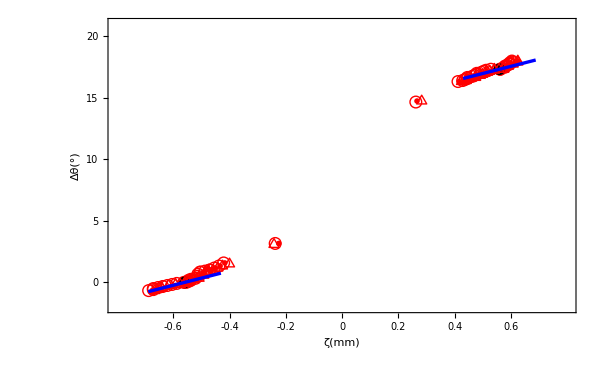
-Graphics-A

```mathematica
ΔθζPlot1[8]=Overlay[{ΔθζPlot[8],Style["A",FontSize->33,FontFamily->"Cambria Math",GrayLevel[0],Bold]},Alignment->{-0.92,-0.9}]
```

#### 7 mm Pitch

```mathematica
Δθζ[O][7][1]=Thread[{ζ[O][7][1],ΔθDeg[O][7][1]}];(*List of points (ζ,Δθ(°)) in the opening process from the first experiment*)
Δθζ[O][7][2]=Thread[{ζ[O][7][2],ΔθDeg[O][7][2]}];(*List of points (ζ,Δθ(°)) in the opening process from the second experiment*)
Δθζ[O][7][3]=Thread[{ζ[O][7][3],ΔθDeg[O][7][3]}];(*List of points (ζ,Δθ(°)) in the opening process from the third experiment*)
Δθζ[C][7][1]=Thread[{ζ[C][7][1],ΔθDeg[C][7][1]}];(*List of points (ζ,Δθ(°)) in the closing process from the first experiment*)
Δθζ[C][7][2]=Thread[{ζ[C][7][2],ΔθDeg[C][7][2]}];(*List of points (ζ,Δθ(°)) in the closing process from the second experiment*)
Δθζ[C][7][3]=Thread[{ζ[C][7][3],ΔθDeg[C][7][3]}];(*List of points (ζ,Δθ(°)) in the closing process from the third experiment*)
```

```mathematica
cθ1Model[7] = cθ1Eq[[2]]/.ζ0->ζ0[7]/.ro->ro[7]/.ri->ri[7]
```

0.292488

```mathematica
cθ1Fit[7] = FindFit[Join[Take[Δθζ[O][7][1],{1,-2}],Take[Δθζ[O][7][2],{1,-2}],Take[Δθζ[O][7][3],{1,-2}],Take[Δθζ[C][7][1],{1,-2}],Take[Δθζ[C][7][2],{1,-2}],Take[Δθζ[C][7][3],{1,-2}]],{ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.Δθζ0p->Δθζ0p[7]/.βoDeg->βoDeg[7]/.δ->ζ0[7]/.ζ0->ζ0[7]},{cθ1},ζ,Method->"Automatic"][[1]][[2]]
```

0.27311

```mathematica
cθ1Err[7]=(cθ1Model[7]-cθ1Fit[7])/cθ1Fit[7]*100
```

7.09514

```mathematica
ΔθζTheoreticalPlotLeft[7]=Plot[ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.cθ1->cθ1Eq[[2]]/.Δθζ0p->Δθζ0p[7]/.ζ0->ζ0[7]/.βoDeg->βoDeg[7]/.ro->ro[7]/.ri->ri[7]/.δ->ζ0[7],{ζ,-ζ0[7]-((ro[7]-ri[7])/ro[7])^2 ro[7],-ζ0[7]+((ro[7]-ri[7])/ro[7])^2  ro[7]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
ΔθζTheoreticalPlotRight[7]=Plot[ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.cθ1->cθ1Eq[[2]]/.Δθζ0p->Δθζ0p[7]/.ζ0->ζ0[7]/.βoDeg->βoDeg[7]/.ro->ro[7]/.ri->ri[7]/.δ->ζ0[7],{ζ,ζ0[7]-((ro[7]-ri[7])/ro[7])^2  ro[7],ζ0[7]+((ro[7]-ri[7])/ro[7])^2  ro[7]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
ΔθζStabilityList[7]={{-ζ0[7],1/3(ΔθDeg[O][7][1][[9]]+ΔθDeg[O][7][2][[9]]+ΔθDeg[O][7][3][[9]])},{ζ0[7],1/3(ΔθDeg[C][7][1][[9]]+ΔθDeg[C][7][2][[9]]+ΔθDeg[C][7][3][[9]])}};
```

```mathematica
ΔθζPlot[7]=Framed[Show[ListPlot[Join[Δθζ[O][7][1],Δθζ[C][7][1]],PlotMarkers->Style[○,12],PlotStyle->Red],
ListPlot[Join[Δθζ[O][7][2],Δθζ[C][7][2]],PlotMarkers->Style[△,12],PlotStyle->Red],
ListPlot[Join[Δθζ[O][7][3],Δθζ[C][7][3]],PlotMarkers->Style[◻,12],PlotStyle->Red],ListPlot[ΔθζStabilityList[7],PlotMarkers->Style["●",12],PlotStyle->Black],ΔθζTheoreticalPlotLeft[7],ΔθζTheoreticalPlotRight[7],PlotStyle->{Thickness[0.008]},AxesOrigin->{0,0},ImageSize->{600,400},Axes->False,LabelStyle->{FontFamily->"Cambria Math",31,GrayLevel[0]},PlotRange->{{-0.7,0.7},{-2,16}},Frame->{True,True,False,False},FrameLabel->{{"Δθ(°)",None  },{"ζ(mm)",None }},FrameTicks->{{{-0.6,"-0.6",0.02},{-0.4,"-0.4",0.02},{-0.2,"-0.2",0.02},{0,"0",0.02},{0.2,"0.2",0.02},{0.4,"0.4",0.02},{0.6,"0.6",0.02}},{{0,"0",0.02},{5,"5",0.02},{10,"10",0.02},{15,"15",0.02}}},FrameTicksStyle->{Directive[Thick,Black],Directive[Thick,Black]}],FrameMargins->{{5,0},{5,-3}},FrameStyle->{Thick,Black}];
```

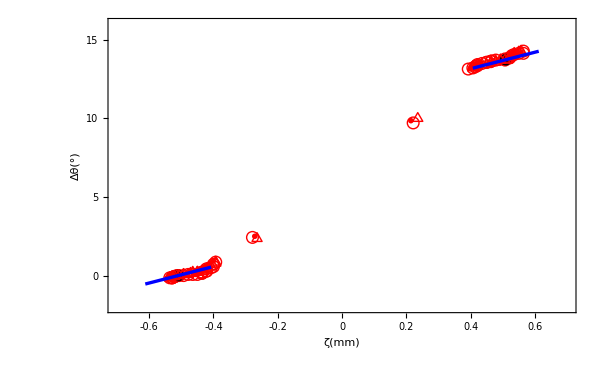
-Graphics-B

```mathematica
ΔθζPlot1[7]=Overlay[{ΔθζPlot[7],Style["B",FontSize->33,FontFamily->"Cambria Math",GrayLevel[0],Bold]},Alignment->{-0.92,-0.9}]
```

#### 6 mm Pitch

```mathematica
Δθζ[O][6][1]=Thread[{ζ[O][6][1],ΔθDeg[O][6][1]}];(*List of points (ζ,Δθ(°)) in the opening process from the first experiment*)
Δθζ[O][6][2]=Thread[{ζ[O][6][2],ΔθDeg[O][6][2]}];(*List of points (ζ,Δθ(°)) in the opening process from the second experiment*)
Δθζ[O][6][3]=Thread[{ζ[O][6][3],ΔθDeg[O][6][3]}];(*List of points (ζ,Δθ(°)) in the opening process from the third experiment*)
Δθζ[C][6][1]=Thread[{ζ[C][6][1],ΔθDeg[C][6][1]}];(*List of points (ζ,Δθ(°)) in the closing process from the first experiment*)
Δθζ[C][6][2]=Thread[{ζ[C][6][2],ΔθDeg[C][6][2]}];(*List of points (ζ,Δθ(°)) in the closing process from the second experiment*)
Δθζ[C][6][3]=Thread[{ζ[C][6][3],ΔθDeg[C][6][3]}];(*List of points (ζ,Δθ(°)) in the closing process from the third experiment*)
```

```mathematica
cθ1Model[6] = cθ1Eq[[2]]/.ζ0->ζ0[6]/.ro->ro[6]/.ri->ri[6]
```

0.325663

```mathematica
cθ1Fit[6] = FindFit[Join[Take[Δθζ[O][6][1],{1,-2}],Take[Δθζ[O][6][2],{1,-2}],Take[Δθζ[O][6][3],{1,-2}],Take[Δθζ[C][6][1],{1,-2}],Take[Δθζ[C][6][2],{1,-2}],Take[Δθζ[C][6][3],{1,-2}]],{ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.Δθζ0p->Δθζ0p[6]/.βoDeg->βoDeg[6]/.δ->ζ0[6]/.ζ0->ζ0[6]},{cθ1},ζ,Method->"Automatic"][[1]][[2]]
```

0.381104

```mathematica
cθ1Err[6]=(cθ1Model[6]-cθ1Fit[6])/cθ1Fit[6]*100
```

-14.5475

```mathematica
ΔθζTheoreticalPlotLeft[6]=Plot[ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.cθ1->cθ1Eq[[2]]/.Δθζ0p->Δθζ0p[6]/.ζ0->ζ0[6]/.βoDeg->βoDeg[6]/.ro->ro[6]/.ri->ri[6]/.δ->ζ0[6],{ζ,-ζ0[6]-((ro[6]-ri[6])/ro[6])^2  ro[6],-ζ0[6]+((ro[6]-ri[6])/ro[6])^2 ro[6]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
ΔθζTheoreticalPlotRight[6]=Plot[ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.cθ1->cθ1Eq[[2]]/.Δθζ0p->Δθζ0p[6]/.ζ0->ζ0[6]/.βoDeg->βoDeg[6]/.ro->ro[6]/.δ->ζ0[6]/.ri->ri[6],{ζ,ζ0[6]-((ro[6]-ri[6])/ro[6])^2 ro[6],ζ0[6]+((ro[6]-ri[6])/ro[6])^2 ro[6]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
ΔθζStabilityList[6]={{-ζ0[6],1/3(ΔθDeg[O][6][1][[9]]+ΔθDeg[O][6][2][[9]]+ΔθDeg[O][6][3][[9]])},{ζ0[6],1/3(ΔθDeg[C][6][1][[9]]+ΔθDeg[C][6][2][[9]]+ΔθDeg[C][6][3][[9]])}};
```

```mathematica
ΔθζPlot[6]=Framed[Show[ListPlot[Join[Δθζ[O][6][1],Δθζ[C][6][1]],PlotMarkers->Style[○,12],PlotStyle->Red],
ListPlot[Join[Δθζ[O][6][2],Δθζ[C][6][2]],PlotMarkers->Style[△,12],PlotStyle->Red],
ListPlot[Join[Δθζ[O][6][3],Δθζ[C][6][3]],PlotMarkers->Style[◻,12],PlotStyle->Red],ListPlot[ΔθζStabilityList[6],PlotMarkers->Style["●",12],PlotStyle->Black],ΔθζTheoreticalPlotLeft[6],ΔθζTheoreticalPlotRight[6],PlotStyle->{Thickness[0.008]},AxesOrigin->{0,0},ImageSize->{600,400},Axes->False,LabelStyle->{FontFamily->"Cambria Math",31,GrayLevel[0]},PlotRange->{{-0.5,0.5},{-1,10.5}},Frame->{True,True,False,False},FrameLabel->{{"Δθ(°)",None  },{"ζ(mm)",None }},FrameTicks->{{{-0.4,"-0.4",0.02},{-0.2,"-0.2",0.02},{0,"0",0.02},{0.2,"0.2",0.02},{0.4,"0.4",0.02}},{{0,"0",0.02},{2,"2",0.02},{4,"4",0.02},{6,"6",0.02},{8,"8",0.02},{10,"10",0.02}}},FrameTicksStyle->{Directive[Thick,Black],Directive[Thick,Black]}],FrameMargins->{{5,0},{5,-3}},FrameStyle->{Thick,Black}];
```

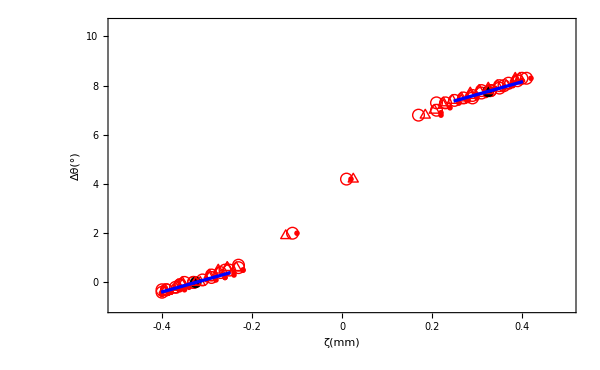
-Graphics-C

```mathematica
ΔθζPlot1[6]=Overlay[{ΔθζPlot[6],Style["C",FontSize->33,FontFamily->"Cambria Math",GrayLevel[0],Bold]},Alignment->{-0.92,-0.9}]
```

#### 5 mm Pitch

```mathematica
Δθζ[O][5][1]=Thread[{ζ[O][5][1],ΔθDeg[O][5][1]}];(*List of points (ζ,Δθ(°)) in the opening process from the first experiment*)
Δθζ[O][5][2]=Thread[{ζ[O][5][2],ΔθDeg[O][5][2]}];(*List of points (ζ,Δθ(°)) in the opening process from the second experiment*)
Δθζ[O][5][3]=Thread[{ζ[O][5][3],ΔθDeg[O][5][3]}];(*List of points (ζ,Δθ(°)) in the opening process from the third experiment*)
Δθζ[C][5][1]=Thread[{ζ[C][5][1],ΔθDeg[C][5][1]}];(*List of points (ζ,Δθ(°)) in the closing process from the first experiment*)
Δθζ[C][5][2]=Thread[{ζ[C][5][2],ΔθDeg[C][5][2]}];(*List of points (ζ,Δθ(°)) in the closing process from the second experiment*)
Δθζ[C][5][3]=Thread[{ζ[C][5][3],ΔθDeg[C][5][3]}];(*List of points (ζ,Δθ(°)) in the closing process from the third experiment*)
```

```mathematica
cθ1Model[5] = cθ1Eq[[2]]/.ζ0->ζ0[5]/.ro->ro[5]/.ri->ri[5]
```

0.307287

```mathematica
cθ1Fit[5] = FindFit[Join[Take[Δθζ[O][5][1],{1,-2}],Take[Δθζ[O][5][2],{1,-2}],Take[Δθζ[O][5][3],{1,-2}],Take[Δθζ[C][5][1],{1,-2}],Take[Δθζ[C][5][2],{1,-2}],Take[Δθζ[C][5][3],{1,-2}]],{ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.Δθζ0p->Δθζ0p[5]/.βoDeg->βoDeg[5]/.δ->ζ0[5]/.ζ0->ζ0[5]},{cθ1},ζ,Method->"Automatic"][[1]][[2]]
```

0.495194

```mathematica
cθ1Err[5]=(cθ1Model[5]-cθ1Fit[5])/cθ1Fit[5]*100
```

-37.9462

```mathematica
ΔθζTheoreticalPlotLeft[5]=Plot[ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.cθ1->cθ1Eq[[2]]/.Δθζ0p->Δθζ0p[5]/.ζ0->ζ0[5]/.βoDeg->βoDeg[5]/.ro->ro[5]/.ri->ri[5]/.δ->ζ0[5],{ζ,-ζ0[5]-((ro[5]-ri[5])/ro[5])^2 ro[5],-ζ0[5]+((ro[5]-ri[5])/ro[5])^2 ro[5]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
ΔθζTheoreticalPlotRight[5]=Plot[ΔθEqDeg[[2]]/.cθ0->cθ0Eq[[2]]/.cθ1->cθ1Eq[[2]]/.Δθζ0p->Δθζ0p[5]/.ζ0->ζ0[5]/.βoDeg->βoDeg[5]/.ro->ro[5]/.ri->ri[5]/.δ->ζ0[5],{ζ,ζ0[5]-((ro[5]-ri[5])/ro[5])^2 ro[5],ζ0[5]+((ro[5]-ri[5])/ro[5])^2 ro[5]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
ΔθζStabilityList[5]={{-ζ0[5],1/3(ΔθDeg[O][5][1][[9]]+ΔθDeg[O][5][2][[9]]+ΔθDeg[O][5][3][[9]])},{ζ0[5],1/3(ΔθDeg[C][5][1][[9]]+ΔθDeg[C][5][2][[9]]+ΔθDeg[C][5][3][[9]])}};
```

```mathematica
ΔθζPlot[5]=Framed[Show[ListPlot[Join[Δθζ[O][5][1],Δθζ[C][5][1]],PlotMarkers->Style[○,12],PlotStyle->Red],
ListPlot[Join[Δθζ[O][5][2],Δθζ[C][5][2]],PlotMarkers->Style[△,12],PlotStyle->Red],
ListPlot[Join[Δθζ[O][5][3],Δθζ[C][5][3]],PlotMarkers->Style[◻,12],PlotStyle->Red],ListPlot[ΔθζStabilityList[5],PlotMarkers->Style["●",12],PlotStyle->Black],ΔθζTheoreticalPlotLeft[5],ΔθζTheoreticalPlotRight[5],PlotStyle->{Thickness[0.008]},AxesOrigin->{0,0},ImageSize->{600,400},Axes->False,LabelStyle->{FontFamily->"Cambria Math",31,GrayLevel[0]},PlotRange->{{-0.65,0.65},{-1,10.5}},Frame->{True,True,False,False},FrameLabel->{{"Δθ(°)",None  },{"ζ(mm)",None }},FrameTicks->{{{-0.6,"-0.6",0.02},{-0.4,"-0.4",0.02},{-0.2,"-0.2",0.02},{0,"0",0.02},{0.2,"0.2",0.02},{0.4,"0.4",0.02},{0.6,"0.6",0.02}},{{0,"0",0.02},{2,"2",0.02},{4,"4",0.02},{6,"6",0.02},{8,"8",0.02},{10,"10",0.02}}},FrameTicksStyle->{Directive[Thick,Black],Directive[Thick,Black]}],FrameMargins->{{5,0},{5,-3}},FrameStyle->{Thick,Black}];
```

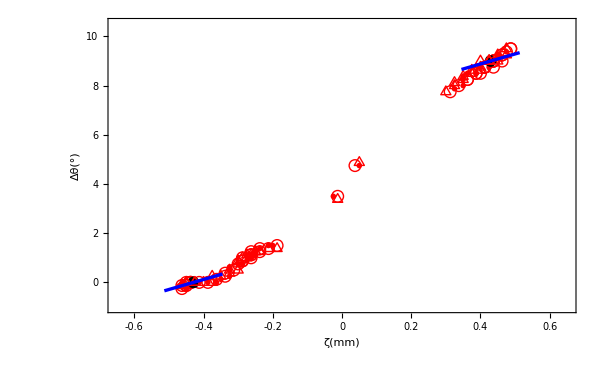
-Graphics-D

```mathematica
ΔθζPlot1[5]=Overlay[{ΔθζPlot[5],Style["D",FontSize->33,FontFamily->"Cambria Math",GrayLevel[0],Bold]},Alignment->{-0.92,-0.9}]
```

### Figure 8

#### 8 mm Pitch

```mathematica
pζ[O][8][1]=Thread[{ζ[O][8][1],0.101325*p[O][8]}];(*List of points (ζ,p) in the opening process from the first experiment*)
pζ[O][8][2]=Thread[{ζ[O][8][2],0.101325*p[O][8]}];(*List of points (ζ,p) in the opening process from the second experiment*)
pζ[O][8][3]=Thread[{ζ[O][8][3],0.101325*p[O][8]}];(*List of points (ζ,p) in the opening process from the third experiment*)
pζ[C][8][1]=Thread[{ζ[C][8][1],0.101325*p[C][8]}];(*List of points (ζ,p) in the closing process from the first experiment*)
pζ[C][8][2]=Thread[{ζ[C][8][2],0.101325*p[C][8]}];(*List of points (ζ,p) in the closing process from the second experiment*)
pζ[C][8][3]=Thread[{ζ[C][8][3],0.101325*p[C][8]}];(*List of points (ζ,p) in the closing process from the third experiment*)
```

```mathematica
cphMyfit[8]=FindFit[Join[Take[pζ[O][8][1],{1,-2}],Take[pζ[O][8][2],{1,-2}],Take[pζ[O][8][3],{1,-2}],Take[pζ[C][8][1],{1,-2}],Take[pζ[C][8][2],{1,-2}],Take[pζ[C][8][3],{1,-2}]],{pinEq1[[2]]/.cp h My-> A/.ζ0->Sign[ζ]ζ0[8]},{A},ζ,Method->"Automatic"][[1]][[2]]
```

0.50865

```mathematica
LeftLinearPlot[8]= Plot[pinEq1[[2]]/.cp h My-> cphMyfit[8]/.ζ0->-ζ0[8],{ζ,-ζ0[8]-((ro[8]-ri[8])/ro[8])^2 ro[8],-ζ0[8]+((ro[8]-ri[8])/ro[8])^2 ro[8]},PlotStyle->{Thickness[0.004],Blue},PlotLegends->{Placed[SwatchLegend[{Red,Blue,Black,Blue},{Style["Experiment",FontSize->31,FontFamily->"Cambria Math",GrayLevel[0]],Style[" Linear Fit",FontSize->31,FontFamily->"Cambria Math",GrayLevel[0]],Style["Stability Points",FontSize->31,FontFamily->"Cambria Math",GrayLevel[0]]},LegendMarkers->{{"○△◻ ",50},{Graphics[Table[{Thickness[r],Line[{{0,0},{1,0}}]},{r,{0.13}}]],45},{"  ● ",50},{Graphics[Table[{Thickness[r],Dashed,Line[{{0,0},{1,0}}]},{r,{0.13}}]],45}},LegendLayout->(Column[(Row[{#1[[1]]," ",#1[[2]]}]&)/@#,Left,-1]&)],{0.40,0.22}]}];
```

```mathematica
RightLinearPlot[8]= Plot[pinEq1[[2]]/.cp h My-> cphMyfit[8]/.ζ0->ζ0[8],{ζ,ζ0[8]-((ro[8]-ri[8])/ro[8])^2 ro[8],ζ0[8]+((ro[8]-ri[8])/ro[8])^2 ro[8]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
pζStabilityList[8]={{-ζ0[8],0},{ζ0[8],0}};
```

```mathematica
pζPlot[8]=Framed[Show[ListPlot[Join[pζ[O][8][1],pζ[C][8][1]],PlotMarkers->Style[○,12],PlotStyle->Red],
ListPlot[Join[pζ[O][8][2],pζ[C][8][2]],PlotMarkers->Style[△,12],PlotStyle->Red],
ListPlot[Join[pζ[O][8][3],pζ[C][8][3]],PlotMarkers->Style[◻,12],PlotStyle->Red],ListPlot[pζStabilityList[8],PlotMarkers->Style["●",12],PlotStyle->Black],LeftLinearPlot[8],RightLinearPlot[8],PlotStyle->{Thickness[0.008]},AxesOrigin->{0,0},ImageSize->{600,400},Axes->False,LabelStyle->{FontFamily->"Cambria Math",31,GrayLevel[0]},PlotRange->{{-0.75,0.75},{-0.115,0.115}},Frame->{True,True,False,False},FrameLabel->{{"p_in(MPa)",None  },{"ζ(mm)",None }},FrameTicks->{{{-0.4,"-0.4",0.02},{-0.6,"-0.6",0.02},{-0.2,"-0.2",0.02},{0,"0",0.02},{0.2,"0.2",0.02},{0.4,"0.4",0.02},{0.6,"0.6",0.02}},{{-0.1,"-0.1",0.02},{-0.05,"-0.05",0.02},{0,"0",0.02},{0.05,"0.05",0.02},{0.1,"0.1",0.02}}},FrameTicksStyle->{Directive[Thick,Black],Directive[Thick,Black]}],FrameMargins->{{5,0},{5,-17}},FrameStyle->{Thick,Black}];
```

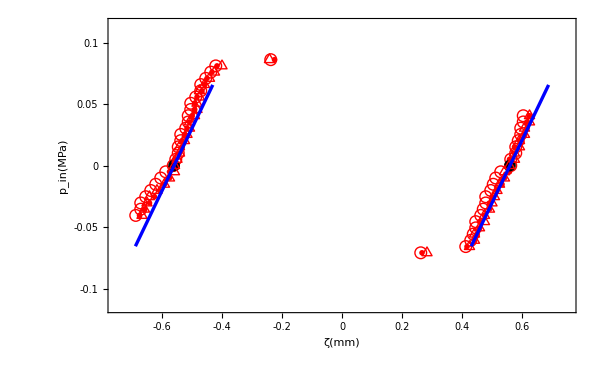
-Graphics-A

```mathematica
pζ1Plot[8]=Overlay[{pζPlot[8],Style["A",FontSize->33,FontFamily->"Cambria Math",GrayLevel[0],Bold]},Alignment->{-0.92,-0.9}]
```

#### 7 mm Pitch

```mathematica
pζ[O][7][1]=Thread[{ζ[O][7][1],0.101325*p[O][7]}];(*List of points (ζ,p) in the opening process from the first experiment*)
pζ[O][7][2]=Thread[{ζ[O][7][2],0.101325*p[O][7]}];(*List of points (ζ,p) in the opening process from the second experiment*)
pζ[O][7][3]=Thread[{ζ[O][7][3],0.101325*p[O][7]}];(*List of points (ζ,p) in the opening process from the third experiment*)
pζ[C][7][1]=Thread[{ζ[C][7][1],0.101325*p[C][7]}];(*List of points (ζ,p) in the closing process from the first experiment*)
pζ[C][7][2]=Thread[{ζ[C][7][2],0.101325*p[C][7]}];(*List of points (ζ,p) in the closing process from the second experiment*)
pζ[C][7][3]=Thread[{ζ[C][7][3],0.101325*p[C][7]}];(*List of points (ζ,p) in the closing process from the third experiment*)
```

```mathematica
cphMyfit[7]=FindFit[Join[Take[pζ[O][7][1],{1,-2}],Take[pζ[O][7][2],{1,-2}],Take[pζ[O][7][3],{1,-2}],Take[pζ[C][7][1],{1,-2}],Take[pζ[C][7][2],{1,-2}],Take[pζ[C][7][3],{1,-2}]],{pinEq1[[2]]/.cp h My-> A/.ζ0->Sign[ζ]ζ0[7]},{A},ζ,Method->"Automatic"][[1]][[2]]
```

0.59967

```mathematica
LeftLinearPlot[7]= Plot[pinEq1[[2]]/.cp h My->cphMyfit[7]/.ζ0->-ζ0[7],{ζ,-ζ0[7]-((ro[7]-ri[7])/ro[7])^2 ro[7],-ζ0[7]+((ro[7]-ri[7])/ro[7])^2 ro[7]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
RightLinearPlot[7]= Plot[pinEq1[[2]]/.cp h My-> cphMyfit[7]/.ζ0->ζ0[7],{ζ,ζ0[7]-((ro[7]-ri[7])/ro[7])^2 ro[7],ζ0[7]+((ro[7]-ri[7])/ro[7])^2 ro[7]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
pζStabilityList[7]={{-ζ0[7],0},{ζ0[7],0}};
```

```mathematica
pζPlot[7]=Framed[Show[ListPlot[Join[pζ[O][7][1],pζ[C][7][1]],PlotMarkers->Style[○,12],PlotStyle->Red],
ListPlot[Join[pζ[O][7][2],pζ[C][7][2]],PlotMarkers->Style[△,12],PlotStyle->Red],
ListPlot[Join[pζ[O][7][3],pζ[C][7][3]],PlotMarkers->Style[◻,12],PlotStyle->Red],ListPlot[pζStabilityList[7],PlotMarkers->Style["●",12],PlotStyle->Black],LeftLinearPlot[7],RightLinearPlot[7],PlotStyle->{Thickness[0.008]},AxesOrigin->{0,0},ImageSize->{600,400},Axes->False,LabelStyle->{FontFamily->"Cambria Math",31,GrayLevel[0]},PlotRange->{{-0.7,0.7},{-0.115,0.115}},Frame->{True,True,False,False},FrameLabel->{{"p_in(MPa)",None  },{"ζ(mm)",None }},FrameTicks->{{{-0.4,"-0.4",0.02},{-0.6,"-0.6",0.02},{-0.2,"-0.2",0.02},{0,"0",0.02},{0.2,"0.2",0.02},{0.4,"0.4",0.02},{0.6,"0.6",0.02}},{{-0.1,"-0.1",0.02},{-0.05,"-0.05",0.02},{0,"0",0.02},{0.05,"0.05",0.02},{0.1,"0.1",0.02}}},FrameTicksStyle->{Directive[Thick,Black],Directive[Thick,Black]}],FrameMargins->{{5,0},{5,-17}},FrameStyle->{Thick,Black}];
```

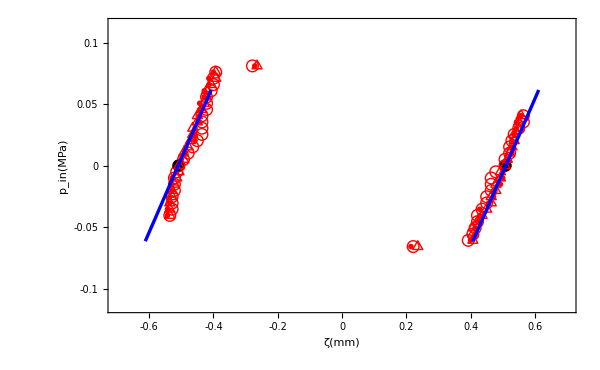
-Graphics-B

```mathematica
pζ1Plot[7]=Overlay[{pζPlot[7],Style["B",FontSize->33,FontFamily->"Cambria Math",GrayLevel[0],Bold]},Alignment->{-0.92,-0.9}]
```

#### 6 mm Pitch

```mathematica
pζ[O][6][1]=Thread[{ζ[O][6][1],0.101325*p[O][6]}];(*List of points (ζ,p) in the opening process from the first experiment*)
pζ[O][6][2]=Thread[{ζ[O][6][2],0.101325*p[O][6]}];(*List of points (ζ,p) in the opening process from the second experiment*)
pζ[O][6][3]=Thread[{ζ[O][6][3],0.101325*p[O][6]}];(*List of points (ζ,p) in the opening process from the third experiment*)
pζ[C][6][1]=Thread[{ζ[C][6][1],0.101325*p[C][6]}];(*List of points (ζ,p) in the closing process from the first experiment*)
pζ[C][6][2]=Thread[{ζ[C][6][2],0.101325*p[C][6]}];(*List of points (ζ,p) in the closing process from the second experiment*)
pζ[C][6][3]=Thread[{ζ[C][6][3],0.101325*p[C][6]}];(*List of points (ζ,p) in the closing process from the third experiment*)
```

```mathematica
cphMyfit[6]=FindFit[Join[Take[pζ[O][6][1],{1,-2}],Take[pζ[O][6][2],{1,-2}],Take[pζ[O][6][3],{1,-2}],Take[pζ[C][6][1],{1,-2}],Take[pζ[C][6][2],{1,-2}],Take[pζ[C][6][3],{1,-2}]],{pinEq1[[2]]/.cp h My-> A/.ζ0->Sign[ζ]ζ0[6]},{A},ζ,Method->"Automatic"][[1]][[2]]
```

0.459556

```mathematica
LeftLinearPlot[6]= Plot[pinEq1[[2]]/.cp h My->cphMyfit[6]/.ζ0->-ζ0[6],{ζ,-ζ0[6]-((ro[6]-ri[6])/ro[6])^2 ro[6],-ζ0[6]+((ro[6]-ri[6])/ro[6])^2 ro[6]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
RightLinearPlot[6]= Plot[pinEq1[[2]]/.cp h My->cphMyfit[6]/.ζ0->ζ0[6],{ζ,ζ0[6]-((ro[6]-ri[6])/ro[6])^2 ro[6],ζ0[6]+((ro[6]-ri[6])/ro[6])^2 ro[6]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
pζStabilityList[6]={{-ζ0[6],0},{ζ0[6],0}};
```

```mathematica
pζPlot[6]=Framed[Show[ListPlot[Join[pζ[O][6][1],pζ[C][6][1]],PlotMarkers->Style[○,12],PlotStyle->Red],
ListPlot[Join[pζ[O][6][2],pζ[C][6][2]],PlotMarkers->Style[△,12],PlotStyle->Red],
ListPlot[Join[pζ[O][6][3],pζ[C][6][3]],PlotMarkers->Style[◻,12],PlotStyle->Red],ListPlot[pζStabilityList[6],PlotMarkers->Style["●",12],PlotStyle->Black],LeftLinearPlot[6],RightLinearPlot[6],PlotStyle->{Thickness[0.008]},AxesOrigin->{0,0},ImageSize->{600,400},Axes->False,LabelStyle->{FontFamily->"Cambria Math",31,GrayLevel[0]},PlotRange->{{-0.5,0.5},{-0.08,0.08}},Frame->{True,True,False,False},FrameLabel->{{"p_in(MPa)",None  },{"ζ(mm)",None }},FrameTicks->{{{-0.4,"-0.4",0.02},{-0.6,"-0.6",0.02},{-0.2,"-0.2",0.02},{0,"0",0.02},{0.2,"0.2",0.02},{0.4,"0.4",0.02},{0.6,"0.6",0.02}},{{-0.1,"-0.1",0.02},{-0.05,"-0.05",0.02},{0,"0",0.02},{0.05,"0.05",0.02},{0.1,"0.1",0.02}}},FrameTicksStyle->{Directive[Thick,Black],Directive[Thick,Black]}],FrameMargins->{{5,0},{5,-17}},FrameStyle->{Thick,Black}];
```

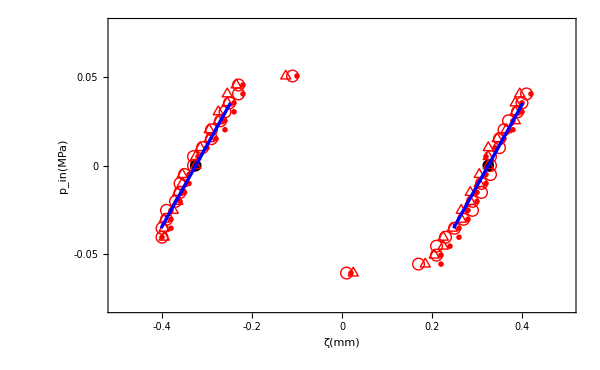
-Graphics-C

```mathematica
pζ1Plot[6]=Overlay[{pζPlot[6],Style["C",FontSize->33,FontFamily->"Cambria Math",GrayLevel[0],Bold]},Alignment->{-0.92,-0.9}]
```

#### 5 mm Pitch

```mathematica
pζ[O][5][1]=Thread[{ζ[O][5][1],0.101325*p[O][5]}];(*List of points (ζ,p) in the opening process from the first experiment*)
pζ[O][5][2]=Thread[{ζ[O][5][2],0.101325*p[O][5]}];(*List of points (ζ,p) in the opening process from the second experiment*)
pζ[O][5][3]=Thread[{ζ[O][5][3],0.101325*p[O][5]}];(*List of points (ζ,p) in the opening process from the third experiment*)
pζ[C][5][1]=Thread[{ζ[C][5][1],0.101325*p[C][5]}];(*List of points (ζ,p) in the closing process from the first experiment*)
pζ[C][5][2]=Thread[{ζ[C][5][2],0.101325*p[C][5]}];(*List of points (ζ,p) in the closing process from the second experiment*)
pζ[C][5][3]=Thread[{ζ[C][5][3],0.101325*p[C][5]}];(*List of points (ζ,p) in the closing process from the third experiment*)
```

```mathematica
cphMyfit[5]=FindFit[Join[Take[pζ[O][5][1],{1,-2}],Take[pζ[O][5][2],{1,-2}],Take[pζ[O][5][3],{1,-2}],Take[pζ[C][5][1],{1,-2}],Take[pζ[C][5][2],{1,-2}],Take[pζ[C][5][3],{1,-2}]],{pinEq1[[2]]/.cp h My-> A/.ζ0->Sign[ζ]ζ0[5]},{A},ζ,Method->"Automatic"][[1]][[2]]
```

0.409125

```mathematica
LeftLinearPlot[5]= Plot[pinEq1[[2]]/.cp h My->cphMyfit[5]/.ζ0->-ζ0[5],{ζ,-ζ0[5]-((ro[5]-ri[5])/ro[5])^2 ro[5],-ζ0[5]+((ro[5]-ri[5])/ro[5])^2 ro[5]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
RightLinearPlot[5]= Plot[pinEq1[[2]]/.cp h My->cphMyfit[5]/.ζ0->ζ0[5],{ζ,ζ0[5]-((ro[5]-ri[5])/ro[5])^2 ro[5],ζ0[5]+((ro[5]-ri[5])/ro[5])^2 ro[5]},PlotStyle->{Thickness[0.004],Blue}];
```

```mathematica
pζStabilityList[5]={{-ζ0[5],0},{ζ0[5],0}};
```

```mathematica
pζPlot[5]=Framed[Show[ListPlot[Join[pζ[O][5][1],pζ[C][5][1]],PlotMarkers->Style[○,12],PlotStyle->Red],
ListPlot[Join[pζ[O][5][2],pζ[C][5][2]],PlotMarkers->Style[△,12],PlotStyle->Red],
ListPlot[Join[pζ[O][5][3],pζ[C][5][3]],PlotMarkers->Style[◻,12],PlotStyle->Red],ListPlot[pζStabilityList[5],PlotMarkers->Style["●",12],PlotStyle->Black],LeftLinearPlot[5],RightLinearPlot[5],PlotStyle->{Thickness[0.008]},AxesOrigin->{0,0},ImageSize->{600,400},Axes->False,LabelStyle->{FontFamily->"Cambria Math",31,GrayLevel[0]},PlotRange->{{-0.55,0.55},{-0.115,0.115}},Frame->{True,True,False,False},FrameLabel->{{"p_in(MPa)",None  },{"ζ(mm)",None }},FrameTicks->{{{-0.4,"-0.4",0.02},{-0.6,"-0.6",0.02},{-0.2,"-0.2",0.02},{0,"0",0.02},{0.2,"0.2",0.02},{0.4,"0.4",0.02},{0.6,"0.6",0.02}},{{-0.1,"-0.1",0.02},{-0.05,"-0.05",0.02},{0,"0",0.02},{0.05,"0.05",0.02},{0.1,"0.1",0.02}}},FrameTicksStyle->{Directive[Thick,Black],Directive[Thick,Black]}],FrameMargins->{{5,0},{5,-17}},FrameStyle->{Thick,Black}];
```

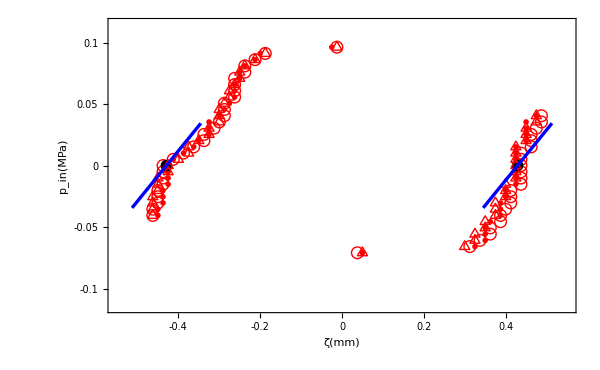
-Graphics-D

```mathematica
pζ1Plot[5]=Overlay[{pζPlot[5],Style["D",FontSize->33,FontFamily->"Cambria Math",GrayLevel[0],Bold]},Alignment->{-0.92,-0.9}]
```